# A. Offspring control (Mike version)

## Recursions (written as in appendix, generic loci order) [Enter]

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploid are indicated by appending an s to the name.

```mathematica
(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;
```

Frequency of males after diplod selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate into new notation:

first two letters refer to SDR locus genotype, then numbers ij giving A and M locus genotype where 
1-AM
2-aM
3-Am
4-am
then m or f indicating male or female
then s to indicate that these are frequencies after selection
e.g., xy41ms is a male with genotype X-a-m Y-A-M. 
Where i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

First, we consider female gametes

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

We can consider male gametes similarly

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Generally want to at least assume that recombination is not affected by M or sex

```mathematica
SUBSR={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ
};
```

Often also want to assume the following about k:

```mathematica
SUBS={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ,
kXX->1,
kXY->0,
kYY->0,
kMmXX->k,
kMmXY->k,
kMmYY->k,
kmm->k,
kmm->k,
kmm->k
};
```

## Complete linkage case

### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

### Equilibrium Derivation

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
nextXAMf-XAMf,
nextXAMm-XAMm,
nextYAMm-YAMm,
nextYAMm+nextYaMm-(YAMm+YaMm)
}/.SUBS/.subequil;
```

```mathematica
sub1=Flatten[Solve[differenceEqs[[3]]==0,pXf]]//Factor
```

{pXf→(2 pYm waf (-freqYm Maa wam+freqYm Maa pYm wam-freqYm MAa pYm wAm+MAa wAm αm-MAa r wAm αm))/(-2 freqYm Maa pYm waf wam+2 freqYm Maa pYm^2 waf wam+2 freqYm MAa pYm wAf wam-2 freqYm MAa pYm^2 wAf wam-2 freqYm MAa pYm^2 waf wAm-MAA pYm wAf wAm+2 freqYm MAA pYm^2 wAf wAm-2 MAa r wAf wam αm+2 MAa pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pYm r waf wAm αm)}

```mathematica
differenceEqs[[2]]/.sub1//Factor
```

(-Maa MAA pXm pYm wam wAm+freqYm Maa MAA pXm pYm wam wAm+freqYm Maa MAA pYm^2 wam wAm+Maa MAA pXm pYm^2 wam wAm-freqYm Maa MAA pXm pYm^2 wam wAm-freqYm Maa MAA pYm^3 wam wAm-MAa MAA pXm pYm^2 wAm^2+freqYm MAa MAA pXm pYm^2 wAm^2+freqYm MAa MAA pYm^3 wAm^2+2 freqYm Maa MAa pYm wam^2 αm-4 freqYm Maa MAa pYm^2 wam^2 αm+2 freqYm Maa MAa pYm^3 wam^2 αm-2 Maa MAa pXm r wam^2 αm+2 freqYm Maa MAa pXm r wam^2 αm-2 freqYm Maa MAa pYm r wam^2 αm+4 Maa MAa pXm pYm r wam^2 αm-4 freqYm Maa MAa pXm pYm r wam^2 αm+4 freqYm Maa MAa pYm^2 r wam^2 αm-2 Maa MAa pXm pYm^2 r wam^2 αm+2 freqYm Maa MAa pXm pYm^2 r wam^2 αm-2 freqYm Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pXm pYm wam wAm αm-2 freqYm MAa^2 pXm pYm wam wAm αm+2 freqYm MAa^2 pYm^2 wam wAm αm-2 MAa^2 pXm pYm^2 wam wAm αm+2 freqYm MAa^2 pXm pYm^2 wam wAm αm-2 freqYm MAa^2 pYm^3 wam wAm αm-4 MAa^2 pXm pYm r wam wAm αm+4 freqYm MAa^2 pXm pYm r wam wAm αm-4 freqYm MAa^2 pYm^2 r wam wAm αm+4 MAa^2 pXm pYm^2 r wam wAm αm-4 freqYm MAa^2 pXm pYm^2 r wam wAm αm+4 freqYm MAa^2 pYm^3 r wam wAm αm-MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pXm pYm^2 wAm^2 αm-2 freqYm MAa MAA pXm pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm-2 MAa MAA pXm pYm^2 r wAm^2 αm+2 freqYm MAa MAA pXm pYm^2 r wAm^2 αm-2 freqYm MAa MAA pYm^3 r wAm^2 αm-2 MAa^2 pYm wam wAm αm^2+2 MAa^2 pYm^2 wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2-4 MAa^2 pYm^2 r wam wAm αm^2)/(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+MAa MAA pYm^2 wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-2 MAa^2 pYm wam wAm αm+2 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm r wam wAm αm-4 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm)

```mathematica
sub2=Flatten[Solve[Factor[differenceEqs[[2]]/.sub1]==0,pXm]]//Factor
```

{pXm→-(pYm (-freqYm Maa MAA pYm wam wAm+freqYm Maa MAA pYm^2 wam wAm-freqYm MAa MAA pYm^2 wAm^2-2 freqYm Maa MAa wam^2 αm+4 freqYm Maa MAa pYm wam^2 αm-2 freqYm Maa MAa pYm^2 wam^2 αm+2 freqYm Maa MAa r wam^2 αm-4 freqYm Maa MAa pYm r wam^2 αm+2 freqYm Maa MAa pYm^2 r wam^2 αm-2 freqYm MAa^2 pYm wam wAm αm+2 freqYm MAa^2 pYm^2 wam wAm αm+4 freqYm MAa^2 pYm r wam wAm αm-4 freqYm MAa^2 pYm^2 r wam wAm αm+MAa MAA pYm wAm^2 αm-2 MAa MAA pYm r wAm^2 αm+2 freqYm MAa MAA pYm^2 r wAm^2 αm+2 MAa^2 wam wAm αm^2-2 MAa^2 pYm wam wAm αm^2-4 MAa^2 r wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2))/((-1+freqYm) (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-MAa MAA pYm^2 wAm^2-2 Maa MAa r wam^2 αm+4 Maa MAa pYm r wam^2 αm-2 Maa MAa pYm^2 r wam^2 αm+2 MAa^2 pYm wam wAm αm-2 MAa^2 pYm^2 wam wAm αm-4 MAa^2 pYm r wam wAm αm+4 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm))}

```mathematica
differenceEqs[[4]]/.sub1/.sub2//Factor
```

(2 freqYm Maa MAa pYm wam^2-4 freqYm Maa MAa pYm^2 wam^2+2 freqYm Maa MAa pYm^3 wam^2-4 freqYm Maa MAa pYm r wam^2+8 freqYm Maa MAa pYm^2 r wam^2-4 freqYm Maa MAa pYm^3 r wam^2+Maa MAA pYm wam wAm-2 freqYm Maa MAA pYm wam wAm+4 freqYm MAa^2 pYm^2 wam wAm-Maa MAA pYm^2 wam wAm+2 freqYm Maa MAA pYm^2 wam wAm-4 freqYm MAa^2 pYm^3 wam wAm-8 freqYm MAa^2 pYm^2 r wam wAm+8 freqYm MAa^2 pYm^3 r wam wAm-2 freqYm MAa MAA pYm^2 wAm^2+2 freqYm MAa MAA pYm^3 wAm^2+2 MAa MAA pYm^2 r wAm^2-4 freqYm MAa MAA pYm^3 r wAm^2-4 freqYm Maa MAa pYm wam^2 αm+8 freqYm Maa MAa pYm^2 wam^2 αm-4 freqYm Maa MAa pYm^3 wam^2 αm+2 Maa MAa r wam^2 αm-4 freqYm Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+16 freqYm Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-20 freqYm Maa MAa pYm^2 r wam^2 αm+8 freqYm Maa MAa pYm^3 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 freqYm MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm-12 freqYm MAa^2 pYm^2 wam wAm αm+8 freqYm MAa^2 pYm^3 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 freqYm MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+24 freqYm MAa^2 pYm^2 r wam wAm αm-16 freqYm MAa^2 pYm^3 r wam wAm αm+4 freqYm MAa MAA pYm^2 wAm^2 αm-4 freqYm MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm-4 freqYm MAa MAA pYm^2 r wAm^2 αm+8 freqYm MAa MAA pYm^3 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+MAa MAA pYm^2 wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-2 MAa^2 pYm wam wAm αm+2 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm r wam wAm αm-4 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm))

```mathematica
sub3=Flatten[Solve[Factor[differenceEqs[[4]]/.sub1/.sub2]==0,freqYm]]//Factor
```

{freqYm→-(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAa pYm wam^2-2 Maa MAa pYm^2 wam^2+Maa MAa pYm^3 wam^2-2 Maa MAa pYm r wam^2+4 Maa MAa pYm^2 r wam^2-2 Maa MAa pYm^3 r wam^2-Maa MAA pYm wam wAm+2 MAa^2 pYm^2 wam wAm+Maa MAA pYm^2 wam wAm-2 MAa^2 pYm^3 wam wAm-4 MAa^2 pYm^2 r wam wAm+4 MAa^2 pYm^3 r wam wAm-MAa MAA pYm^2 wAm^2+MAa MAA pYm^3 wAm^2-2 MAa MAA pYm^3 r wAm^2-2 Maa MAa pYm wam^2 αm+4 Maa MAa pYm^2 wam^2 αm-2 Maa MAa pYm^3 wam^2 αm-2 Maa MAa r wam^2 αm+8 Maa MAa pYm r wam^2 αm-10 Maa MAa pYm^2 r wam^2 αm+4 Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pYm wam wAm αm-6 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm^3 wam wAm αm-4 MAa^2 pYm r wam wAm αm+12 MAa^2 pYm^2 r wam wAm αm-8 MAa^2 pYm^3 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa MAA pYm^3 r wAm^2 αm))}

```mathematica
equilsol=Numerator[Factor[differenceEqs[[1]]/.sub1/.sub2/.sub3]]
```

-(-1+pYm) pYm (2 FAa Maa^3 MAa pYm^2 waf wam^5-4 Faa Maa^2 MAa^2 pYm^2 waf wam^5-6 FAa Maa^3 MAa pYm^3 waf wam^5+12 Faa Maa^2 MAa^2 pYm^3 waf wam^5+«1951»+448 FAa MAa^4 pYm^3 r^3 waf wam^2 wAm^3 αf αm^4-512 FAa MAa^4 pYm^4 r^3 waf wam^2 wAm^3 αf αm^4+256 FAa MAa^4 pYm^5 r^3 waf wam^2 wAm^3 αf αm^4)

In the following we assume r=0 to leading order to determine the equilibrium in the case where the A locus resides in the SDR:

```mathematica
equilsol/.r->0//Factor
```

(-1+pYm)^3 pYm^3 (-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (FAa Maa^2 waf wam^3-2 Faa Maa MAa waf wam^3-FAa Maa^2 pYm waf wam^3+2 Faa Maa MAa pYm waf wam^3+Faa Maa MAA waf wam^2 wAm+2 FAa Maa MAa pYm waf wam^2 wAm-4 Faa MAa^2 pYm waf wam^2 wAm-Faa Maa MAA pYm waf wam^2 wAm+FAa Maa MAA pYm waf wam wAm^2+2 Faa MAa MAA pYm waf wam wAm^2-FAA Maa MAA pYm wAf wam wAm^2-FAa Maa^2 waf wam^3 αf+FAa Maa^2 pYm waf wam^3 αf+2 FAa Maa MAa wAf wam^3 αf-2 FAa Maa MAa pYm wAf wam^3 αf-2 FAa Maa MAa pYm waf wam^2 wAm αf-FAa Maa MAA wAf wam^2 wAm αf+4 FAa MAa^2 pYm wAf wam^2 wAm αf+FAa Maa MAA pYm wAf wam^2 wAm αf-FAa Maa MAA pYm waf wam wAm^2 αf-FAa MAA^2 pYm wAf wAm^3 αf+2 Faa Maa MAa waf wam^3 αm-2 Faa Maa MAa pYm waf wam^3 αm-2 FAa Maa MAa pYm waf wam^2 wAm αm+8 Faa MAa^2 pYm waf wam^2 wAm αm-2 FAA Maa MAa wAf wam^2 wAm αm+2 FAA Maa MAa pYm wAf wam^2 wAm αm-4 FAa MAa^2 pYm waf wam wAm^2 αm-2 Faa MAa MAA pYm waf wam wAm^2 αm-2 FAa MAa MAA pYm waf wAm^3 αm+2 FAA MAa MAA pYm wAf wAm^3 αm-2 FAa Maa MAa wAf wam^3 αf αm+2 FAa Maa MAa pYm wAf wam^3 αf αm+2 FAa Maa MAa pYm waf wam^2 wAm αf αm+4 FAa MAa^2 wAf wam^2 wAm αf αm-12 FAa MAa^2 pYm wAf wam^2 wAm αf αm+4 FAa MAa^2 pYm waf wam wAm^2 αf αm-2 FAa MAa MAA wAf wam wAm^2 αf αm+2 FAa MAa MAA pYm wAf wam wAm^2 αf αm+2 FAa MAa MAA pYm waf wAm^3 αf αm-4 Faa MAa^2 pYm waf wam^2 wAm αm^2-4 FAa MAa^2 waf wam wAm^2 αm^2+8 FAa MAa^2 pYm waf wam wAm^2 αm^2+4 FAA MAa^2 wAf wam wAm^2 αm^2-4 FAA MAa^2 pYm wAf wam wAm^2 αm^2-4 FAa MAa^2 wAf wam^2 wAm αf αm^2+8 FAa MAa^2 pYm wAf wam^2 wAm αf αm^2+4 FAa MAa^2 waf wam wAm^2 αf αm^2-8 FAa MAa^2 pYm waf wam wAm^2 αf αm^2)

```mathematica
equilsol2=Solve[%==0,pYm]//Simplify
```

{{pYm→0},{pYm→0},{pYm→0},{pYm→1},{pYm→1},{pYm→1},{pYm→(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))}}

In the following, we assume that pYm is either 0, 1, or the last of the above solutions.  When r=0 and pYm = 0 or 1, its safest to rederive the solution for {pXf, pXm, freqYm} (using the substitutions to define these goes astray because some of the intermediate steps are zero when r = 0 and pYm = 0 or 1).

First, consider cases where pYm=0.

With allele A fixed on Y (pYm=0), then {pXf, pXm, freqYm} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->1//Factor)=={0,0,0,0},{pXf,pXm,freqYm}]//Simplify
```

{{pXf→0,pXm→0,freqYm→αm},{pXf→1,pXm→1,freqYm→1/2},{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),freqYm→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilA0 (“0” because this is the leading order term in r...we could take additional order terms to get the linear approximation in r, etc.).  

The first of these {pXf→0,pXm→0,freqYm→αm} is also polymorphic (Y fixed on A and X fixed on a), which we’ll call equilB0.

Next, consider cases where pYm=0.

With allele A fixed on Y (pYm=0), then {pXf, pXm, freqYm} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->0//Factor)=={0,0,0,0},{pXf,pXm,freqYm}]//Simplify
```

{{pXf→0,pXm→0,freqYm→1/2},{pXf→1,pXm→1,freqYm→1-αm},{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),freqYm→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilAp0 (“p” for prime -- the alternate allele is fixed on the Y).  

The second of these {pXf→1,pXm→1,freqYm→1-αm} is also polymorphic (Y fixed on a and X fixed on A), which we’ll call equilBp0.

Finally, we have the equilibrium (which will turn out to not be stable) with freq(A) on Y = (wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))):

```mathematica
Factor[{pXf,pXm,pYm,freqYm}/.sub1/.sub2/.sub3/.r->0]/.Last[equilsol2]//Simplify
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))}

We’ll call this equilC.

Getting the next order in the recombination rate (these are needed during the derivation of the external stability conditions to ensure that all of the small terms not involving the modifier cancel):

(This takes a while...)

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilA0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilA1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm→(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm→(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm→(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilAp0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilAp1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm→(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm→-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm→(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilB0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilB1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm→(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm→-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm→r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilBp0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilBp1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm→-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm→(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm→r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))}

### Validity and stability of polymorphic equilibrium (M fixed) - tight linkage

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

We also consider only equilibria A, B, and C (i.e., with a fixed on Y).  The conditions required for equilibria A’ and B’ can be obtained by interchanging the alleles, A and a.

#### General [ENTER]

The local stability matrix with the M allele fixed:

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs={nextXAMf,nextXAMm/(nextXAMm+nextXaMm),nextYAMm/(nextYAMm+nextYaMm),nextYAMm+nextYaMm}/.SUBS/.subequil;
matIntFull=Transpose[{
D[eqs,pXf],
D[eqs,pXm],
D[eqs,pYm],
D[eqs,freqYm]
}]/.SUBS/.subequil//Factor;
```

The last column of matIntFull is full of zeros, corresponding to an eigenvalue of zero and indicating that the sex ratio in the system equilibrates immediately:

```mathematica
Transpose[matIntFull][[4]]
```

{0,0,0,0}

As a consequence, we drop the last row and column in matIntFull:

```mathematica
matIntFull=Table[matIntFull[[i,j]],{i,1,3},{j,1,3}];
```

From this we can derive the characteristic polynomial with r = 0:

```mathematica
charpolyIntFull=Det[(matIntFull/.r->0)-IdentityMatrix[3]*λ];
```

#### Equilibrium A (r ~ 0)

```mathematica
eq1=Factor[pXf/.equilA0]
```

(waf (Faa Maa waf wam-FAa Maa wAf wam αf-2 FAa MAa wAf wAm αf αm))/(Faa Maa waf^2 wam-FAa Maa waf wAf wam-2 FAa MAa waf wAf wAm αm+2 FAA MAa wAf^2 wAm αm)

```mathematica
eq2=Factor[pXm/.equilA0]
```

(2 MAa αm (-Faa Maa waf wam+FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm))/(FAa Maa^2 waf wam-FAa Maa^2 waf wam αf-2 Faa Maa MAa waf wam αm+2 FAa Maa MAa waf wAm αm-2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm-2 FAa Maa MAa waf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2)

```mathematica
eq3=Factor[pYm/.equilA0]
```

0

We must have each of the following terms be positive for the equilibrium to be valid:

```mathematica
{{eq1,1-eq1},{eq2,1-eq2}}//Simplify
```

{{(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),(wAf (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))},{-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),(Maa (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))}}

```mathematica
Reduce[{0<eq1<1,0<eq2<1,simpcond},{FAA,Faa}]
```

(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&0<FAA<(FAa Maa waf wam-FAa Maa waf wam αf+2 FAa MAa waf wAm αm-2 FAa MAa waf wAm αf αm)/(2 MAa wAf wAm αm)&&0<Faa<(FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm)/(Maa waf wam))||(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&FAA>(FAa Maa waf wam-FAa Maa waf wam αf+2 FAa MAa waf wAm αm-2 FAa MAa waf wAm αf αm)/(2 MAa wAf wAm αm)&&Faa>(FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm)/(Maa waf wam))

Notice that the numerators are common in sign for {eq1,1-eq1} and {eq2,1-eq2}.  Thus, either the numerators and denominators must be both positive or both negative, the equilibrium will not be valid otherwise.  That is, we must have either:

Condition 1:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) > Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)> FAA

or

Condition 2:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) < Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)< FAA

That is, equilA0 is valid if:

```mathematica
validcondA=((FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)));
```

Making a set of substitutions that might help simplify factors below:

```mathematica
subA1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)}

```mathematica
subA2=Solve[(eq2-pXm/.subA1)==0,FAa]//Flatten
```

{FAa→((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))}

```mathematica
subA2b=Solve[(eq2-pXm/.subA1)==0,αf]//Flatten
```

{αf→(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

The equilibrium A is stable if the three eigenvalues of the stability matrix are all less than one in magnitude:

```mathematica
eigenA=Simplify[Eigenvalues[matIntFull/.r->0/.equilA0]]
```

{(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))),(-Faa FAa Maa^2 waf^2 wam^2+Faa FAa Maa^2 waf^2 wam^2 αf+2 Faa FAA Maa MAa waf wAf wam wAm αm-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2+FAa^2 Maa^2 waf wAf wam^2 αf √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-FAa^2 Maa^2 waf wAf wam^2 αf^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-2 Faa FAA Maa MAa waf wAf wam wAm αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 Maa MAa waf wAf wam wAm αf αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2)))/(2 waf wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(-Faa FAa Maa^2 waf^2 wam^2+Faa FAa Maa^2 waf^2 wam^2 αf+2 Faa FAA Maa MAa waf wAf wam wAm αm-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2-FAa^2 Maa^2 waf wAf wam^2 αf √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+FAa^2 Maa^2 waf wAf wam^2 αf^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+2 Faa FAA Maa MAa waf wAf wam wAm αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 Maa MAa waf wAf wam wAm αf αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2)))/(2 waf wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2))}

We are guaranteed that the eigenvalues are real  and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

This first eigenvalue is consistent with stability if the following is positive:

```mathematica
Collect[1-eigenA[[1]]/.subA1/.subA2,MAA,Factor]
```

(MAA pXf (-1+pXm) wAf wAm αm)/(Maa (-1+pXf) waf wam (-pXm-αm+2 pXm αm))-(pXf pXm wAf wam+pXf wAf wam αm-2 pXf pXm wAf wam αm-pXm waf wAm αm+pXf pXm waf wAm αm)/(pXf wAf wam (-pXm-αm+2 pXm αm))

which we write more clearly as:

```mathematica
-(MAA (1-pXm) pXf wAf wAm αm)/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm)))+(pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm(1-pXf) waf wAm αm)/(pXf wAf wam (pXm(1-αm)+αm(1-pXm)));
```

The first term is never positive, so we require that MAA be sufficiently small, MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm), which itself requires that the second term is positive (i.e., we must have pXf wAf wam (pX1(1-αm)+αm(1-pX1))-pX1 (1-pXf) waf wAm αm>0 for there to be any parameter set in which MAA can be positive and less than this quantity):

```mathematica
Solve[%==0,MAA]//Simplify
```

{{MAA→(Maa (-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))/(pXf^2 (-1+pXm) wAf^2 wAm αm)}}

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
Table[matIntFull[[i,j]],{i,1,2},{j,1,2}]/.r->0/.equilA0//Factor;
charpolyA=Det[%-λ IdentityMatrix[2]]//Factor;
```

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeA=D[charpolyA,λ]/.λ->1/.subA1/.subA2//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

```mathematica
slopeA2=D[charpolyA,λ]/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

```mathematica
interceptA=charpolyA/.λ->1/.subA1/.subA2//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-Faa pXf waf wam αf+Faa pXf pXm waf wam αf-FAA pXm wAf wAm αf+FAA pXf pXm wAf wAm αf)/(-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf)

The intercept is easier to interpret using subA2b:

```mathematica
interceptA2=charpolyA/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm)/(-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm)

Using Collect, this can be written as:

```mathematica
(-Faa pXf (1-pXm)waf wam-FAA (1-pXf) pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm))/(Faa (1-pXf) (1-pXm)waf wam+FAA pXf pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm));
Factor[interceptA2/%]
```

1

The denominator is always positive, so we require the numerator to be positive for stability, that is, FAa must be large enough for the intercept at λ=1 to be positive, FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm).

Note that the fraction can be interpretted further in light of the validity conditions:

```mathematica
validcondA
```

(FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

Under the first of these conditions (equivalent to overdominance), (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be less than

```mathematica
((FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) pXf (1-pXm)waf wam+(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm) (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)/.subA1/.subA2b//Factor
```

FAa

which makes it guaranteed that FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (i.e., the validity conditions in the overdominance-like case ensure intercept condition for stability is satisfied). 

Under the second of these conditions (equivalent to underdominance), however, (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be greater than FAa by the same calculations, making it impossible to satisfy the intercept condition for stability.

We conclude that only under the first validity conditions (equivalent to overdominance) is stability and validity of the equilibrium  possible.  Furthermore, under the first validity conditions, we are guaranteed that the intercept is positive at λ=1.

To complete the proof, we show below that the slope at λ=1 provides no further conditions on stability:

```mathematica
slopeA//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

After a few attempts, it turned out to be easier to work with slopeA2 for this proof...

```mathematica
slopeA2//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

The proof we use involves rewriting the above in terms of the intercept, shown above to be positive:

```mathematica
subtry=Solve[int==interceptA2,FAa]//Flatten
```

{FAa→(Faa int waf wam+Faa pXf waf wam-Faa int pXf waf wam-Faa int pXm waf wam-Faa pXf pXm waf wam+Faa int pXf pXm waf wam+FAA pXm wAf wAm-FAA pXf pXm wAf wAm+FAA int pXf pXm wAf wAm)/((-1+int) (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

Multiplying slopeA2 by a positive quantity to get rid of the denominator:

```mathematica
slopeA2*((pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm)))//Factor
```

Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2

```mathematica
Collect[Factor[% (1-int)/.subtry],{int,Faa,FAa,FAA},Factor]
```

-FAA pXm wAf wAm (-2 pXf wAf wam+2 pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)+Faa (-1+pXm) waf wam (-pXf wAf wam+pXf pXm wAf wam-2 pXm waf wAm+2 pXf pXm waf wAm)+int (Faa pXf (-1+pXm)^2 waf wAf wam^2-FAA (-1+pXf) pXm^2 waf wAf wAm^2)

Below, we show that (1-int) is also positive (that is, the intercept at λ=1 is never greater than +1), the remaining quantity can be written as the following:

```mathematica
Faa waf wam (1-pXm) (pXf(1-pXm)wAf wam+2 pXm(1-pXf)waf wAm)+FAA wAf wAm pXm  (2 pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)+int (Faa pXf (1-pXm)^2 waf wAf wam^2+FAA (1-pXf) pXm^2 waf wAf wAm^2);
%%-%//Factor
```

0

If the intercept is negative, we already know that the system is unstable (above proof).  If the intercept is positive, then the slope will also be positive because all of the terms in the above are positive and so is (1-int), shown next:

```mathematica
Factor[1-interceptA2]
```

-(-Faa waf wam+Faa pXm waf wam-FAA pXm wAf wAm)/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)

Using Collect, this can be written as the strictly positive quantity:

```mathematica
(Faa waf wam(1-pXm)+FAA wAf wAm pXm)/(Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm));
Factor[(1-interceptA2)-%]
```

0

Hence the slope at λ=1 is positive, assuming that the intercept at λ=1 is positive, and adds no further constraint on the stability conditions.

Putting together the constraints on all of the eigenvalues, as well as the validity conditions, the conditions required for validity and stability are:

```mathematica
stabcondA=Simplify[Reduce[{MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm),validcondA[[1]],simpcond,0<pXf<1,0<pXm<1}]]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

We can regain the validity and stability conditions from Otto (2014):
	Condition for validity and stability:	(1+Maa)/(2Maa) > Faa and (1+Maa)/2> FAA and 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA.
 by reducing the model to that one (wAf=waf=wAm=wam=1, αm=αf=1/2, FAa=MAa=1):

```mathematica
validcondA[[1]]/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}
```

FAA<(1+Maa)/2&&Faa<(1+Maa)/(2 Maa)

```mathematica
(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}//Simplify
```

(Maa (-1+pXf) (pXf-pXm+pXf pXm))/(pXf^2 (-1+pXm))

Note that this last condition is the same as 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA:

```mathematica
(Maa (1-pXf)  (pXf -pXm (1-pXf)))/((1-pXm) pXf^2)-(1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa)))/.equilA0/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}//Factor
```

0

We cannot have underdominance in marginal fitness in females (including ovule selection):

```mathematica
Reduce[{stabcondA,FAA wAf>FAa waf,Faa waf>FAa wAf}]
```

False

#### Equilibrium B (r ~ 0)

```mathematica
matIntFull/.r->0/.equilB0//Factor;
%//MatrixForm
```

(-(FAa waf (-1+αf))/(FAA wAf) | -(FAa wam (-1+αf))/(FAA wAm) | 0
(Maa waf)/(2 MAa wAf αm) | 0 | 0
0 | 0 | -(MAA wAm)/(2 MAa wam (-1+αm)))

One eigenvalue is (MAA wAm)/(2 MAa wam (1-αm)).  And the last two are the roots of a 2x2.

```mathematica
eigenB=Simplify[Eigenvalues[matIntFull/.r->0/.equilB0]]
```

{(MAA wAm)/(2 MAa wam-2 MAa wam αm),-(FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm),(-FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)}

Equilibrium B is locally stable when all eigenvalues are less than one in magnitude.  We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
charpolyB=Collect[Det[Table[matIntFull[[i,j]]/.r->0/.equilB0,{i,1,2},{j,1,2}]-λ*IdentityMatrix[2]],λ,Factor]
```

(FAa Maa waf wam (-1+αf))/(2 FAA MAa wAf wAm αm)+(FAa waf (-1+αf) λ)/(FAA wAf)+λ^2

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeB=D[charpolyB,λ]/.λ->1//Factor
```

(-FAa waf+2 FAA wAf+FAa waf αf)/(FAA wAf)

```mathematica
interceptB=charpolyB/.λ->1//Factor
```

(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm)

SlopeB is strictly greater than interceptB, so both will be positive if interceptB is positive:

```mathematica
slopeB-interceptB//Factor
```

(FAa Maa waf wam-FAa Maa waf wam αf+2 FAA MAa wAf wAm αm)/(2 FAA MAa wAf wAm αm)

Thus, for equilibrium B to be stable, we must have (MAA wAm)/(2 MAa wam (1-αm))<1 and FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm):

```mathematica
stabcondB=Reduce[{(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
Solve[interceptB==0,FAA]//Simplify
```

{{FAA→-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)}}

#### Equilibrium C (r ~ 0): Never stable when it exists

```mathematica
eq1=pXf/.equilC0//Simplify
```

(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))

```mathematica
eq2=pXm/.equilC0//Simplify
```

(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm))))

```mathematica
eq3=pYm/.equilC0//Simplify
```

(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))

For pXf to lie between 0 and 1 requires that:

	pXf = (waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0
	
	1-pXf = (wAf (MAA wAm+2 MAa wam (-1+αm)))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0

so that either the numerators and denominators are both positive (without haploid selection, requires overdominance in males) or both negative (without haploid selection, requires underdominance in males).  The equilibrium will not be valid if (MAA wAm)/(2 wam (1-αm)) > MAa > (Maa wam)/(2 wAm αm) or if (MAA wAm)/(2 wam (1-αm)) < MAa < (Maa wam)/(2 wAm αm).

Evaluating the characteristic polynomial at λ = 1 (if this is negative, we know the leading eigenvalue is greater than one because the leading term of the characteristic polynomial is λ^3 and so it must eventually cross the horizontal axis at some λ>1):

```mathematica
stab=Factor[Det[IdentityMatrix[3]-matIntFull]/.r->0/.equilC0]
```

-((-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (-2 FAa Maa MAa waf wam^2+4 Faa MAa^2 waf wam^2-FAa Maa MAA waf wam wAm-2 Faa MAa MAA waf wam wAm+FAA Maa MAA wAf wam wAm+2 FAa Maa MAa waf wam^2 αf-4 FAa MAa^2 wAf wam^2 αf+FAa Maa MAA waf wam wAm αf+FAa MAA^2 wAf wAm^2 αf+2 FAa Maa MAa waf wam^2 αm-8 Faa MAa^2 waf wam^2 αm+4 FAa MAa^2 waf wam wAm αm+2 Faa MAa MAA waf wam wAm αm+2 FAa MAa MAA waf wAm^2 αm-2 FAA MAa MAA wAf wAm^2 αm-2 FAa Maa MAa waf wam^2 αf αm+8 FAa MAa^2 wAf wam^2 αf αm-4 FAa MAa^2 waf wam wAm αf αm-2 FAa MAa MAA waf wAm^2 αf αm+4 Faa MAa^2 waf wam^2 αm^2-4 FAa MAa^2 waf wam wAm αm^2-4 FAa MAa^2 wAf wam^2 αf αm^2+4 FAa MAa^2 waf wam wAm αf αm^2) (FAa Maa^2 waf wam^2-2 Faa Maa MAa waf wam^2+Faa Maa MAA waf wam wAm-FAa Maa^2 waf wam^2 αf+2 FAa Maa MAa wAf wam^2 αf-FAa Maa MAA wAf wam wAm αf+2 Faa Maa MAa waf wam^2 αm-2 FAA Maa MAa wAf wam wAm αm-2 FAa Maa MAa wAf wam^2 αf αm+4 FAa MAa^2 wAf wam wAm αf αm-2 FAa MAa MAA wAf wAm^2 αf αm-4 FAa MAa^2 waf wAm^2 αm^2+4 FAA MAa^2 wAf wAm^2 αm^2-4 FAa MAa^2 wAf wam wAm αf αm^2+4 FAa MAa^2 waf wAm^2 αf αm^2))/(waf wAf wam^2 wAm^2 (Maa MAA-4 MAa^2 αm+4 MAa^2 αm^2)^2 (FAa FAA Maa^2 wam^2-2 Faa FAA Maa MAa wam^2+Faa FAA Maa MAA wam wAm-FAa FAA Maa^2 wam^2 αf+4 Faa FAa MAa^2 wam^2 αf-4 Faa FAa MAa MAA wam wAm αf+Faa FAa MAA^2 wAm^2 αf+2 Faa FAA Maa MAa wam^2 αm-4 FAa FAA Maa MAa wam wAm αm+4 Faa FAA MAa^2 wam wAm αm-2 Faa FAA MAa MAA wAm^2 αm-8 Faa FAa MAa^2 wam^2 αf αm+4 FAa FAA Maa MAa wam wAm αf αm+4 Faa FAa MAa MAA wam wAm αf αm-4 Faa FAA MAa^2 wam wAm αm^2+4 FAa FAA MAa^2 wAm^2 αm^2+4 Faa FAa MAa^2 wam^2 αf αm^2-4 FAa FAA MAa^2 wAm^2 αf αm^2))

Making a set of substitutions that might help simplify factors below:

```mathematica
subC1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(-Maa waf wam+Maa pXf waf wam+MAA pXf wAf wAm)/(2 (pXf wAf wam-pXf wAf wam αm-waf wAm αm+pXf waf wAm αm))}

```mathematica
subC2=Solve[(eq2-pXm/.subC1)==0,FAA]//Flatten
```

{FAA→1/((-pXf+pXf^2) pXm wAf wAm)(-Faa pXf waf wam+Faa pXf^2 waf wam+Faa pXf pXm waf wam-Faa pXf^2 pXm waf wam-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3=Solve[(eq3-pYm/.subC1/.subC2//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

With these substitutions, the sign of stab reduces to:

```mathematica
stab/.subC1/.subC2/.subC3//Factor;
Collect[Factor[%/((1-pYm) pYm wam (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /(pXm (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (Faa (1-pXf) (1-pXm) waf wam+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )(1-αf))))],{Faa,FAa,FAA},Factor]
```

Faa (-1+pXf) waf-FAa wAf (pXf-αf)

If (pXf-αf) is positive, the fraction is strictly positive, implying that stab is negative and the leading eigenvalue must be greater than one.

The case where (pXf-αf) is negative is better handled by repeating the above but with a different subC2 (replacing for Faa instead):

```mathematica
subC2b=Solve[(eq2-pXm/.subC1)==0,Faa]//Flatten
```

{Faa→1/((-pXf+pXf^2) (-1+pXm) waf wam)(-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAA pXf pXm wAf wAm-FAA pXf^2 pXm wAf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3b=Solve[(eq3-pYm/.subC1/.subC2b//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

```mathematica
stab/.subC1/.subC2b/.subC3b//Factor;
Collect[Factor[%/((1-pYm) pYm wAm (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /((1-pXm) (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (FAA pXf pXm wAf wAm+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )αf)))],{Faa,FAa,FAA},Factor]
```

-FAA pXf wAf+FAa waf (pXf-αf)

Hence, if (pXf-αf) is negative, stab is also negative, and the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

```mathematica
(-((o1-pX1)^2 (1-pY1) pY1 (1-o1)(FAA o1(Oa+OA)-FAa (o1 Oa-OA(1-o1))))/((1-o1)(o1-pY1)^2(1-pX1)(FAA o1 (Oa+OA) pX1+FAa OA (o1(1-pX1)+pX1(1-o1)))));
%/stab/.subC1/.subC2/.subC3//Factor
```

((-o1+pX1)^2 pXm (-1+pY1) pY1 (pXf wAf wam-pXf pYm wAf wam-pYm waf wAm+pXf pYm waf wAm)^2 (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm-FAa pXf wAf wam αf+FAa pXf pXm wAf wam αf-FAa pXm waf wAm αf+FAa pXf pXm waf wAm αf) (Faa o1 Oa pXf waf wam+Faa o1 OA pXf waf wam-Faa o1 Oa pXf^2 waf wam-Faa o1 OA pXf^2 waf wam-Faa o1 Oa pXf pXm waf wam-Faa o1 OA pXf pXm waf wam+Faa o1 Oa pXf^2 pXm waf wam+Faa o1 OA pXf^2 pXm waf wam+FAa o1 Oa pXf^2 wAf wam+FAa o1 OA pXf^2 wAf wam-FAa o1 Oa pXf^2 pXm wAf wam-FAa o1 OA pXf^2 pXm wAf wam+FAa o1 Oa pXf pXm waf wAm+FAa o1 OA pXf pXm waf wAm-FAa o1 Oa pXf^2 pXm waf wAm-FAa o1 OA pXf^2 pXm waf wAm-FAa o1 Oa pXf pXm wAf wAm+FAa OA pXf pXm wAf wAm-FAa o1 OA pXf pXm wAf wAm+FAa o1 Oa pXf^2 pXm wAf wAm-FAa OA pXf^2 pXm wAf wAm+FAa o1 OA pXf^2 pXm wAf wAm-FAa o1 Oa pXf wAf wam αf-FAa o1 OA pXf wAf wam αf+FAa o1 Oa pXf pXm wAf wam αf+FAa o1 OA pXf pXm wAf wam αf-FAa o1 Oa pXm waf wAm αf-FAa o1 OA pXm waf wAm αf+FAa o1 Oa pXf pXm waf wAm αf+FAa o1 OA pXf pXm waf wAm αf))/((-1+pX1) (o1-pY1)^2 (-1+pYm) pYm wam (pXf wAf wam-pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)^2 (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf) (Faa o1 Oa pX1 pXf waf wam+Faa o1 OA pX1 pXf waf wam-Faa o1 Oa pX1 pXf^2 waf wam-Faa o1 OA pX1 pXf^2 waf wam-Faa o1 Oa pX1 pXf pXm waf wam-Faa o1 OA pX1 pXf pXm waf wam+Faa o1 Oa pX1 pXf^2 pXm waf wam+Faa o1 OA pX1 pXf^2 pXm waf wam+FAa o1 Oa pX1 pXf^2 wAf wam+FAa o1 OA pX1 pXf^2 wAf wam-FAa o1 Oa pX1 pXf^2 pXm wAf wam-FAa o1 OA pX1 pXf^2 pXm wAf wam+FAa o1 Oa pX1 pXf pXm waf wAm+FAa o1 OA pX1 pXf pXm waf wAm-FAa o1 Oa pX1 pXf^2 pXm waf wAm-FAa o1 OA pX1 pXf^2 pXm waf wAm+FAa o1 OA pXf pXm wAf wAm+FAa OA pX1 pXf pXm wAf wAm-2 FAa o1 OA pX1 pXf pXm wAf wAm-FAa o1 OA pXf^2 pXm wAf wAm-FAa OA pX1 pXf^2 pXm wAf wAm+2 FAa o1 OA pX1 pXf^2 pXm wAf wAm-FAa o1 Oa pX1 pXf wAf wam αf-FAa o1 OA pX1 pXf wAf wam αf+FAa o1 Oa pX1 pXf pXm wAf wam αf+FAa o1 OA pX1 pXf pXm wAf wam αf-FAa o1 Oa pX1 pXm waf wAm αf-FAa o1 OA pX1 pXm waf wAm αf+FAa o1 Oa pX1 pXf pXm waf wAm αf+FAa o1 OA pX1 pXf pXm waf wAm αf))

Thus, if (o1 Oa-OA(1-o1)) is negative, the fraction is again strictly positive, implying that stab is negative and the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

### External stability to a new sex determining allele m

#### General [ENTER]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

```mathematica
subequil
```

{XAMf→pXf,XaMf→1-pXf,YAMf→0,YaMf→0,XAMm→(1-freqYm) pXm,XaMm→(1-freqYm) (1-pXm),YAMm→freqYm pYm,YaMm→freqYm (1-pYm),XAmf→0,Xamf→0,XAmm→0,Xamm→0,YAmm→0,Yamm→0,YAmf→0,Yamf→0}

```mathematica
interceptB=(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm);
```

```mathematica
stabcondA=Reduce[{0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)}];
```

```mathematica
stabcondB=Reduce[{0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)}];
```

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs={nextXAmf,nextXamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS;
matExtFull=Transpose[{
D[eqs,XAmf],
D[eqs,Xamf],
D[eqs,XAmm],
D[eqs,Xamm],
D[eqs,YAmm],
D[eqs,Yamm]
}]/.SUBS/.subequil//Factor;
```

From this we can derive the characteristic polynomial with r = 0:

```mathematica
charpolyExtFull=Numerator[Factor[Det[(matExtFull/.r->0/.R->0/.χ->0)-IdentityMatrix[6]*λ]]]
```

«1»

This involves two linear and two quadratic components:

```mathematica
part1=charpolyExtFull[[1]]
```

-Maa waf wam+k Maa waf wam+Maa pXf waf wam-k Maa pXf waf wam-2 MAa pXf wAf wam+2 k MAa pXf wAf wam+2 MAa pXf wAf wam αm-2 k MAa pXf wAf wam αm+2 freqYm Maa waf wam λ-2 freqYm Maa pXf waf wam λ-2 freqYm Maa pYm waf wam λ+2 freqYm Maa pXf pYm waf wam λ+2 freqYm MAa pXf wAf wam λ-2 freqYm MAa pXf pYm wAf wam λ+2 freqYm MAa pYm waf wAm λ-2 freqYm MAa pXf pYm waf wAm λ+2 freqYm MAA pXf pYm wAf wAm λ

```mathematica
part2=charpolyExtFull[[2]]
```

-MAA pXf wAf wAm+k MAA pXf wAf wAm-2 MAa waf wAm αm+2 k MAa waf wAm αm+2 MAa pXf waf wAm αm-2 k MAa pXf waf wAm αm+2 freqYm Maa waf wam λ-2 freqYm Maa pXf waf wam λ-2 freqYm Maa pYm waf wam λ+2 freqYm Maa pXf pYm waf wam λ+2 freqYm MAa pXf wAf wam λ-2 freqYm MAa pXf pYm wAf wam λ+2 freqYm MAa pYm waf wAm λ-2 freqYm MAa pXf pYm waf wAm λ+2 freqYm MAA pXf pYm wAf wAm λ

```mathematica
part3=charpolyExtFull[[3]]
```

FAa k Maa pXf waf wAf wam^2-FAa k^2 Maa pXf waf wAf wam^2-Faa k MAa pXf waf wAf wam^2+Faa k^2 MAa pXf waf wAf wam^2-FAa k Maa pXf pXm waf wAf wam^2+FAa freqYm k Maa pXf pXm waf wAf wam^2+FAa k^2 Maa pXf pXm waf wAf wam^2-FAa freqYm k^2 Maa pXf pXm waf wAf wam^2+Faa k MAa pXf pXm waf wAf wam^2-Faa freqYm k MAa pXf pXm waf wAf wam^2-Faa k^2 MAa pXf pXm waf wAf wam^2+Faa freqYm k^2 MAa pXf pXm waf wAf wam^2-FAa freqYm k Maa pXf pYm waf wAf wam^2+FAa freqYm k^2 Maa pXf pYm waf wAf wam^2+Faa freqYm k MAa pXf pYm waf wAf wam^2-Faa freqYm k^2 MAa pXf pYm waf wAf wam^2-FAa k Maa pXm waf^2 wam wAm+FAa freqYm k Maa pXm waf^2 wam wAm+FAa k^2 Maa pXm waf^2 wam wAm-FAa freqYm k^2 Maa pXm waf^2 wam wAm+Faa k MAa pXm waf^2 wam wAm-Faa freqYm k MAa pXm waf^2 wam wAm-Faa k^2 MAa pXm waf^2 wam wAm+Faa freqYm k^2 MAa pXm waf^2 wam wAm+FAa k Maa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pXf pXm waf^2 wam wAm-FAa k^2 Maa pXf pXm waf^2 wam wAm+FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm-Faa k MAa pXf pXm waf^2 wam wAm+Faa freqYm k MAa pXf pXm waf^2 wam wAm+Faa k^2 MAa pXf pXm waf^2 wam wAm-Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pYm waf^2 wam wAm+FAa freqYm k^2 Maa pYm waf^2 wam wAm+Faa freqYm k MAa pYm waf^2 wam wAm-Faa freqYm k^2 MAa pYm waf^2 wam wAm+FAa freqYm k Maa pXf pYm waf^2 wam wAm-FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm-Faa freqYm k MAa pXf pYm waf^2 wam wAm+Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm-FAa k Maa pXf waf wAf wam^2 αf+FAa k^2 Maa pXf waf wAf wam^2 αf+FAa k Maa pXf pXm waf wAf wam^2 αf-FAa freqYm k Maa pXf pXm waf wAf wam^2 αf-FAa k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k Maa pXf pYm waf wAf wam^2 αf-FAa freqYm k^2 Maa pXf pYm waf wAf wam^2 αf+FAa k Maa pXm waf^2 wam wAm αf-FAa freqYm k Maa pXm waf^2 wam wAm αf-FAa k^2 Maa pXm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXm waf^2 wam wAm αf-FAa k Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pXf pXm waf^2 wam wAm αf+FAa k^2 Maa pXf pXm waf^2 wam wAm αf-FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pYm waf^2 wam wAm αf-FAa freqYm k^2 Maa pYm waf^2 wam wAm αf-FAa freqYm k Maa pXf pYm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm αf+Faa k MAa pXf waf wAf wam^2 αm-Faa k^2 MAa pXf waf wAf wam^2 αm-Faa k MAa pXf pXm waf wAf wam^2 αm+Faa freqYm k MAa pXf pXm waf wAf wam^2 αm+Faa k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k MAa pXf pYm waf wAf wam^2 αm+Faa freqYm k^2 MAa pXf pYm waf wAf wam^2 αm-Faa k MAa pXm waf^2 wam wAm αm+Faa freqYm k MAa pXm waf^2 wam wAm αm+Faa k^2 MAa pXm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXm waf^2 wam wAm αm+Faa k MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pXf pXm waf^2 wam wAm αm-Faa k^2 MAa pXf pXm waf^2 wam wAm αm+Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pYm waf^2 wam wAm αm+Faa freqYm k^2 MAa pYm waf^2 wam wAm αm+Faa freqYm k MAa pXf pYm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm αm+Faa Maa waf^2 wam^2 λ-Faa freqYm Maa waf^2 wam^2 λ-Faa k Maa waf^2 wam^2 λ+2 Faa freqYm k Maa waf^2 wam^2 λ-2 Faa Maa pXf waf^2 wam^2 λ+2 Faa freqYm Maa pXf waf^2 wam^2 λ+2 Faa k Maa pXf waf^2 wam^2 λ-3 Faa freqYm k Maa pXf waf^2 wam^2 λ+Faa Maa pXf^2 waf^2 wam^2 λ-Faa freqYm Maa pXf^2 waf^2 wam^2 λ-Faa k Maa pXf^2 waf^2 wam^2 λ+Faa freqYm k Maa pXf^2 waf^2 wam^2 λ-Faa Maa pXm waf^2 wam^2 λ+Faa freqYm Maa pXm waf^2 wam^2 λ+Faa k Maa pXm waf^2 wam^2 λ-2 Faa freqYm k Maa pXm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXm waf^2 wam^2 λ+2 Faa Maa pXf pXm waf^2 wam^2 λ-2 Faa freqYm Maa pXf pXm waf^2 wam^2 λ-2 Faa k Maa pXf pXm waf^2 wam^2 λ+3 Faa freqYm k Maa pXf pXm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pXm waf^2 wam^2 λ-Faa Maa pXf^2 pXm waf^2 wam^2 λ+Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ+Faa k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pYm waf^2 wam^2 λ+Faa freqYm k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pYm^2 waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pYm^2 waf^2 wam^2 λ+FAa Maa pXf waf wAf wam^2 λ-FAa freqYm Maa pXf waf wAf wam^2 λ-FAa k Maa pXf waf wAf wam^2 λ+FAa freqYm k Maa pXf waf wAf wam^2 λ+2 Faa MAa pXf waf wAf wam^2 λ-2 Faa freqYm MAa pXf waf wAf wam^2 λ-2 Faa k MAa pXf waf wAf wam^2 λ+3 Faa freqYm k MAa pXf waf wAf wam^2 λ-FAa Maa pXf^2 waf wAf wam^2 λ+FAa freqYm Maa pXf^2 waf wAf wam^2 λ+FAa k Maa pXf^2 waf wAf wam^2 λ-FAa freqYm k Maa pXf^2 waf wAf wam^2 λ-2 Faa MAa pXf^2 waf wAf wam^2 λ+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ+2 Faa k MAa pXf^2 waf wAf wam^2 λ-2 Faa freqYm k MAa pXf^2 waf wAf wam^2 λ-FAa Maa pXf pXm waf wAf wam^2 λ+FAa freqYm Maa pXf pXm waf wAf wam^2 λ+FAa k Maa pXf pXm waf wAf wam^2 λ-FAa freqYm k Maa pXf pXm waf wAf wam^2 λ-2 Faa MAa pXf pXm waf wAf wam^2 λ+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ+2 Faa k MAa pXf pXm waf wAf wam^2 λ-3 Faa freqYm k MAa pXf pXm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pXm waf wAf wam^2 λ+FAa Maa pXf^2 pXm waf wAf wam^2 λ-FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ-FAa k Maa pXf^2 pXm waf wAf wam^2 λ+FAa freqYm k Maa pXf^2 pXm waf wAf wam^2 λ+2 Faa MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa k MAa pXf^2 pXm waf wAf wam^2 λ+2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 λ-Faa freqYm k MAa pXf pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pYm waf wAf wam^2 λ+Faa freqYm k MAa pXf pXm pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pXm pYm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pYm^2 waf wAf wam^2 λ+2 FAa MAa pXf^2 wAf^2 wam^2 λ-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ-2 FAa k MAa pXf^2 wAf^2 wam^2 λ+2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 λ-2 FAa MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa k MAa pXf^2 pXm wAf^2 wam^2 λ-2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 λ+FAa Maa pXm waf^2 wam wAm λ-FAa freqYm Maa pXm waf^2 wam wAm λ-FAa k Maa pXm waf^2 wam wAm λ+3 FAa freqYm k Maa pXm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXm waf^2 wam wAm λ-2 FAa Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm Maa pXf pXm waf^2 wam wAm λ+2 FAa k Maa pXf pXm waf^2 wam wAm λ-4 FAa freqYm k Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm λ+FAa Maa pXf^2 pXm waf^2 wam wAm λ-FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ-FAa k Maa pXf^2 pXm waf^2 wam wAm λ+FAa freqYm k Maa pXf^2 pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pYm waf^2 wam wAm λ+Faa freqYm k MAa pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm λ-Faa freqYm k MAa pXf pYm waf^2 wam wAm λ-2 FAa freqYm k Maa pXm pYm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm λ-Faa freqYm k MAa pXm pYm waf^2 wam wAm λ+Faa freqYm^2 k MAa pXm pYm waf^2 wam wAm λ+2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm λ+Faa freqYm k MAa pXf pXm pYm waf^2 wam wAm λ-Faa freqYm^2 k MAa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm λ-Faa freqYm^2 k MAa pYm^2 waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm λ+Faa freqYm^2 k MAa pXf pYm^2 waf^2 wam wAm λ+FAA Maa pXf pXm waf wAf wam wAm λ-FAA freqYm Maa pXf pXm waf wAf wam wAm λ-FAA k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+2 FAa MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ-2 FAa k MAa pXf pXm waf wAf wam wAm λ+4 FAa freqYm k MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm λ-FAA Maa pXf^2 pXm waf wAf wam wAm λ+FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ+FAA k Maa pXf^2 pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf^2 pXm waf wAf wam wAm λ-2 FAa MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa k MAa pXf^2 pXm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm λ+Faa freqYm k MAA pXf pYm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm pYm waf wAf wam wAm λ+Faa freqYm^2 k MAA pXf pXm pYm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm λ-Faa freqYm^2 k MAA pXf pYm^2 waf wAf wam wAm λ+2 FAA MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 λ+2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 λ-2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 λ+2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 λ-2 FAa freqYm k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 αf λ-2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 αf λ-2 Faa MAa pXf waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf waf wAf wam^2 αm λ+2 Faa k MAa pXf waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf waf wAf wam^2 αm λ+2 Faa MAa pXf^2 waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf^2 waf wAf wam^2 αm λ-2 Faa k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa MAa pXf pXm waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf pXm waf wAf wam^2 αm λ-2 Faa k MAa pXf pXm waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf pXm waf wAf wam^2 αm λ-2 Faa MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 FAa MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa freqYm MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa k MAa pXf^2 wAf^2 wam^2 αm λ-2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa k MAa pXf^2 pXm wAf^2 wam^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAA MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2

```mathematica
part4=charpolyExtFull[[4]]
```

-FAa k MAA pXf wAf^2 wam wAm αf+FAa k^2 MAA pXf wAf^2 wam wAm αf+FAa k MAA pXf pXm wAf^2 wam wAm αf-FAa freqYm k MAA pXf pXm wAf^2 wam wAm αf-FAa k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf-FAa freqYm k^2 MAA pXf pYm wAf^2 wam wAm αf+FAa k MAA pXm waf wAf wAm^2 αf-FAa freqYm k MAA pXm waf wAf wAm^2 αf-FAa k^2 MAA pXm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXm waf wAf wAm^2 αf-FAa k MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pXf pXm waf wAf wAm^2 αf+FAa k^2 MAA pXf pXm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pYm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pYm waf wAf wAm^2 αf-FAa freqYm k MAA pXf pYm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXf pYm waf wAf wAm^2 αf+FAA k MAa pXf wAf^2 wam wAm αm-FAA k^2 MAa pXf wAf^2 wam wAm αm-FAA k MAa pXf pXm wAf^2 wam wAm αm+FAA freqYm k MAa pXf pXm wAf^2 wam wAm αm+FAA k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k MAa pXf pYm wAf^2 wam wAm αm+FAA freqYm k^2 MAa pXf pYm wAf^2 wam wAm αm-FAA k MAa pXm waf wAf wAm^2 αm+FAA freqYm k MAa pXm waf wAf wAm^2 αm+FAA k^2 MAa pXm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXm waf wAf wAm^2 αm+FAA k MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm-FAA k^2 MAa pXf pXm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pYm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pYm waf wAf wAm^2 αm+FAA freqYm k MAa pXf pYm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXf pYm waf wAf wAm^2 αm+Faa MAA pXf waf wAf wam wAm λ-Faa freqYm MAA pXf waf wAf wam wAm λ-Faa k MAA pXf waf wAf wam wAm λ+Faa freqYm k MAA pXf waf wAf wam wAm λ-Faa MAA pXf^2 waf wAf wam wAm λ+Faa freqYm MAA pXf^2 waf wAf wam wAm λ+Faa k MAA pXf^2 waf wAf wam wAm λ-Faa freqYm k MAA pXf^2 waf wAf wam wAm λ+FAA freqYm k Maa pXm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pXm waf wAf wam wAm λ-Faa MAA pXf pXm waf wAf wam wAm λ+Faa freqYm MAA pXf pXm waf wAf wam wAm λ+Faa k MAA pXf pXm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm waf wAf wam wAm λ+Faa MAA pXf^2 pXm waf wAf wam wAm λ-Faa freqYm MAA pXf^2 pXm waf wAf wam wAm λ-Faa k MAA pXf^2 pXm waf wAf wam wAm λ+Faa freqYm k MAA pXf^2 pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pYm waf wAf wam wAm λ-FAA freqYm k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pYm^2 waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pYm^2 waf wAf wam wAm λ+FAa MAA pXf^2 wAf^2 wam wAm λ-FAa freqYm MAA pXf^2 wAf^2 wam wAm λ-FAa k MAA pXf^2 wAf^2 wam wAm λ+FAa freqYm k MAA pXf^2 wAf^2 wam wAm λ+FAA freqYm k MAa pXf pXm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pXm wAf^2 wam wAm λ-FAa MAA pXf^2 pXm wAf^2 wam wAm λ+FAa freqYm MAA pXf^2 pXm wAf^2 wam wAm λ+FAa k MAA pXf^2 pXm wAf^2 wam wAm λ-FAa freqYm k MAA pXf^2 pXm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pYm wAf^2 wam wAm λ-FAA freqYm k MAa pXf pXm pYm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pXm pYm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pYm^2 wAf^2 wam wAm λ+FAa MAA pXf pXm waf wAf wAm^2 λ-FAa freqYm MAA pXf pXm waf wAf wAm^2 λ-FAa k MAA pXf pXm waf wAf wAm^2 λ+FAa freqYm k MAA pXf pXm waf wAf wAm^2 λ-FAa MAA pXf^2 pXm waf wAf wAm^2 λ+FAa freqYm MAA pXf^2 pXm waf wAf wAm^2 λ+FAa k MAA pXf^2 pXm waf wAf wAm^2 λ-FAa freqYm k MAA pXf^2 pXm waf wAf wAm^2 λ+FAA freqYm k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pYm^2 waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXf pYm^2 waf wAf wAm^2 λ+FAA MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA freqYm MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf pXm pYm wAf^2 wAm^2 λ-FAA freqYm^2 k MAA pXf pXm pYm wAf^2 wAm^2 λ+FAA freqYm^2 k MAA pXf pYm^2 wAf^2 wAm^2 λ+2 FAa freqYm k Maa waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pYm^2 waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf wAf wam^2 αf λ+2 FAa freqYm k MAa pXf wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pXm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pXm wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pYm wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXf pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf λ-2 FAa freqYm k MAA pXf pXm pYm wAf^2 wam wAm αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm wAf^2 wam wAm αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 wAf^2 wam wAm αf λ+2 Faa MAa waf^2 wam wAm αm λ-2 Faa freqYm MAa waf^2 wam wAm αm λ-2 Faa k MAa waf^2 wam wAm αm λ+2 Faa freqYm k MAa waf^2 wam wAm αm λ-4 Faa MAa pXf waf^2 wam wAm αm λ+4 Faa freqYm MAa pXf waf^2 wam wAm αm λ+4 Faa k MAa pXf waf^2 wam wAm αm λ-4 Faa freqYm k MAa pXf waf^2 wam wAm αm λ+2 Faa MAa pXf^2 waf^2 wam wAm αm λ-2 Faa freqYm MAa pXf^2 waf^2 wam wAm αm λ-2 Faa k MAa pXf^2 waf^2 wam wAm αm λ+2 Faa freqYm k MAa pXf^2 waf^2 wam wAm αm λ-2 Faa MAa pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXm waf^2 wam wAm αm λ+2 Faa k MAa pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXm waf^2 wam wAm αm λ+4 Faa MAa pXf pXm waf^2 wam wAm αm λ-4 Faa freqYm MAa pXf pXm waf^2 wam wAm αm λ-4 Faa k MAa pXf pXm waf^2 wam wAm αm λ+4 Faa freqYm k MAa pXf pXm waf^2 wam wAm αm λ-2 Faa MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa k MAa pXf^2 pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXf^2 pXm waf^2 wam wAm αm λ+2 FAa MAa pXf waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf waf wAf wam wAm αm λ-2 FAa k MAa pXf waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf waf wAf wam wAm αm λ-2 FAa MAa pXf^2 waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf^2 waf wAf wam wAm αm λ+2 FAa k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa MAa pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXm waf^2 wAm^2 αm λ-4 FAa MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa freqYm MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa k MAa pXf pXm waf^2 wAm^2 αm λ-4 FAa freqYm k MAa pXf pXm waf^2 wAm^2 αm λ+2 FAa MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAA MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA freqYm MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA k MAa pXf pXm waf wAf wAm^2 αm λ+2 FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA freqYm MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 FAA freqYm k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2

Just in case the following aren’t yet entered (these are used below for analysing equilA0 and were defined in the section on internal stability of this equilibrium above):

```mathematica
subA1={MAa->(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)};
```

```mathematica
subA2={FAa->((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))};
```

```mathematica
subA2b={αf->(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))};
```

#### Equilibrium A (r ~ 0)

Analysing eigenvalues from part1

The first eigenvalue must be less than one:

```mathematica
Solve[(part1/.equilA0)==0,λ]//Flatten//Factor
```

{λ→1-k}

Analysing eigenvalues from part2

Because we must have MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)for this equilibrium to be stable, the second eigenvalue must also be less than one:

```mathematica
Solve[(part2/.equilA0)==0,λ]//Flatten//Factor
```

{λ→-((-1+k) wAm (Faa Maa MAA waf wam-FAa Maa MAA wAf wam αf-2 FAa Maa MAa waf wam αm+2 FAa Maa MAa waf wam αf αm-2 FAa MAa MAA wAf wAm αf αm-4 FAa MAa^2 waf wAm αm^2+4 FAA MAa^2 wAf wAm αm^2+4 FAa MAa^2 waf wAm αf αm^2))/(wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2))}

```mathematica
λ/.%/.subA1/.subA2//Factor
```

-((-1+k) (Maa pXm waf^2-2 Maa pXf pXm waf^2+Maa pXf^2 pXm waf^2+MAA pXf^2 wAf^2-MAA pXf^2 pXm wAf^2) wAm αm)/(Maa (-1+pXf) pXf waf wAf wam (-pXm-αm+2 pXm αm))

which can be written as (1-k)(1-factor) where factor is positive under the stability condition:

```mathematica
(1-k)(1-(((Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)-MAA) wAm wAf αm pXf(1-pXm))/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm))));
%%-%//Factor
```

0

Hence this second eigenvalue cannot be greater than one.

Analysing eigenvalues from part3

A neo-Y arriving into the system is neutral when r = R = 0 (effectively the same as the current SDR):

```mathematica
Factor[part3/.k->0/.pYm->0]
```

-(-1+freqYm) wam (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm) λ (Maa waf-Maa pXf waf+2 MAa pXf wAf-2 MAa pXf wAf αm-2 freqYm Maa waf λ+2 freqYm Maa pXf waf λ-2 freqYm MAa pXf wAf λ)

```mathematica
Solve[%==0,λ]/.equilA0//Factor
```

{{λ→0},{λ→1}}

A neo-W arriving into the system can invade:

```mathematica
Factor[part3/.k->1/.pYm->0]
```

-freqYm (-Maa waf+Maa pXf waf-MAa pXf wAf) wam λ (Faa waf wam-Faa pXm waf wam+Faa freqYm pXm waf wam+2 FAa pXm waf wAm-2 FAa freqYm pXm waf wAm-2 FAa pXm waf wAm αf+2 FAa freqYm pXm waf wAm αf-2 Faa waf wam λ+2 Faa freqYm waf wam λ+2 Faa pXf waf wam λ-2 Faa freqYm pXf waf wam λ+2 Faa pXm waf wam λ-2 Faa freqYm pXm waf wam λ-2 Faa pXf pXm waf wam λ+2 Faa freqYm pXf pXm waf wam λ-2 FAa pXf wAf wam λ+2 FAa freqYm pXf wAf wam λ+2 FAa pXf pXm wAf wam λ-2 FAa freqYm pXf pXm wAf wam λ-2 FAa pXm waf wAm λ+2 FAa freqYm pXm waf wAm λ+2 FAa pXf pXm waf wAm λ-2 FAa freqYm pXf pXm waf wAm λ-2 FAA pXf pXm wAf wAm λ+2 FAA freqYm pXf pXm wAf wAm λ)

```mathematica
Solve[%==0,λ]//Factor
```

{{λ→0},{λ→-(waf (Faa wam-Faa pXm wam+Faa freqYm pXm wam+2 FAa pXm wAm-2 FAa freqYm pXm wAm-2 FAa pXm wAm αf+2 FAa freqYm pXm wAm αf))/(2 (-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))}}

```mathematica
lamA3=λ/.%[[2]];
```

With A/a polymorphic in females and a fixed in males (equilA0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil//Factor
```

waf-pXf waf+pXf wAf

```mathematica
wbarHapMale/.SUBS/.subequil//Factor
```

wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil//Factor
```

((-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm))

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

This mean fitness, meanF, is equivalent to wbarF/freqfemale:

```mathematica
meanF-wbarF/freqfemale/.SUBS/.subequil//Factor
```

0

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females; the frequency of different haplotypes donated by males is given in large parentheses.]

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale))/.SUBS/.subequil//Factor
```

-(waf (Faa wam-Faa pXm wam+Faa freqYm pXm wam-Faa freqYm pYm wam+2 FAa pXm wAm-2 FAa freqYm pXm wAm+2 FAa freqYm pYm wAm-2 FAa pXm wAm αf+2 FAa freqYm pXm wAm αf-2 FAa freqYm pYm wAm αf))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)//Factor;

%-lamA3/.SUBS/.subequil/.equilA0//Factor
```

0

Analysing eigenvalues from part4

A neo-Y has eigenvalues less than one from part4 (so that the leading eigenvalue is one from part3):

```mathematica
Factor[part4/.k->0/.pYm->0]
```

-(-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm) λ (MAA pXf wAf wAm+2 MAa waf wAm αm-2 MAa pXf waf wAm αm-2 freqYm Maa waf wam λ+2 freqYm Maa pXf waf wam λ-2 freqYm MAa pXf wAf wam λ)

```mathematica
Solve[%==0,λ]/.equilA0//Factor
```

{{λ→0},{λ→(wAm (Faa Maa MAA waf wam-FAa Maa MAA wAf wam αf-2 FAa Maa MAa waf wam αm+2 FAa Maa MAa waf wam αf αm-2 FAa MAa MAA wAf wAm αf αm-4 FAa MAa^2 waf wAm αm^2+4 FAA MAa^2 wAf wAm αm^2+4 FAa MAa^2 waf wAm αf αm^2))/(wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2))}}

which can be written as (1-factor) where factor is positive under the stability condition:

```mathematica
(1-(((Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)-MAA) wAm wAf αm pXf(1-pXm))/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm))));
(λ/.%%[[2]])-%/.subA1/.subA2//Factor
```

0

A neo-W arriving into the system can invade if:

```mathematica
Factor[part4/.k->1]
```

freqYm (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm) λ (FAA pXm wAf wAm-FAA freqYm pXm wAf wAm+FAA freqYm pYm wAf wAm+2 FAa wAf wam αf-2 FAa pXm wAf wam αf+2 FAa freqYm pXm wAf wam αf-2 FAa freqYm pYm wAf wam αf-2 Faa waf wam λ+2 Faa freqYm waf wam λ+2 Faa pXf waf wam λ-2 Faa freqYm pXf waf wam λ+2 Faa pXm waf wam λ-2 Faa freqYm pXm waf wam λ-2 Faa pXf pXm waf wam λ+2 Faa freqYm pXf pXm waf wam λ-2 FAa pXf wAf wam λ+2 FAa freqYm pXf wAf wam λ+2 FAa pXf pXm wAf wam λ-2 FAa freqYm pXf pXm wAf wam λ-2 FAa pXm waf wAm λ+2 FAa freqYm pXm waf wAm λ+2 FAa pXf pXm waf wAm λ-2 FAa freqYm pXf pXm waf wAm λ-2 FAA pXf pXm wAf wAm λ+2 FAA freqYm pXf pXm wAf wAm λ)

```mathematica
Solve[%==0,λ]//Factor
```

{{λ→0},{λ→-(wAf (FAA pXm wAm-FAA freqYm pXm wAm+FAA freqYm pYm wAm+2 FAa wam αf-2 FAa pXm wam αf+2 FAa freqYm pXm wam αf-2 FAa freqYm pYm wam αf))/(2 (-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))}}

```mathematica
lamA4=λ/.%[[2]];
```

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil//Factor
```

(wAf (-FAA pXm wAm+FAA freqYm pXm wAm-FAA freqYm pYm wAm-2 FAa wam αf+2 FAa pXm wam αf-2 FAa freqYm pXm wam αf+2 FAa freqYm pYm wam αf))/((waf-pXf waf+pXf wAf) (-wam+pXm wam-freqYm pXm wam+freqYm pYm wam-pXm wAm+freqYm pXm wAm-freqYm pYm wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil//Factor;

%-lamA4/.equilA0//Factor
```

0

Again, the 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

In the absence of haploid selection, the neo-W gets in whenever it is fitter on average than the standard X:

```mathematica
{lamA3,lamA4}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

{(-2 Faa FAa Maa^2+2 Faa^2 Maa MAa-Faa FAa Maa MAa-FAa^2 Maa MAa+4 Faa FAA Maa MAa-Faa FAa MAa^2-FAa^2 MAa^2)/(-FAa^2 Maa^2-2 FAa^2 Maa MAa+4 Faa FAA Maa MAa-FAa^2 MAa^2),(2 FAa^2 Maa^2-2 Faa FAa Maa MAa+3 FAa^2 Maa MAa-2 Faa FAA Maa MAa-3 FAa FAA Maa MAa+FAa^2 MAa^2+FAa FAA MAa^2)/(FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)}

Note that, without haploid selection, these two terms are just:

```mathematica
term1=(FAa  (pXm(1-freqYm) )+Faa  ((1-pXm)(1-freqYm) )+FAa  (pYm freqYm )+Faa  ((1-pYm)freqYm ))/meanF/.SUBS/.subequil/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2};
%-lamA3/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

0

```mathematica
term2=(FAA  (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm )+FAa  ((1-pYm)freqYm ))/meanF/.SUBS/.subequil/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2};
%-lamA4/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

0

This is difficult with only sexually antagonistic selection because the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles (that are fixed on the Y and in that sense male-beneficial) into the daughters.  But if (fitness[W-a]/meanF)/(2 freqfemale) or if (fitness[W-A]/meanF)/(2 freqfemale)>1  then invasion is possible.

Invasion can occur when increased recombination is favored in the modifier model of Otto (2014), for example in the blue region in Figure 1:

```mathematica
Simplify[Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->75/100,FAa->1,FAA->75/100}/.{Maa->6/10,MAa->1,MAA->9/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}],{0≤Rm≤1/2&&0≤Rf≤1/2}]
```

True

and in Figure 2:

```mathematica
Simplify[Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->105/100,FAa->1,FAA->6/10}/.{Maa->5/10,MAa->1,MAA->5/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}],{0≤Rm≤1/2&&0≤Rf≤1/2}]
```

True

These examples involve cases where “a” is fixed on the Y and yet “a” is also favored in females (but X-a is selected against in males).  But this is not a necessary condition for the spread of the neo-W.  [CONJECTURE:  When this condition holds true, then it should be the case that one of fitness[W-a]/meanF or  fitness[W-A]/meanF will be greater than one, although that does not mean that the eigenvalues will be greater than one, (fitness[W-a]/meanF)/(2 freqfemale) or if (fitness[W-A]/meanF)/(2 freqfemale), because of the additional effects of the sex ratio. Without haploid selection, though, it should be the case that invasion always occurs when the X witnesses selection in opposite directions in males (A favored despite Y being fixed for a) and females (a favored).  TO DO:  Graphs like those in Otto (2014). THIS CONJECTURE IS FALSE, SEE MATT’S EMAIL FROM March 15, 2017]

For example, consider the following example with directional selection in both males and females, which maintains a polymorphism as long as FAA<11/10 but does not obey the conditions set out in Otto (2014):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}]//Factor
```

0≤Rm≤1/2&&0<FAA<11/10&&0≤Rf≤1/2

The neo-W can invade as long as FAA<18/17:

```mathematica
Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}]//Factor
```

0≤Rm≤1/2&&0<FAA<18/17&&0≤Rf≤1/2

And in particular the neo-W with allele A invades in this example of directional selection:

```mathematica
{lamA3,lamA4}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

{0.87374,1.02255}

The spread of neo-W with allele A in this case can be thought of as specialization for the female benefit allele, because the W-A haplotype avoids producing really unfit aa daughters, even though the neo-W does receive a lot of a-bearing alleles from the father (those associated with the Y).

```mathematica
equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

{pXf→0.664804,pXm→0.623037,pYm→0,freqYm→1/2}

```mathematica
(FAA (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm (*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm ))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

1.00916

The mean fitness in females is lower:

```mathematica
(FAA  pXf pXm+FAa pXf(1-pXm)+FAa(1-pXf)pXm+Faa(1-pXf)(1-pXm))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify

meanF/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

0.986911

0.986911

With gametophytic selection:

```mathematica
{((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale))/meanF,(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/meanF}/(freqfemale/(1/2));

%-{lamA3,lamA4}/.SUBS/.subequil/.equilA0//Factor
```

{0,0}

Thus, gametophytic selection can facilitate the spread of the neo-W if it helps improve the mean fitness of females bearing the W (including female gametophytic selection) when averaged over the gametes received from males and/or if it generates a male-skewed sex ratio bias (freqfemale<1/2).

For example, consider meiotic drive in males (αm≠1/2) with directional selection in both males and females, but now we choose FAA=37/34, which is outside of the range that would favor the spread of the neo-W if the sex ratio were equal (above):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.36<αm<0.51&&0.≤Rf≤0.5

```mathematica
Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.36<αm<0.489032&&0.≤Rf≤0.5

Nevertheless, as long as the sex ratio is male biased enough, the neo-W can invade (here with A) because of the sex ratio advantage, e.g.,

```mathematica
{lamA3,lamA4}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

{0.86494,1.02418}

The spread of neo-W with allele A in this case occurs despite the fact that the W-A haplotype actually is less fit than the average female at this equilibrium (nevertheless, it spreadsbecause of the sex ratio advantage):

```mathematica
(FAA (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm (*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm ))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

1.0313

The mean fitness in females is higher:

```mathematica
(FAA  pXf pXm+FAa pXf(1-pXm)+FAa(1-pXf)pXm +Faa(1-pXf)(1-pXm))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N

meanF/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

1.03763

1.03763

A similar scenario arises if the sex ratio skew is due to gametophytic selection (wam≠1):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,αf->1/2,αm->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.980392<wam<1.38889&&0.≤Rf≤0.5

```mathematica
Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,αf->1/2,αm->1/2}]//Factor//N
```

0.≤Rm≤0.5&&1.03152<wam<1.38889&&0.≤Rf≤0.5

Thus, as long as the sex ratio is male biased enough, the neo-W can invade (here with A) because of the sex ratio advantage:

```mathematica
{lamA3,lamA4}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

{0.852304,1.00795}

The spread of neo-W with allele A in this case occurs despite the fact that the W-A haplotype actually is less fit than the average female at this equilibrium (nevertheless, it spreads because of the sex ratio advantage):

```mathematica
(FAA (pXm(1-freqYm) wAm/wbarHapMale)+FAa  ((1-pXm)(1-freqYm)wam/wbarHapMale )+FAA  (pYm freqYm wAm/wbarHapMale(*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm wam/wbarHapMale))/.SUBS/.subequil/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

1.03208

The mean fitness in females is again higher:

```mathematica
(FAA  pXf (pXm 1/2 wAm/wbarHapMale)/freqfemale+FAa pXf((1-pXm)1/2 wam/wbarHapMale)/freqfemale+FAa(1-pXf)(pXm 1/2 wAm/wbarHapMale)/freqfemale+Faa(1-pXf)((1-pXm)1/2 wam/wbarHapMale)/freqfemale)/.SUBS/.subequil/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N

meanF//.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

1.03905

1.03905

#### Equilibrium B (r ~ 0)

Analysing eigenvalues from part1

The first eigenvalue must be less than one:

```mathematica
Solve[(part1/.equilB0)==0,λ]//Factor
```

{{λ→1-k}}

Analysing eigenvalues from part2

Because we must have (MAA wAm)/(2 MAa wam (1-αm))<1 for this equilibrium to be stable, the second eigenvalue (1-k)(MAA wAm)/(2 MAa wam (1-αm)) must also be less than one:

```mathematica
Solve[(part2/.equilB0)==0,λ]//Factor
```

{{λ→((-1+k) MAA wAm)/(2 MAa wam (-1+αm))}}

Analysing eigenvalues from part3

```mathematica
Factor[part3/.equilB0]
```

-wAf wam (-1+αm) (FAa k Maa waf wam-FAa k^2 Maa waf wam-Faa k MAa waf wam+Faa k^2 MAa waf wam-FAa k Maa waf wam αf+FAa k^2 Maa waf wam αf+Faa k MAa waf wam αm-Faa k^2 MAa waf wam αm+Faa k MAa waf wam λ-Faa k MAa waf wam αm λ+2 FAa k MAa waf wAm αm λ+2 FAA MAa wAf wAm αm λ-2 FAA k MAa wAf wAm αm λ-2 FAa k MAa waf wAm αf αm λ-2 FAA MAa wAf wAm αm λ^2)

A neo-Y arriving into the system is neutral when r = R = 0 (effectively the same as the current SDR):

```mathematica
Solve[(part3/.equilB0/.k->0)==0,λ]
```

{{λ→0},{λ→1}}

A neo-W arriving into the system can invade under some conditions (in the eigenvalues given by both part3 and part4):

```mathematica
Solve[(part3/.equilB0/.k->1)==0,λ]
```

{{λ→0},{λ→(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm)}}

```mathematica
lamB3=(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm);
```

DEFINING A FEW TERMS TO INTERPRET THE ABOVE:

With A fixed in females and a in males (equilB0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil/.equilB0//Factor
```

wAf

```mathematica
wbarHapMale/.SUBS/.subequil/.equilB0//Factor
```

wam-wam αm+wAm αm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil/.equilB0//Factor
```

(FAA wAm αm)/(wam-wam αm+wAm αm)

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil//Factor;
```

At equilB0 this is:

```mathematica
%/.equilB0//Factor
```

FAA

This mean fitness, meanF, is equivalent to wbarF/freqfemale:

```mathematica
meanF-wbarF/freqfemale/.SUBS/.subequil/.equilB0//Factor
```

0

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+(1-αf)/(1/2)FAa waf/wbarHapFemale pYm freqYm wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(wAf (-wam+wam αm-wAm αm))

This divided by the mean fitness of the wildtype M bearing females (meanF=FAA) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-lamB3/.equilB0//Factor
```

0

The 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.  If the combination of meiotic drive and pollen selection in males causes females to be rare, then the neo-W will gain an advantage.

```mathematica
Reduce[{(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm)>1,(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Faa>0&&FAa>0&&wAf>0&&waf>0&&MAA>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&0<Maa<(Faa MAa (-1+αm))/(FAa (-1+αf))&&-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)<FAA<-(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(2 wAf wAm αm)

Analysing eigenvalues from part4

```mathematica
Factor[part4/.equilB0]
```

-wAf^2 (FAa k MAA wam wAm αf-FAa k^2 MAA wam wAm αf-FAA k MAa wam wAm αm+FAA k^2 MAa wam wAm αm-FAa k MAA wam wAm αf αm+FAa k^2 MAA wam wAm αf αm+FAA k MAa wam wAm αm^2-FAA k^2 MAa wam wAm αm^2-2 FAa k MAa wam^2 αf λ-FAA k MAa wam wAm αm λ-FAA MAA wAm^2 αm λ+FAA k MAA wAm^2 αm λ+4 FAa k MAa wam^2 αf αm λ+FAA k MAa wam wAm αm^2 λ-2 FAa k MAa wam^2 αf αm^2 λ+2 FAA MAa wam wAm αm λ^2-2 FAA MAa wam wAm αm^2 λ^2)

A neo-Y has eigenvalues less than one from part4 (so that the leading eigenvalue is one from part3):

```mathematica
Solve[(part4/.equilB0/.k->0)==0,λ]
```

{{λ→0},{λ→-(MAA wAm)/(2 MAa wam (-1+αm))}}

A neo-W arriving into the system can invade if:

```mathematica
Solve[(part4/.equilB0/.k->1)==0,λ]
```

{{λ→0},{λ→(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm)}}

```mathematica
lamB4=(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm);
```

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(-2 FAa wam αf-FAA wAm αm+2 FAa wam αf αm)/(-wam+wam αm-wAm αm)

This divided by the mean fitness of the wildtype M bearing females (meanF=FAA) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-lamB4/.equilB0//Factor
```

0

Again, the 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

In the absence of haploid selection, the neo-W gets in whenever it is fitter on average than the standard X:

```mathematica
{lamB3,lamB4}/.equilB0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}
```

{(Faa/2+FAa/2)/FAA,(FAa/2+FAA/2)/FAA}

This is impossible with purely sexually antagonistic selection, where “a” is directionally favored in males (Y-a is fixed) and “A” is directionally favored in females.  Essentially, the X is already as specialized as possible for the female beneficial allele (X-A is fixed), and the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles into the daughters, which reduces fitness of those daughters.  

If selection doesn’t uniformly favor “A” in females, however, the neo-W can spread at this equilibium if FAa>FAA or if Faa/2+FAa/2>FAA.  If FAa>FAA, the implication is that “a” is favored in females despite “A” being fixed on the X, which must require that “X-A” is sufficiently favored in males to drive the frequency of “X-A” to one (specifically, from the stability conditions, we must have MAa/((Maa+MAa)/2)>FAa/FAA).

Even if FAa<FAA, the neo-W can spread alongside the “a” allele if there is sufficiently strong underdominance in females with Faa>FAa, such that Faa/2+FAa/2>FAA.  In this case, “a” is not favored in females near the equilibrium where females are AA (comparing Aa to AA genotypes) and yet the neo-W with “a” can spread because it produces female aa individuals at a high rate by capturing Y-a haplotypes and Faa is high enough.

```mathematica
stabcondB/.equilB0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}
```

0≤Rf≤1/2&&0≤Rm≤1/2&&MAA>0&&MAa>MAA&&Maa>0&&FAa>0&&FAA>((FAa Maa)/2+(FAa MAa)/2)/MAa&&Faa>0

Incorporating just gametophytic selection, the representation from W-a and W-A haplotypes, accounting for the sex ratio in the population (wAm/(wam+wAm)) is:

```mathematica
{(Faa waf/wbarHapFemale (1/2 wam/wbarHapMale)+FAa waf/wbarHapFemale(1/2 wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(FAa wAf/wbarHapFemale(1/2 wam/wbarHapMale)+FAA wAf/wbarHapFemale (1/2 wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/((wAm/(wam+wAm))/(1/2));

%- {lamB3,lamB4}/.subequil/.equilB0/.{αf->1/2,αm->1/2}//Factor
```

{0,0}

Thus, gametophytic selection can facilitate the spread of the neo-W if it helps improve the mean fitness of females (including female gametophytic selection) when averaged over the gametes received from males and/or it generates a male-skewed sex ratio bias (wAm/(wam+wAm)<1/2).

Altogether, the representation from W-a and W-A haplotypes, accounting for the sex ratio in the population ((wAm αm)/(wam(1-αm)+wAm αm)) is:

```mathematica
{(Faa waf/wbarHapFemale( (1-αm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(αf/(1/2)FAa wAf/wbarHapFemale ( (1-αm)wam/wbarHapMale)+FAA wAf/wbarHapFemale(αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/(((wAm αm)/(wam(1-αm)+wAm αm))/(1/2));

%-{lamB3,lamB4}/.subequil/.equilB0//Factor
```

{0,0}

```mathematica
Reduce[{(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm)>1,(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<(2 wAf wam αf (-1+αm))/(wAm (-1+αf) αm)&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&0<Maa<-(2 MAa (2 wAf wam αf-waf wAm αm-2 wAf wam αf αm+waf wAm αf αm))/(waf wam (-1+αf))&&-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)<FAA<-(2 FAa wam αf (-1+αm))/(wAm αm)

#### Weak selection calculations

For either equilibrium, the external stability condition is the largest of the following two eigenvalues:

```mathematica
extstab={((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale)),(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)}/meanF 1/(2 freqfemale);
```

```mathematica
weaksel={MAA->1+sAm ϵ,MAa->1+hAm sAm ϵ,Maa->1,FAA->1+sAf ϵ,FAa->1+hAf sAf ϵ,Faa->1,wAf->1+tf ϵ,waf->1,wAm->1+tm ϵ,wam->1,αm->1/2+α1m ϵ,αf->1/2+α1f ϵ};
```

The following give the weak selection approximations to the selection coefficients (λ-1) driving in the neo-W at these two equilibria:

```mathematica
weakA=Factor[Normal[Series[extstab-1/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-((hAf sAf-hAm sAm-2 α1f+2 α1m) (2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m))/(4 (-1+2 hAf) sAf),1/(4 (-1+2 hAf) sAf)(-2 hAf sAf^2+2 hAf^2 sAf^2+hAm sAf sAm-hAf hAm sAf sAm+hAm^2 sAm^2-2 sAf tf+2 hAf sAf tf+2 hAm sAm tf+sAf tm-3 hAf sAf tm+hAm sAm tm-4 sAf α1f+8 hAf sAf α1f+6 hAm sAm α1f+4 tf α1f+2 tm α1f+8 α1f^2+2 sAf α1m-10 hAf sAf α1m-4 tf α1m-2 tm α1m-4 α1f α1m-4 α1m^2)}

```mathematica
weakB=Simplify[Normal[Series[extstab-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{1/2 ((-2+hAf) sAf-2 tf-tm-2 α1f-4 α1m),1/2 ((-1+hAf) sAf-tm+2 α1f-4 α1m)}

The equilibrium sex ratio provides a selective advantage to the neo-W of:

```mathematica
Factor[Normal[Series[1/(freqfemale/(1/2))-1/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

-((2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m) (tm+4 α1m))/(4 (-1+2 hAf) sAf)

```mathematica
Expand[Normal[Series[1/(freqfemale/(1/2))-1/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

-tm/2-2 α1m

The fitness advantage of the neo-W in females accounts for the rest of the selective advantage:

```mathematica
Factor[Normal[Series[extstab(freqfemale/(1/2))-1/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-((hAf sAf-hAm sAm-tm-2 α1f-2 α1m) (2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m))/(4 (-1+2 hAf) sAf),1/(4 (-1+2 hAf) sAf)(-2 hAf sAf^2+2 hAf^2 sAf^2+hAm sAf sAm-hAf hAm sAf sAm+hAm^2 sAm^2-2 sAf tf+2 hAf sAf tf+2 hAm sAm tf+sAf tm-hAf sAf tm+2 hAm sAm tm+2 tf tm+tm^2-4 sAf α1f+8 hAf sAf α1f+6 hAm sAm α1f+4 tf α1f+6 tm α1f+8 α1f^2+2 sAf α1m-2 hAf sAf α1m+4 hAm sAm α1m+4 tf α1m+4 tm α1m+12 α1f α1m+4 α1m^2)}

```mathematica
Expand[Normal[Series[extstab(freqfemale/(1/2))-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-sAf+(hAf sAf)/2-tf-α1f,-sAf/2+(hAf sAf)/2+α1f}

This is complicated to interpret for equilA0 (other than by understanding the components of extstab), but for equilB0 this amounts to

```mathematica
Expand[Normal[Series[{((1-αf)/(1/2)FAa+Faa)waf/wAf,(FAA+αf/(1/2)FAa)wAf/wAf}/FAA/2-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-sAf+(hAf sAf)/2-tf-α1f,-sAf/2+(hAf sAf)/2+α1f}

Solving the characteristic polynomial from turnoverSOM.nb allows us to consider any value of R at these equilibria (the stability analysis in the above assumes R = 0, but the equilibrium calculations only assume r = 0):

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

```mathematica
charpolyk1=λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma);
```

```mathematica
weakgenRA=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]==0,oλ1]]//Factor
```

-((2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m) (2 hAf sAf-3 hAm sAm-2 tf+tm-12 α1f+10 α1m))/(16 (-1+2 hAf) sAf)

```mathematica
weakgenRB=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]==0,oλ1]]//Expand
```

-(3 sAf)/4+(hAf sAf)/2-tf/2-tm/2-2 α1m

This general R result is equal to the average eigenvalue from the R=0 analyses weighting the λ for the a-bearing neo-W by (1-pXm)/2+1/2 (the frequency of a in males) and the A-bearing neo-W by pXm/2 (the frequency of A in males):

```mathematica
weakgenRA-weakA.Factor[Normal[Series[{(1-pXm)/2+1/2,pXm/2}/.subequil/.equilA0/.weaksel,{ϵ,0,0}]]/.ϵ->1]/.equilA0//Factor
```

0

```mathematica
weakB
```

{1/2 ((-2+hAf) sAf-2 tf-tm-2 α1f-4 α1m),1/2 ((-1+hAf) sAf-tm+2 α1f-4 α1m)}

which amounts to an equal weighting of the two eigenvalues when pXm = 1:

```mathematica
weakgenRB-weakB.{1/2,1/2}//Factor
```

0

Note that the large R, weak selection result does not involve α1f and therefore will not be symmetrical for a neo-W invading XY and a neo-Y invading ZW, which was a main result seen in the weak selection high recombination approximation.  This is because the two eigenvalues are averaged for large R, so that the drive advantage with A and disadvantage with a exactly cancel.

Incorporating the next order in r terms into the equilibria and plugging these into the characteristic polynomial:

```mathematica
Collect[(oλ1/.Flatten[Solve[Normal[Series[λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.λ->1+oλ1 ϵ/.subequil/.pXf->pXf+pXfsm/.pXm->pXm+pXmsm/.pYm->pYm+pYmsm/.freqYm->freqYm+freqYmsm/.equilB0/.equilB1/.weaksel/.r->r*ϵ,{ϵ,0,1}]]==0,oλ1]]/.ϵ->1),r,Factor]
```

1/4 (-3 sAf+2 hAf sAf-2 tf-2 tm-8 α1m)-((-1+2 hAf) r^2 sAf (-2 sAf+2 hAf sAf+sAm-2 hAm sAm-2 tf-4 α1f) (-2 sAf+2 hAf sAf-3 sAm+2 hAm sAm-2 tf-4 tm-4 α1f-8 α1m))/(4 (-sAm+hAm sAm-tm-2 α1m)^2 (-2 sAf+2 hAf sAf-hAm sAm-2 tf-tm-4 α1f-2 α1m)^2)+(r (-2 sAf^2+2 hAf sAf^2+3 sAf sAm-4 hAf sAf sAm-4 hAm sAf sAm+4 hAf hAm sAf sAm-4 sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-2 tf^2-2 hAf sAf tm+sAm tm-2 hAm sAm tm-2 tf tm-4 sAf α1f-4 tf α1f-4 tm α1f-4 sAf α1m+4 sAm α1m-8 hAm sAm α1m-8 tf α1m-16 α1f α1m))/(2 (-sAm+hAm sAm-tm-2 α1m) (-2 sAf+2 hAf sAf-hAm sAm-2 tf-tm-4 α1f-2 α1m))

Just focusing on the meiotic drive terms, we see that increasing the recombination rate between the original SDR and the A-locus is bringing in a drive benefit

```mathematica
Collect[%/.sAf->0/.sAm->0/.tf->0/.tm->0,r,Factor]
```

-2 α1m-(2 r α1f)/(2 α1f+α1m)

This does not prove that as r increases further that the sex ratio selection and drive components will counterbalance and explain why neo-W in XY and neo-Y in ZW have similar eigenvalues (because r is still assumed small in the above), but it at least confirms the conjecture.

## Numerical calculations

#### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

#### Simulation code [Enter]

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males maintain the Y or become all  its frequency among female gametes (when fixed)Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

### Examples with overdominance where the same allele is favored on both the Y and in females

#### Overdominance in males where the a allele is favored on both the Y and in females [No haploid selection] -> neo-W invades even though R>r

Invasion can occur when increased recombination is favored in the modifier model of Otto (2014), for example in the blue region in Figure 2:

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 and equilBp0 are stable (we’ll take the second one):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.,0.,1.,0.5},{0.6,0.75,0.,0.5}}

{1.28788-1.41529 R-2.2803 λ+1.21212 R λ+1. λ^2,1.0303,1.25}

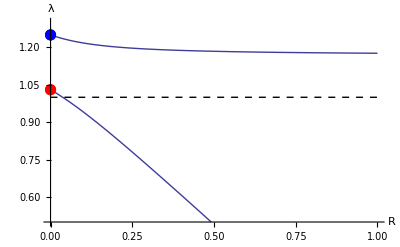

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot1=Show[
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.5,1.3}}],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion and that invasion is possible regardless of linkage, despite the fact that the neo-W will then be further from the selected locus.

#### Increasing recombination with r = R [No haploid selection] EXAMPLE STARTING NEAR EQUIL A

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.,0.,1.,0.5},{0.6,0.75,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.0037]
```

{{0.00615531,0.00679615,0.992554,0.5},{0.547933,0.692835,0.0408107,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[2]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.0303,1.25}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.0037,0.0001}]
```

{{1.0303,1.25},{1.02965,1.24916},{1.02899,1.24832},{1.02833,1.24747},{1.02766,1.24661},{1.02699,1.24575},{1.02631,1.24488},{1.02563,1.24401},{1.02494,1.24312},{1.02424,1.24223},{1.02353,1.24133},{1.02282,1.24042},{1.0221,1.2395},{1.02138,1.23857},{1.02064,1.23763},{1.01989,1.23667},{1.01914,1.2357},{1.01837,1.23472},{1.01759,1.23372},{1.01679,1.23271},{1.01599,1.23168},{1.01516,1.23063},{1.01432,1.22955},{1.01346,1.22846},{1.01258,1.22733},{1.01168,1.22618},{1.01075,1.22499},{1.00979,1.22376},{1.00879,1.22249},{1.00776,1.22116},{1.00667,1.21977},{1.00553,1.21831},{1.00431,1.21675},{1.003,1.21507},{1.00156,1.21322},{0.999922,1.21112},{0.997947,1.20858},{0.99511,1.20492}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.0037,0.0001}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.0037,0.0001}]},{Transpose[tab][[2]]}]];
```

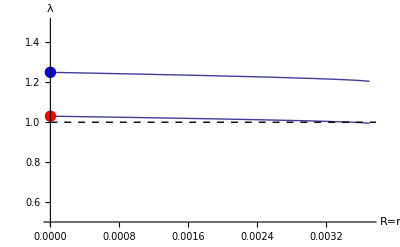

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.5,1.5}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion.  But the system switches to the other equilibrium at R=r=0.0038.

At R=r=0.0037, there are two equilibria (see ordering of equilibrium values):  
	* allele a is favored in females and A is favored in males 
	* allele a is favored in females and a is favored in males

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.0037]
```

{{0.00615531,0.00679615,0.992554,0.5},{0.547933,0.692835,0.0408107,0.5}}

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion.  But the system switches to the other equilibrium at R=r=0.0038.

At R=r=0.0038, only the first remains:
	* allele a is favored in females and A is favored in males

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.0038]
```

{{0.00632135,0.00698018,0.992352,0.5}}

At the first equilibrium, recombination is selected against in this example:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.761905,0.97619}

### Adding haploid selection to cases with pure sexually antagonistic selection

#### Pure sexually antagonistic selection [No haploid selection] -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable

```mathematica
sieve[tryFAA,tryFAa,0.5,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.876289,0.855131,0.,0.5}}

{0.89344-0.932299 R-1.89629 λ+1.01326 R λ+1. λ^2,1.02255,0.87374}

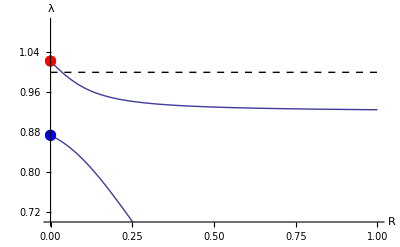

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot2=Show[
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.7,1.1}}],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible only for a modest range of R values (still, R>r so this runs counter to the expectations in van Doorn and Kirkpatrick).

#### Pure sexually antagonistic selection with meiotic drive -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.48;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.362667,0.312823,0.,0.506433}}

{0.994367-1.02231 R-1.99983 λ+1.07566 R λ+1. λ^2,1.07385,0.925985}

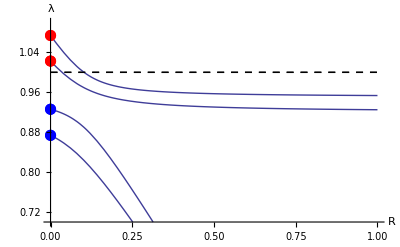

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot3=Show[
plot2,
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.7,1.1}},PlotStyle->Thick],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

With a male biased sex ratio (thick), the eigenvalues are slightly larger than with no haploid selection (thin), but the pattern is similar.

#### Increasing recombination with r = R [No haploid selection] EXAMPLE STARTING NEAR EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.664804,0.623037,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.269049,0.204077,0.204077,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02255,0.87374}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.87374,1.02255},{0.877268,1.02686},{0.879947,1.02901},{0.881772,1.02987},{0.882766,1.02986},{0.882963,1.02923},{0.882398,1.02816},{0.881108,1.02679},{0.879126,1.02523},{0.876489,1.02357},{0.87323,1.02187},{0.869383,1.02017},{0.864984,1.01853},{0.860067,1.01695},{0.854667,1.01546},{0.848819,1.01407},{0.842557,1.01279},{0.835912,1.0116},{0.828917,1.01052},{0.821601,1.00952},{0.813991,1.00862},{0.806112,1.0078},{0.797989,1.00706},{0.789641,1.00638},{0.781089,1.00577},{0.77235,1.00521},{0.76344,1.00471},{0.754373,1.00425},{0.745162,1.00384},{0.735819,1.00346},{0.726354,1.00312},{0.716778,1.0028},{0.707098,1.00252},{0.697322,1.00225},{0.687457,1.00202},{0.67751,1.0018},{0.667486,1.0016},{0.657391,1.00141},{0.647229,1.00124},{0.637006,1.00109},{0.626724,1.00095},{0.616387,1.00082},{0.606,1.00069},{0.595564,1.00058},{0.585083,1.00048},{0.57456,1.00038},{0.563997,1.00029},{0.553395,1.00021},{0.542758,1.00014},{0.532087,1.00007},{0.521383,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

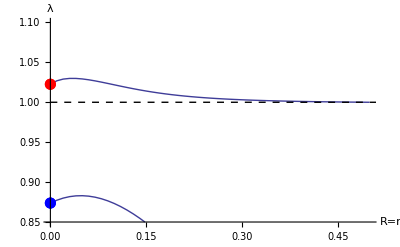

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.85,1.1}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for all R=r<1/2.

#### Increasing recombination with r = R with meiotic drive in the heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.566667,0.511278,0.,0.510429}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.155911,0.108125,0.108125,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.06485,0.898573}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.898573,1.06485},{0.900415,1.06514},{0.901889,1.06428},{0.902922,1.06264},{0.903481,1.06044},{0.903554,1.05783},{0.903135,1.05492},{0.902222,1.05182},{0.900813,1.0486},{0.898908,1.04533},{0.896508,1.04206},{0.893613,1.03885},{0.890228,1.03574},{0.886359,1.03275},{0.882016,1.02992},{0.877211,1.02726},{0.871962,1.02478},{0.866287,1.02248},{0.860208,1.02036},{0.853747,1.01842},{0.84693,1.01664},{0.83978,1.01503},{0.832321,1.01356},{0.824576,1.01224},{0.816567,1.01103},{0.808314,1.00994},{0.799837,1.00896},{0.791154,1.00806},{0.782281,1.00725},{0.773233,1.00652},{0.764023,1.00586},{0.754663,1.00525},{0.745165,1.0047},{0.735539,1.0042},{0.725795,1.00375},{0.715939,1.00333},{0.705981,1.00295},{0.695927,1.00261},{0.685783,1.00229},{0.675554,1.002},{0.665247,1.00174},{0.654866,1.00149},{0.644415,1.00127},{0.633899,1.00106},{0.62332,1.00087},{0.612683,1.00069},{0.60199,1.00053},{0.591245,1.00038},{0.58045,1.00025},{0.569608,1.00012},{0.55872,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

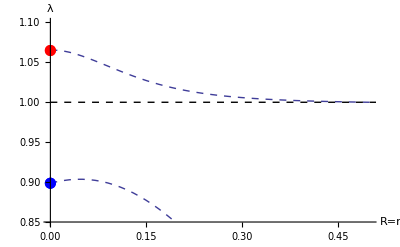

```mathematica
plot5=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.85,1.1}}],
ListPlot[eigen2,Joined->True,PlotStyle->Dashed],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for all R=r<1/2.

#### Increasing recombination with r = R with meiotic drive in the homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.52;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.873743,0.852223,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.421524,0.332718,0.332718,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.01701,0.852685}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.852685,1.01701},{0.853802,1.02448},{0.854965,1.02736},{0.855586,1.02862},{0.855552,1.02895},{0.854834,1.02865},{0.853437,1.02792},{0.851379,1.0269},{0.848689,1.02568},{0.8454,1.02435},{0.841545,1.02295},{0.83716,1.02153},{0.832281,1.02012},{0.826942,1.01875},{0.821178,1.01743},{0.815021,1.01617},{0.808502,1.01498},{0.801651,1.01386},{0.794494,1.01281},{0.787058,1.01183},{0.779366,1.01092},{0.771439,1.01007},{0.763298,1.00928},{0.754961,1.00855},{0.746445,1.00787},{0.737764,1.00724},{0.728932,1.00666},{0.719961,1.00611},{0.710863,1.00561},{0.701649,1.00514},{0.692326,1.00471},{0.682904,1.0043},{0.673391,1.00392},{0.663792,1.00357},{0.654115,1.00324},{0.644366,1.00293},{0.634548,1.00264},{0.624667,1.00237},{0.614728,1.00212},{0.604735,1.00188},{0.59469,1.00166},{0.584598,1.00144},{0.574461,1.00125},{0.564282,1.00106},{0.554064,1.00088},{0.54381,1.00071},{0.53352,1.00055},{0.523198,1.0004},{0.512845,1.00026},{0.502464,1.00013},{0.492055,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

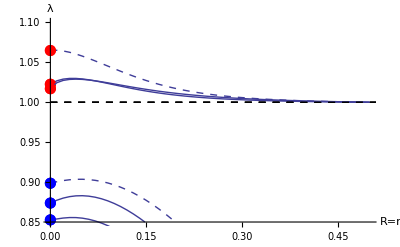

```mathematica
plot6=Show[
plot5,plot4,
ListPlot[eigen1,Joined->True],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

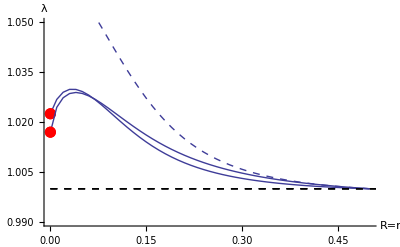

```mathematica
Show[%,PlotRange->{{0,0.5},{0.99,1.05}}]
```

The two thin curves converge with increasing recombination rate (consistent with α<1/2 in the heterogametic sex being equivalent to α>1/2 in the homogametic sex).  Setting tryαf=0.48 and reentering this section shows a much worse fit.

#### Increasing recombination with r = R [No haploid selection] EXAMPLE STARTING NEAR EQUIL B

The neo-W with allele A cannot invade in this example of sexually antagonistic selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.7;
tryMAA=0.9;
tryMAa=1;
tryMaa=1.1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.919462,0.901742,0.901742,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.954545,0.772727}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.772727,0.954545},{0.780853,0.964808},{0.787704,0.97175},{0.792794,0.976982},{0.796054,0.981064},{0.797558,0.984308},{0.79745,0.986921},{0.795908,0.989048},{0.793121,0.990795},{0.789275,0.992239},{0.784541,0.993439},{0.779068,0.99444},{0.772985,0.995277},{0.766402,0.995978},{0.759409,0.996567},{0.752079,0.997063},{0.744474,0.99748},{0.73664,0.997833},{0.728619,0.998131},{0.720441,0.998384},{0.712134,0.9986},{0.703718,0.998784},{0.69521,0.998942},{0.686624,0.999077},{0.677972,0.999194},{0.669264,0.999295},{0.660507,0.999382},{0.651709,0.999458},{0.642874,0.999524},{0.634007,0.999582},{0.625112,0.999633},{0.616193,0.999678},{0.607253,0.999717},{0.598293,0.999752},{0.589317,0.999783},{0.580325,0.99981},{0.57132,0.999834},{0.562303,0.999856},{0.553275,0.999875},{0.544236,0.999893},{0.535189,0.999908},{0.526134,0.999922},{0.517072,0.999935},{0.508002,0.999946},{0.498927,0.999956},{0.489846,0.999966},{0.48076,0.999974},{0.471669,0.999981},{0.462573,0.999988},{0.453474,0.999994},{0.44437,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

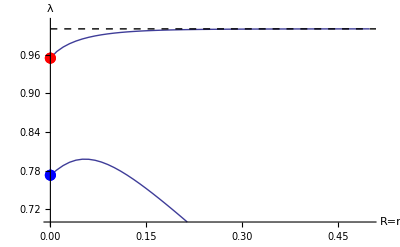

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.7,1.01}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick,PlotRange->All],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that invasion is not possible for all R=r<1/2.

#### Increasing recombination with r = R with meiotic drive in the heterogametic sex (causes a sex ratio distortion) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic selection (due to reducing the sex ratio skew).

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.7;
tryMAA=0.9;
tryMAa=1;
tryMaa=1.1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.52}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.765152,0.708242,0.708242,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.992424,0.799242}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.799242,0.992424},{0.800112,0.999653},{0.801934,1.0028},{0.80308,1.00458},{0.803282,1.00558},{0.802479,1.00607},{0.800687,1.00622},{0.797962,1.00616},{0.79438,1.00596},{0.790025,1.00568},{0.784983,1.00536},{0.779338,1.00502},{0.773168,1.00468},{0.766543,1.00435},{0.759527,1.00403},{0.752175,1.00374},{0.744535,1.00346},{0.736648,1.00321},{0.728551,1.00297},{0.720274,1.00275},{0.711842,1.00255},{0.703278,1.00237},{0.6946,1.00219},{0.685823,1.00203},{0.676961,1.00189},{0.668026,1.00175},{0.659026,1.00162},{0.649971,1.0015},{0.640868,1.00139},{0.631721,1.00128},{0.622538,1.00118},{0.613321,1.00109},{0.604075,1.001},{0.594803,1.00092},{0.585509,1.00084},{0.576194,1.00077},{0.56686,1.0007},{0.557511,1.00063},{0.548146,1.00057},{0.538769,1.00051},{0.52938,1.00045},{0.519979,1.0004},{0.510569,1.00035},{0.501151,1.0003},{0.491724,1.00025},{0.48229,1.0002},{0.472849,1.00016},{0.463402,1.00012},{0.453949,1.00008},{0.444491,1.00004},{0.435029,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

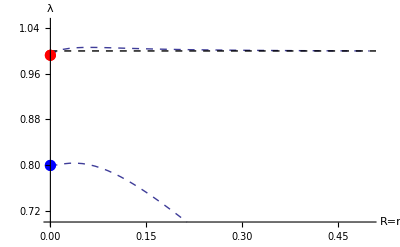

```mathematica
plot5=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.7,1.05}}],
ListPlot[eigen2,Joined->True,PlotStyle->Dashed],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for an intermediate range of R=r.

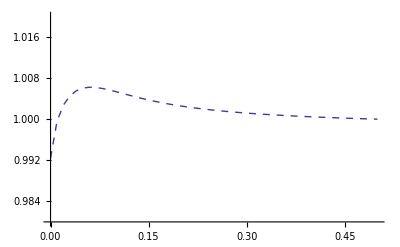

```mathematica
ListPlot[eigen2,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.98,1.02}}]
```

#### Increasing recombination with r = R with meiotic drive in the homogametic sex (causes a drive) EQUIL B

The neo-W with allele A cannot invade in this example of sexually antagonistic selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.7;
tryMAA=0.9;
tryMAa=1;
tryMaa=1.1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.52;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.25]
```

{{0.995002,0.993538,0.991715,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.972727,0.754545}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.25,0.01}]
```

{{0.754545,0.972727},{0.761738,0.97849},{0.767625,0.982844},{0.771978,0.986239},{0.774737,0.988926},{0.775941,0.991074},{0.775689,0.992806},{0.77412,0.994215},{0.771394,0.995368},{0.767672,0.996314},{0.763109,0.99709},{0.757847,0.997725},{0.752011,0.998242},{0.745707,0.998658},{0.739024,0.998991},{0.732036,0.999253},{0.724801,0.999457},{0.717368,0.999614},{0.709774,0.999733},{0.702048,0.999821},{0.694217,0.999885},{0.686297,0.99993},{0.678304,0.999961},{0.670251,0.99998},{0.662148,0.999992},{0.654001,0.999998}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.25,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.25,0.01}]},{Transpose[tab][[2]]}]];
```

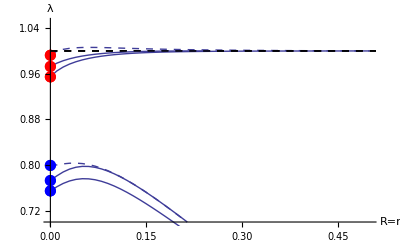

```mathematica
plot6=Show[
plot5,plot4,
ListPlot[eigen1,Joined->True],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

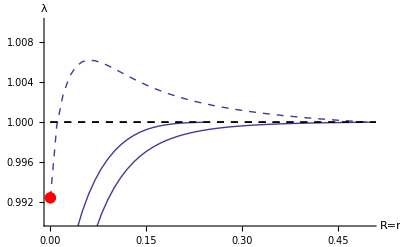

```mathematica
Show[%,PlotRange->{{0,0.5},{0.99,1.01}}]
```

The two thin curves converge with increasing recombination rate (consistent with α<1/2 in the heterogametic sex being equivalent to α>1/2 in the homogametic sex).  Setting tryαf=0.52 and reentering this section shows a much worse fit.

But for tight linkage, only the sex ratio advantage is strong enough to drive the neo-W in.

#### Increasing recombination r (R=0.1) [No haploid selection] EXAMPLE STARTING NEAR EQUIL A [Hard to interpret because changing r alters initial equilibrium]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.1;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilB0 is initially stable and a polymorphism is sustained for all r:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.532327,0.467673,0.467673,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.97619,0.857143}

These are the points at R=r=0.  For tryR, we assume that the association with A is still leading:

```mathematica
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{0.945275,0.79282}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.79282,0.945275},{0.799902,0.952754},{0.806588,0.960212},{0.812753,0.967272},{0.818309,0.973746},{0.823228,0.979551},{0.827531,0.984677},{0.831266,0.989162},{0.834498,0.993067},{0.837295,0.996462},{0.83972,0.999418},{0.84183,1.002},{0.843673,1.00426},{0.845292,1.00625},{0.84672,1.00801},{0.847986,1.00957},{0.849115,1.01096},{0.850125,1.01222},{0.851034,1.01334},{0.851855,1.01436},{0.852599,1.01528},{0.853277,1.01613},{0.853896,1.0169},{0.854464,1.0176},{0.854986,1.01825},{0.855467,1.01885},{0.855913,1.01941},{0.856326,1.01992},{0.85671,1.0204},{0.857068,1.02085},{0.857403,1.02127},{0.857715,1.02166},{0.858009,1.02203},{0.858285,1.02237},{0.858544,1.0227},{0.858789,1.023},{0.85902,1.02329},{0.859239,1.02357},{0.859446,1.02382},{0.859642,1.02407},{0.859828,1.0243},{0.860005,1.02453},{0.860174,1.02474},{0.860335,1.02494},{0.860488,1.02513},{0.860635,1.02531},{0.860775,1.02549},{0.860909,1.02566},{0.861037,1.02582},{0.86116,1.02597},{0.861278,1.02612}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

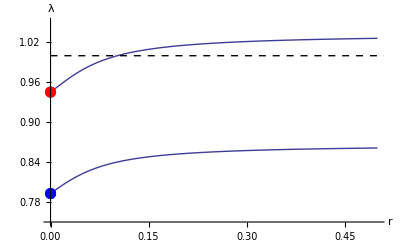

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.75,1.05}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

#### Increasing recombination r (R=0.1) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.49;
tryr=0;
tryR=0.1;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilB0 is initially stable and a polymorphism is sustained for all r:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.51}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.480398,0.411355,0.411355,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.995627,0.872692}

These are the points at R=r=0.  For tryR, we assume that the association with A is still leading:

```mathematica
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{0.963156,0.807981}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.807981,0.963156},{0.813556,0.968251},{0.81905,0.974042},{0.824177,0.979681},{0.828842,0.984944},{0.833016,0.989736},{0.836707,0.99403},{0.83995,0.997841},{0.842791,1.00121},{0.845279,1.00417},{0.847459,1.00679},{0.849376,1.00909},{0.851067,1.01114},{0.852565,1.01296},{0.853897,1.01458},{0.855087,1.01603},{0.856155,1.01734},{0.857116,1.01851},{0.857986,1.01958},{0.858775,1.02055},{0.859495,1.02144},{0.860152,1.02225},{0.860756,1.023},{0.861311,1.02368},{0.861823,1.02432},{0.862297,1.0249},{0.862737,1.02545},{0.863145,1.02596},{0.863526,1.02643},{0.863882,1.02687},{0.864216,1.02729},{0.864528,1.02768},{0.864822,1.02804},{0.865098,1.02839},{0.865359,1.02871},{0.865605,1.02902},{0.865837,1.02931},{0.866058,1.02958},{0.866267,1.02985},{0.866465,1.03009},{0.866654,1.03033},{0.866833,1.03055},{0.867005,1.03077},{0.867168,1.03097},{0.867324,1.03117},{0.867473,1.03136},{0.867616,1.03153},{0.867752,1.03171},{0.867883,1.03187},{0.868009,1.03203},{0.86813,1.03218}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

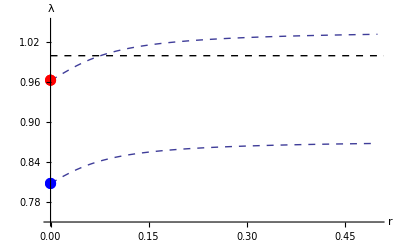

```mathematica
plot5=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.75,1.05}}],
ListPlot[eigen2,Joined->True,PlotStyle->Dashed],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

#### Increasing recombination r (R=0.1) with meiotic drive in homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.51;
tryαm=0.5;
tryr=0;
tryR=0.1;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilB0 is initially stable and a polymorphism is sustained for all r:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.588645,0.519602,0.519602,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.985714,0.847619}

These are the points at R=r=0.  For tryR, we assume that the association with A is still leading:

```mathematica
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{0.952136,0.78596}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.78596,0.952136},{0.791708,0.95851},{0.797393,0.965066},{0.802771,0.971411},{0.807716,0.977339},{0.812169,0.98274},{0.816118,0.987574},{0.819584,0.991848},{0.822608,0.995599},{0.82524,0.99888},{0.827531,1.00175},{0.829527,1.00425},{0.831272,1.00645},{0.832804,1.00838},{0.834153,1.01009},{0.835348,1.0116},{0.83641,1.01294},{0.837358,1.01415},{0.838208,1.01523},{0.838974,1.0162},{0.839667,1.01708},{0.840295,1.01788},{0.840867,1.01861},{0.841391,1.01928},{0.84187,1.01989},{0.842312,1.02046},{0.842719,1.02098},{0.843095,1.02146},{0.843444,1.0219},{0.843769,1.02232},{0.844071,1.0227},{0.844353,1.02306},{0.844617,1.0234},{0.844864,1.02372},{0.845097,1.02402},{0.845315,1.0243},{0.845521,1.02456},{0.845716,1.02481},{0.845899,1.02504},{0.846073,1.02527},{0.846238,1.02548},{0.846395,1.02568},{0.846543,1.02587},{0.846685,1.02605},{0.846819,1.02622},{0.846948,1.02639},{0.84707,1.02654},{0.847188,1.02669},{0.8473,1.02684},{0.847407,1.02697},{0.84751,1.02711}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

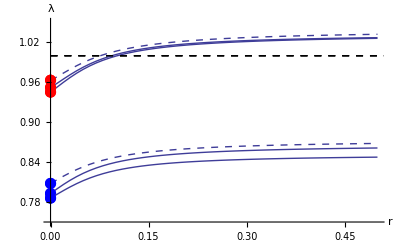

```mathematica
plot6=Show[
plot5,plot4,
ListPlot[eigen1,Joined->True],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"r","λ"},PlotRange->{{0,0.5},{0.75,1.05}}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

### Potential figure - Increasing recombination R (r=0.05 or 0.2)

#### Summary

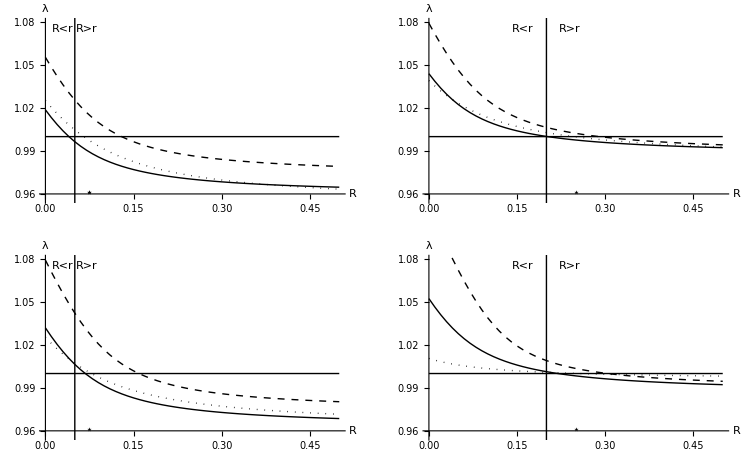

```mathematica
GraphicsGrid[{{plotA,plotB},{plotC,plotD}}]
```

```mathematica
Export["~/Desktop/Temp.pdf",%,ImageSize->Large];
```

Legend: Haploid selection and linkage both impact invasion of neo-W into XY sex dermination systems. Main panels plot the leading eigenvalue, λ, for a neo-W as a function of its distance, R, to the selected A locus: with only sexually antagonistic selection (thick curves), adding meiotic drive in males (dashed; αm=0.45); or adding meiotic drive in females (dashed; αf=0.55).  Either form of haploid selection increases the parameter space in which neo-W chromosomes invade (expanding when λ > 1).  Even in the absence of haploid selection, the condition of Van Doorn and Kirkpatrick for neo-W invasion is not satisfied if the sex determining region is initially tightly linked to the A locus (left panels: r = 0.05), but it is appoximately satisfied when linkage is loose (right panels: r=0.2), as seen by the thick curve hitting λ=1 at R = r (crossing thin lines). Inset panels show simulations for a neo-W that is more loosely linked than the original sex determining gene (R given by the asterisk), illustrating the frequency of the Y in males (upper green inset) and the frequency of males (bottom blue inset).  A neo-W that is less linked to the selected locus (R>r) can spread when it equalizes the sex ratio caused by meiotic drive in males (dashed curves) but also when it becomes associated with the driven allele in females, causing the sex ratio to become skewed (dotted curves).

TO DO:  Import into Adobe Illustrator.  Add panel labels and make dotted curves look more dotted.  Add xy-labels to the inset plots.  Top: x=1-500000 (log axis), y=0-1. Bottom: x=1-10000 (log axis), y=0.49-0.51 (left) and 0.498-0.502 (right).

POINT OUT IN TEXT:  
* In the appendix, it’s mentioned that with sexually antagonistic selection only and r tight at equil B (top plots), a neo-W cannot invade because “the X is already as possible for the female beneficial allele”.  This can be seen because the neo-W cannot invade with tight linkage near R=r in panel A (thick curve lies below λ=1). At equil A (bottom plots), a neo-W can spread because of the advantage of becoming better associated with the female beneficial allele (thick curve lies above λ=1).
* Panel D with meiotic drive in females (dashed; αf=0.55) is an example where neo-W spreads but does not fix.

Parameters: 
tryFAA=tryMaa=1.05;
tryFAa=1;
tryMAa=1 (top panels, equil near B) or 0.925 (bottom panels, equil near A)
tryFaa=tryMAA=0.85;
trywAf=trywaf=trywAm=trywam=1;
tryαf=0.5; [unless noted]
tryαm=0.5; [unless noted]

#### Increasing recombination R (r=0.05) [No haploid selection] EXAMPLE STARTING NEAR EQUIL B [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.671004,0.632712,0.241726,0.5}}

If R=r=0 (emanates from equilibrium B):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,1.,0.,0.5}

{0.97619,0.880952}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.0187,0.912751}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.912751,1.0187},{0.90816,1.01332},{0.903097,1.00842},{0.897565,1.00398},{0.891579,0.999997},{0.885162,0.996444},{0.878348,0.99329},{0.871172,0.990497},{0.863673,0.988027},{0.855888,0.985842},{0.847853,0.983908},{0.839599,0.982193},{0.831156,0.980667},{0.822549,0.979306},{0.813798,0.978087},{0.804924,0.976992},{0.795941,0.976006},{0.786864,0.975113},{0.777705,0.974303},{0.768474,0.973566},{0.759179,0.972892},{0.749827,0.972275},{0.740426,0.971707},{0.73098,0.971184},{0.721494,0.9707},{0.711973,0.970252},{0.70242,0.969836},{0.692838,0.969449},{0.68323,0.969088},{0.673599,0.96875},{0.663947,0.968433},{0.654274,0.968136},{0.644585,0.967857},{0.634878,0.967594},{0.625157,0.967346},{0.615423,0.967112},{0.605675,0.96689},{0.595916,0.96668},{0.586146,0.966481},{0.576367,0.966292},{0.566577,0.966112},{0.55678,0.96594},{0.546974,0.965777},{0.537161,0.965621},{0.527341,0.965472},{0.517514,0.96533},{0.507681,0.965193},{0.497843,0.965063},{0.487999,0.964938},{0.47815,0.964818},{0.468296,0.964702}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

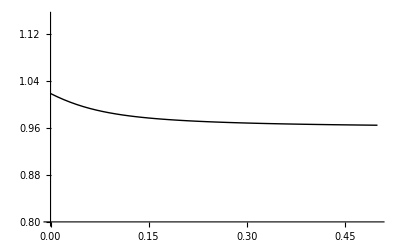

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

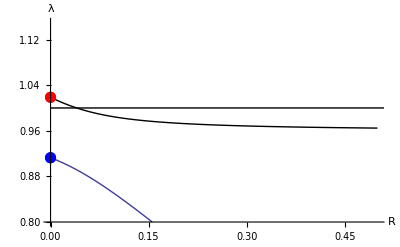

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504153},{6,0.504087},{6,0.504087},{7,0.504024},{7,0.504024},{8,0.503964},{9,0.503907},{10,0.503853},{11,0.503801},{12,0.503752},{14,0.503658},{15,0.503614},{17,0.503529},{18,0.503488},{20,0.503409},{22,0.503334},{25,0.503227},{27,0.503158},{30,0.503058},{33,0.502962},{37,0.50284},{41,0.502723},{45,0.502611},{50,0.502478},{55,0.502351},{61,0.502207},{67,0.502072},{74,0.501924},{82,0.501768},{91,0.501607},{100,0.501461},{111,0.5013},{123,0.501144},{136,0.500995},{150,0.500857},{166,0.500722},{183,0.500601},{202,0.50049},{224,0.500387},{247,0.500302},{273,0.500228},{302,0.500167},{333,0.500119},{368,0.500082},{407,0.500053},{450,0.500034},{497,0.50002},{550,0.500011},{608,0.500006},{671,0.500003},{742,0.500001},{820,0.500001},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

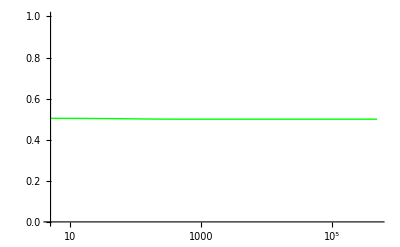

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.499687},{6,0.499719},{6,0.499719},{7,0.499746},{7,0.499746},{8,0.499771},{9,0.499792},{10,0.499811},{11,0.499827},{12,0.499842},{14,0.499866},{15,0.499876},{17,0.499894},{18,0.499901},{20,0.499913},{22,0.499924},{25,0.499935},{27,0.499942},{30,0.499949},{33,0.499954},{37,0.49996},{41,0.499964},{45,0.499967},{50,0.49997},{55,0.499972},{61,0.499974},{67,0.499976},{74,0.499978},{82,0.49998},{91,0.499981},{100,0.499983},{111,0.499985},{123,0.499987},{136,0.499988},{150,0.49999},{166,0.499992},{183,0.499993},{202,0.499994},{224,0.499995},{247,0.499996},{273,0.499997},{302,0.499998},{333,0.499999},{368,0.499999},{407,0.499999},{450,0.5},{497,0.5},{550,0.5},{608,0.5},{671,0.5},{742,0.5},{820,0.5},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

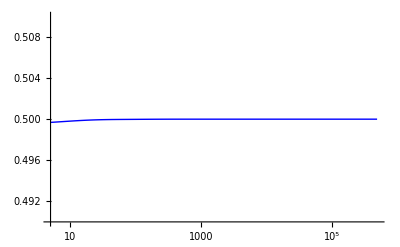

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.552535,0.503247,0.147601,0.509049}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02686,0.922851}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.05535,0.933026}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.933026,1.05535},{0.929481,1.04851},{0.925519,1.04209},{0.921112,1.03611},{0.916242,1.03059},{0.910902,1.02555},{0.905095,1.02097},{0.898836,1.01684},{0.892148,1.01314},{0.885062,1.00984},{0.877614,1.0069},{0.869839,1.00429},{0.861774,1.00197},{0.853453,0.999906},{0.844907,0.998065},{0.836165,0.996422},{0.827251,0.994949},{0.818187,0.993627},{0.808993,0.992435},{0.799684,0.991358},{0.790275,0.99038},{0.780778,0.989491},{0.771203,0.98868},{0.761559,0.987938},{0.751855,0.987256},{0.742096,0.986628},{0.732289,0.986049},{0.722439,0.985513},{0.71255,0.985015},{0.702627,0.984553},{0.692672,0.984122},{0.682688,0.983719},{0.672678,0.983343},{0.662645,0.98299},{0.65259,0.982658},{0.642516,0.982346},{0.632424,0.982052},{0.622315,0.981774},{0.612191,0.981512},{0.602053,0.981264},{0.591903,0.981028},{0.58174,0.980805},{0.571566,0.980593},{0.561382,0.980391},{0.551188,0.980198},{0.540985,0.980015},{0.530774,0.97984},{0.520555,0.979673},{0.510329,0.979513},{0.500096,0.979359},{0.489856,0.979213}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

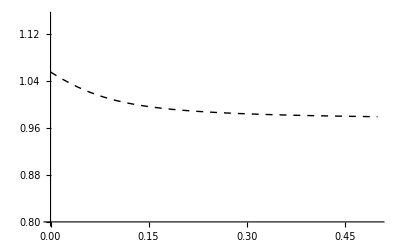

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

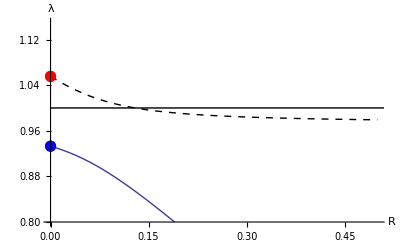

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.513565},{6,0.513571},{6,0.513571},{7,0.513582},{7,0.513582},{8,0.513598},{9,0.51362},{10,0.513646},{11,0.513676},{12,0.513711},{14,0.513791},{15,0.513836},{17,0.513936},{18,0.513989},{20,0.514104},{22,0.514229},{25,0.51443},{27,0.514574},{30,0.514803},{33,0.515047},{37,0.515394},{41,0.515765},{45,0.516161},{50,0.516691},{55,0.517262},{61,0.518004},{67,0.518812},{74,0.519845},{82,0.521157},{91,0.522817},{100,0.524695},{111,0.527322},{123,0.530659},{136,0.534911},{150,0.540334},{166,0.547756},{183,0.557258},{202,0.570047},{224,0.587852},{247,0.609736},{273,0.637659},{302,0.670886},{333,0.706149},{368,0.742885},{407,0.77822},{450,0.81016},{497,0.837823},{550,0.86196},{608,0.882111},{671,0.898771},{742,0.913036},{820,0.924935},{906,0.934939},{1002,0.943479},{1107,0.950655},{1223,0.956782},{1352,0.962066},{1494,0.966596},{1651,0.970515},{1825,0.973923},{2017,0.976886},{2229,0.979471},{2464,0.981743},{2723,0.983733},{3009,0.985485},{3326,0.987036},{3675,0.988403},{4062,0.98962},{4489,0.990698},{4961,0.991657},{5483,0.992512},{6060,0.993275},{6697,0.993955},{7401,0.994564},{8180,0.995109},{9040,0.995597},{9991,0.996034},{11042,0.996427},{12203,0.99678},{13486,0.997096},{14905,0.997381},{16472,0.997637},{18205,0.997868},{20119,0.998076},{22235,0.998263},{24574,0.998431},{27158,0.998583},{30015,0.99872},{33171,0.998844},{36660,0.998955},{40515,0.999056},{44776,0.999147},{49486,0.999229},{54690,0.999303},{60442,0.99937},{66799,0.99943},{73824,0.999485},{81588,0.999534},{90169,0.999579},{99652,0.999619},{110132,0.999656},{121715,0.999689},{134516,0.999718},{148663,0.999745},{164298,0.99977},{181578,0.999792},{200674,0.999811},{221779,0.999829},{245104,0.999846},{270882,0.99986},{299371,0.999874},{330856,0.999886},{365652,0.999897},{404108,0.999906},{446609,0.999915},{493579,0.999923}}

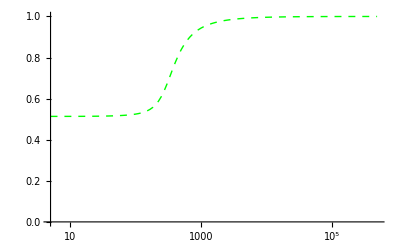

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.508365},{6,0.508383},{6,0.508383},{7,0.508398},{7,0.508398},{8,0.50841},{9,0.508419},{10,0.508426},{11,0.508431},{12,0.508434},{14,0.508436},{15,0.508436},{17,0.508433},{18,0.50843},{20,0.508423},{22,0.508413},{25,0.508396},{27,0.508383},{30,0.508361},{33,0.508336},{37,0.508301},{41,0.508261},{45,0.508219},{50,0.508161},{55,0.508098},{61,0.508017},{67,0.507929},{74,0.507816},{82,0.507675},{91,0.507499},{100,0.507303},{111,0.507034},{123,0.506703},{136,0.506297},{150,0.505803},{166,0.505168},{183,0.504422},{202,0.503527},{224,0.502468},{247,0.501431},{273,0.500463},{302,0.499732},{333,0.499332},{368,0.499202},{407,0.499248},{450,0.499368},{497,0.4995},{550,0.499617},{608,0.499711},{671,0.499782},{742,0.499836},{820,0.499877},{906,0.499906},{1002,0.499929},{1107,0.499946},{1223,0.499958},{1352,0.499968},{1494,0.499975},{1651,0.49998},{1825,0.499985},{2017,0.499988},{2229,0.49999},{2464,0.499992},{2723,0.499994},{3009,0.499995},{3326,0.499996},{3675,0.499997},{4062,0.499998},{4489,0.499998},{4961,0.499998},{5483,0.499999},{6060,0.499999},{6697,0.499999},{7401,0.499999},{8180,0.499999},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

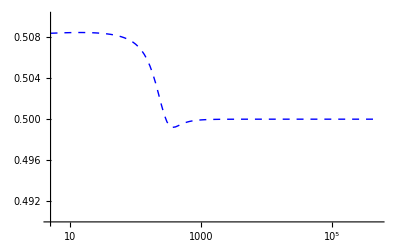

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in homogametic sex (causes a drive) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.807255,0.767691,0.280079,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,0.857143}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.02512,0.881007}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.881007,1.02512},{0.875983,1.0204},{0.870633,1.01601},{0.864963,1.01195},{0.858983,1.00819},{0.852706,1.00472},{0.846149,1.00154},{0.83933,0.998619},{0.832267,0.995943},{0.824979,0.993491},{0.817485,0.991245},{0.809804,0.989187},{0.801952,0.987299},{0.793944,0.985566},{0.785797,0.983974},{0.777523,0.982508},{0.769135,0.981157},{0.760643,0.979909},{0.752058,0.978754},{0.743388,0.977685},{0.734641,0.976691},{0.725825,0.975768},{0.716946,0.974907},{0.708009,0.974104},{0.69902,0.973354},{0.689983,0.972651},{0.680903,0.971992},{0.671782,0.971372},{0.662625,0.97079},{0.653434,0.970241},{0.644213,0.969723},{0.634962,0.969233},{0.625686,0.96877},{0.616384,0.968332},{0.607061,0.967916},{0.597716,0.967521},{0.588352,0.967145},{0.578969,0.966788},{0.56957,0.966447},{0.560155,0.966123},{0.550725,0.965813},{0.541282,0.965517},{0.531825,0.965233},{0.522357,0.964962},{0.512877,0.964702},{0.503386,0.964453},{0.493885,0.964214},{0.484375,0.963985},{0.474856,0.963764},{0.465329,0.963552},{0.455793,0.963347}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

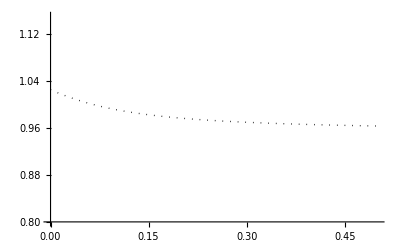

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

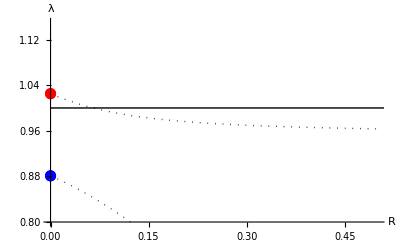

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504185},{6,0.504148},{6,0.504148},{7,0.504117},{7,0.504117},{8,0.50409},{9,0.504065},{10,0.504044},{11,0.504025},{12,0.504007},{14,0.503976},{15,0.503962},{17,0.503937},{18,0.503925},{20,0.503902},{22,0.503881},{25,0.50385},{27,0.50383},{30,0.5038},{33,0.50377},{37,0.503731},{41,0.503692},{45,0.503653},{50,0.503604},{55,0.503556},{61,0.503499},{67,0.503443},{74,0.503378},{82,0.503305},{91,0.503226},{100,0.503148},{111,0.503055},{123,0.502957},{136,0.502854},{150,0.502748},{166,0.50263},{183,0.502511},{202,0.502385},{224,0.502246},{247,0.502109},{273,0.501965},{302,0.501815},{333,0.501667},{368,0.501515},{407,0.501362},{450,0.50121},{497,0.501064},{550,0.50092},{608,0.500785},{671,0.50066},{742,0.500543},{820,0.500438},{906,0.500346},{1002,0.500266},{1107,0.500199},{1223,0.500145},{1352,0.500102},{1494,0.500069},{1651,0.500045},{1825,0.500028},{2017,0.500016},{2229,0.500009},{2464,0.500005},{2723,0.500002},{3009,0.500001},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

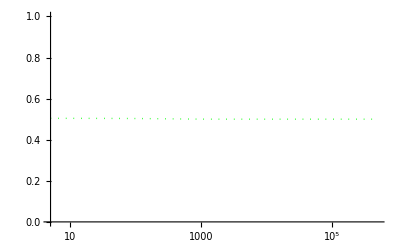

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.499374},{6,0.499397},{6,0.499397},{7,0.499418},{7,0.499418},{8,0.499437},{9,0.499455},{10,0.499471},{11,0.499486},{12,0.4995},{14,0.499525},{15,0.499536},{17,0.499555},{18,0.499564},{20,0.499579},{22,0.499592},{25,0.499608},{27,0.499617},{30,0.499628},{33,0.499637},{37,0.499647},{41,0.499655},{45,0.499661},{50,0.499667},{55,0.499673},{61,0.499679},{67,0.499685},{74,0.499691},{82,0.499697},{91,0.499704},{100,0.499711},{111,0.49972},{123,0.499728},{136,0.499738},{150,0.499747},{166,0.499758},{183,0.499768},{202,0.49978},{224,0.499792},{247,0.499805},{273,0.499818},{302,0.499832},{333,0.499845},{368,0.499859},{407,0.499873},{450,0.499887},{497,0.499901},{550,0.499914},{608,0.499926},{671,0.499938},{742,0.499949},{820,0.499959},{906,0.499967},{1002,0.499975},{1107,0.499981},{1223,0.499986},{1352,0.49999},{1494,0.499994},{1651,0.499996},{1825,0.499997},{2017,0.499998},{2229,0.499999},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

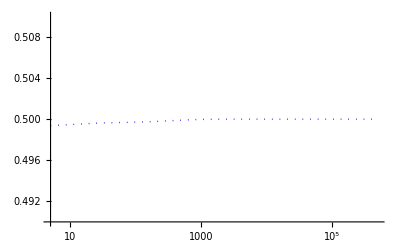

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dotted,Blue}]
```

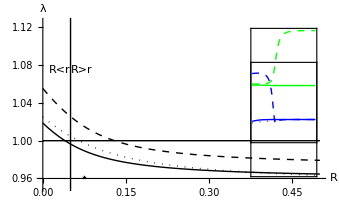

```mathematica
plotA=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.05,0},{0.05,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.03,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.07,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

#### Increasing recombination R (r=0.2) [No haploid selection] EXAMPLE STARTING NEAR EQUIL B [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.549741,0.500248,0.421738,0.5}}

If R=r=0 (emanates from equilibrium B):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,1.,0,0.5}

{0.97619,0.880952}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.04393,0.937909}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.937909,1.04393},{0.93296,1.03868},{0.92752,1.03391},{0.921597,1.02963},{0.915214,1.02581},{0.908402,1.02242},{0.901197,1.01942},{0.893641,1.01677},{0.885772,1.01443},{0.877631,1.01237},{0.869251,1.01055},{0.860665,1.00893},{0.8519,1.00749},{0.84298,1.00621},{0.833926,1.00506},{0.824756,1.00402},{0.815485,1.00309},{0.806126,1.00224},{0.796689,1.00148},{0.787184,1.00078},{0.77762,1.00014},{0.768003,0.999551},{0.758339,0.999011},{0.748633,0.998512},{0.73889,0.998051},{0.729113,0.997624},{0.719307,0.997227},{0.709473,0.996856},{0.699615,0.996511},{0.689734,0.996187},{0.679833,0.995884},{0.669914,0.995599},{0.659978,0.995331},{0.650026,0.995078},{0.64006,0.99484},{0.630082,0.994615},{0.620091,0.994401},{0.610089,0.994199},{0.600077,0.994007},{0.590055,0.993825},{0.580025,0.993651},{0.569986,0.993486},{0.55994,0.993328},{0.549886,0.993177},{0.539826,0.993033},{0.529759,0.992896},{0.519687,0.992764},{0.509609,0.992638},{0.499526,0.992517},{0.489439,0.9924},{0.479346,0.992289}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

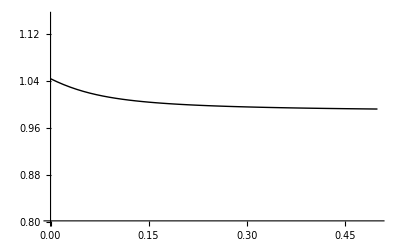

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

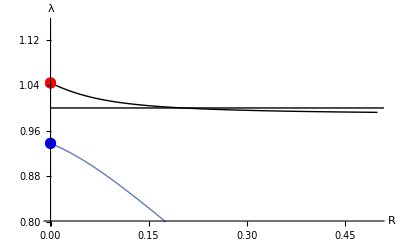

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

$Aborted

{{5,0.504592},{6,0.504628},{6,0.504628},{7,0.504647},{7,0.504647},{8,0.504656},{9,0.504658},{10,0.504656},{11,0.504651},{12,0.504644},{14,0.504627},{15,0.504617},{17,0.504598},{18,0.504588},{20,0.504568},{22,0.504548},{25,0.504518},{27,0.504498},{30,0.504469},{33,0.504439},{37,0.5044},{41,0.504361},{45,0.504323},{50,0.504275},{55,0.504228},{61,0.504172},{67,0.504117},{74,0.504053},{82,0.503982},{91,0.503903},{100,0.503825},{111,0.503732},{123,0.503634},{136,0.503529},{150,0.50342},{166,0.503299},{183,0.503175},{202,0.503042},{224,0.502894},{247,0.502746},{273,0.502589},{302,0.502423},{333,0.502257},{368,0.502083},{407,0.501904},{450,0.501724},{497,0.501546},{550,0.501367},{608,0.501194},{671,0.501031},{742,0.500873},{820,0.500727},{906,0.500594},{1002,0.500473},{1107,0.500369},{1223,0.500281},{1352,0.500207},{1494,0.500148},{1651,0.500102},{1825,0.500067},{2017,0.500043},{2229,0.500026},{2464,0.500015},{2723,0.500008},{3009,0.500004},{3326,0.500002},{3675,0.500001},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

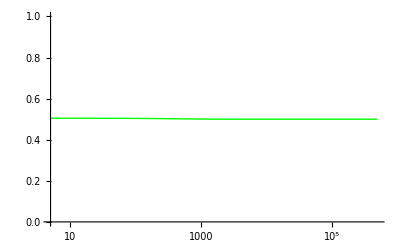

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.499612},{6,0.499742},{6,0.499742},{7,0.499827},{7,0.499827},{8,0.499882},{9,0.499918},{10,0.499942},{11,0.499958},{12,0.499968},{14,0.499979},{15,0.499982},{17,0.499985},{18,0.499986},{20,0.499987},{22,0.499987},{25,0.499988},{27,0.499988},{30,0.499988},{33,0.499988},{37,0.499988},{41,0.499988},{45,0.499988},{50,0.499988},{55,0.499988},{61,0.499989},{67,0.499989},{74,0.499989},{82,0.499989},{91,0.499989},{100,0.499989},{111,0.49999},{123,0.49999},{136,0.49999},{150,0.499991},{166,0.499991},{183,0.499991},{202,0.499992},{224,0.499992},{247,0.499992},{273,0.499993},{302,0.499993},{333,0.499994},{368,0.499994},{407,0.499995},{450,0.499995},{497,0.499996},{550,0.499996},{608,0.499997},{671,0.499997},{742,0.499997},{820,0.499998},{906,0.499998},{1002,0.499999},{1107,0.499999},{1223,0.499999},{1352,0.499999},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

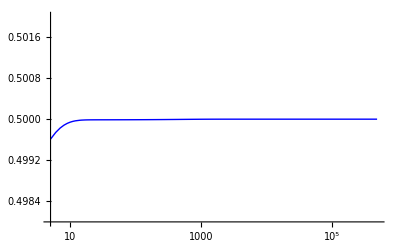

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.381667,0.326267,0.249116,0.501971}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02686,0.922851}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.0791,0.950121}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.950121,1.0791},{0.946876,1.07171},{0.943235,1.06471},{0.939164,1.05815},{0.934636,1.05204},{0.929632,1.0464},{0.924145,1.04125},{0.918178,1.03658},{0.911747,1.03237},{0.904877,1.0286},{0.897601,1.02524},{0.889954,1.02225},{0.881973,1.01959},{0.873696,1.01723},{0.865158,1.01513},{0.856392,1.01326},{0.847425,1.01159},{0.838283,1.01009},{0.82899,1.00875},{0.819563,1.00754},{0.81002,1.00644},{0.800374,1.00545},{0.79064,1.00455},{0.780826,1.00372},{0.770943,1.00297},{0.760997,1.00227},{0.750997,1.00164},{0.740948,1.00105},{0.730855,1.0005},{0.720722,0.999998},{0.710554,0.999528},{0.700354,0.99909},{0.690125,0.998681},{0.67987,0.998298},{0.669591,0.997939},{0.65929,0.997602},{0.648969,0.997285},{0.638629,0.996986},{0.628273,0.996704},{0.617902,0.996437},{0.607516,0.996185},{0.597117,0.995946},{0.586706,0.995718},{0.576284,0.995503},{0.565851,0.995297},{0.555409,0.995102},{0.544957,0.994915},{0.534497,0.994737},{0.524029,0.994567},{0.513554,0.994404},{0.503072,0.994248}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

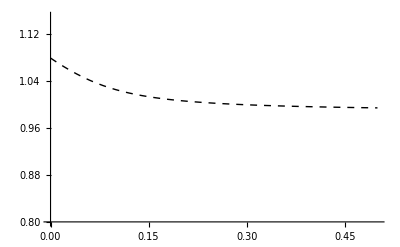

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

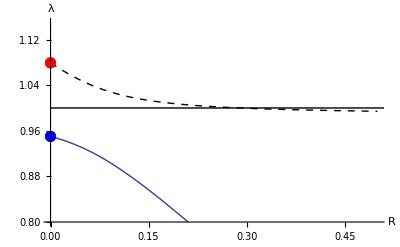

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.506603},{6,0.506654},{6,0.506654},{7,0.50669},{7,0.50669},{8,0.506716},{9,0.506737},{10,0.506753},{11,0.506767},{12,0.50678},{14,0.506804},{15,0.506815},{17,0.506837},{18,0.506848},{20,0.506871},{22,0.506893},{25,0.506927},{27,0.506949},{30,0.506984},{33,0.507018},{37,0.507065},{41,0.507111},{45,0.507159},{50,0.507219},{55,0.507279},{61,0.507353},{67,0.507427},{74,0.507516},{82,0.507618},{91,0.507736},{100,0.507857},{111,0.508007},{123,0.508176},{136,0.508364},{150,0.508573},{166,0.50882},{183,0.509094},{202,0.509412},{224,0.509798},{247,0.510224},{273,0.510734},{302,0.51134},{333,0.512035},{368,0.512882},{407,0.513912},{450,0.515161},{497,0.516679},{550,0.518602},{608,0.521},{671,0.523999},{742,0.52795},{820,0.533103},{906,0.539947},{1002,0.549279},{1107,0.561853},{1223,0.578938},{1352,0.601913},{1494,0.631249},{1651,0.66639},{1825,0.705129},{2017,0.744128},{2229,0.78068},{2464,0.813314},{2723,0.841329},{3009,0.864979},{3326,0.88483},{3675,0.901332},{4062,0.915163},{4489,0.926731},{4961,0.936467},{5483,0.944704},{6060,0.951703},{6697,0.957673},{7401,0.962796},{8180,0.967216},{9040,0.971036},{9991,0.974356},{11042,0.97725},{12203,0.97978},{13486,0.981999},{14905,0.983953},{16472,0.985673},{18205,0.987195},{20119,0.988542},{22235,0.989737},{24574,0.9908},{27158,0.991745},{30015,0.992588},{33171,0.99334},{36660,0.994012},{40515,0.994613},{44776,0.995152},{49486,0.995635},{54690,0.996067},{60442,0.996456},{66799,0.996805},{73824,0.997119},{81588,0.997401},{90169,0.997655},{99652,0.997884},{110132,0.998089},{121715,0.998275},{134516,0.998442},{148663,0.998593},{164298,0.998729},{181578,0.998852},{200674,0.998962},{221779,0.999062},{245104,0.999152},{270882,0.999234},{299371,0.999307},{330856,0.999374},{365652,0.999434},{404108,0.999488},{446609,0.999537},{493579,0.999581}}

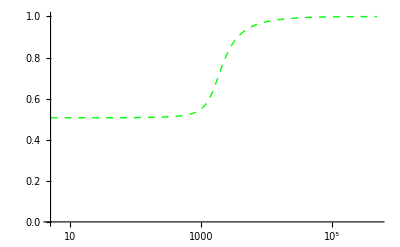

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.501471},{6,0.501597},{6,0.501597},{7,0.501679},{7,0.501679},{8,0.501732},{9,0.501766},{10,0.501788},{11,0.501802},{12,0.501811},{14,0.50182},{15,0.501822},{17,0.501824},{18,0.501825},{20,0.501825},{22,0.501824},{25,0.501823},{27,0.501823},{30,0.501822},{33,0.501821},{37,0.501819},{41,0.501818},{45,0.501816},{50,0.501815},{55,0.501813},{61,0.501811},{67,0.501809},{74,0.501806},{82,0.501803},{91,0.5018},{100,0.501796},{111,0.501792},{123,0.501787},{136,0.501782},{150,0.501776},{166,0.501769},{183,0.501761},{202,0.501752},{224,0.501742},{247,0.50173},{273,0.501716},{302,0.501699},{333,0.50168},{368,0.501658},{407,0.50163},{450,0.501598},{497,0.501559},{550,0.501511},{608,0.501452},{671,0.501382},{742,0.501293},{820,0.501184},{906,0.50105},{1002,0.500885},{1107,0.500691},{1223,0.500476},{1352,0.500255},{1494,0.500062},{1651,0.499929},{1825,0.499863},{2017,0.49985},{2229,0.499866},{2464,0.49989},{2723,0.499915},{3009,0.499935},{3326,0.499951},{3675,0.499964},{4062,0.499973},{4489,0.499979},{4961,0.499984},{5483,0.499988},{6060,0.499991},{6697,0.499993},{7401,0.499995},{8180,0.499996},{9040,0.499997},{9991,0.499997},{11042,0.499998},{12203,0.499998},{13486,0.499999},{14905,0.499999},{16472,0.499999},{18205,0.499999},{20119,0.499999},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

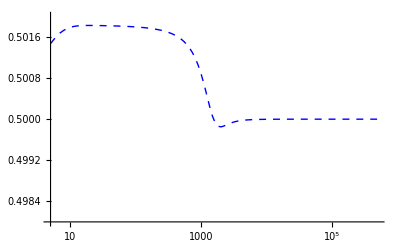

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in homogametic sex (causes a drive) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.723464,0.668989,0.573869,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,0.857143}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.03912,0.902693}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.902693,1.03912},{0.896684,1.03535},{0.890355,1.03191},{0.883725,1.02876},{0.876814,1.0259},{0.869645,1.02329},{0.86224,1.02092},{0.854621,1.01876},{0.846808,1.0168},{0.838821,1.01501},{0.830678,1.01337},{0.822394,1.01188},{0.813984,1.01052},{0.805461,1.00926},{0.796837,1.00811},{0.788122,1.00705},{0.779326,1.00607},{0.770456,1.00516},{0.76152,1.00432},{0.752524,1.00354},{0.743474,1.00282},{0.734375,1.00214},{0.725231,1.00151},{0.716047,1.00091},{0.706825,1.00036},{0.69757,0.999839},{0.688284,0.999349},{0.678969,0.998887},{0.669628,0.998452},{0.660263,0.99804},{0.650876,0.997651},{0.641468,0.997283},{0.632042,0.996933},{0.622597,0.996601},{0.613137,0.996286},{0.603661,0.995986},{0.594171,0.995699},{0.584667,0.995426},{0.575152,0.995166},{0.565624,0.994917},{0.556086,0.994679},{0.546538,0.994451},{0.536981,0.994232},{0.527414,0.994022},{0.517839,0.993821},{0.508256,0.993628},{0.498665,0.993442},{0.489068,0.993264},{0.479464,0.993092},{0.469853,0.992926},{0.460237,0.992766}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

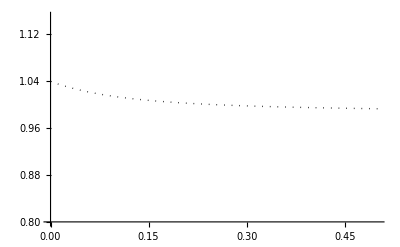

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

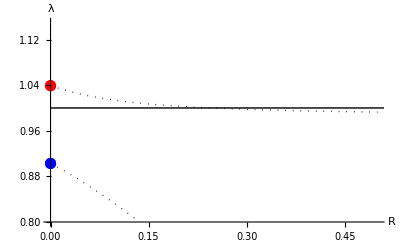

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504623},{6,0.50467},{6,0.50467},{7,0.5047},{7,0.5047},{8,0.50472},{9,0.504732},{10,0.50474},{11,0.504746},{12,0.504749},{14,0.504752},{15,0.504753},{17,0.504754},{18,0.504754},{20,0.504753},{22,0.504753},{25,0.504752},{27,0.504751},{30,0.50475},{33,0.50475},{37,0.504748},{41,0.504747},{45,0.504746},{50,0.504744},{55,0.504743},{61,0.504741},{67,0.504739},{74,0.504737},{82,0.504734},{91,0.504731},{100,0.504729},{111,0.504725},{123,0.504721},{136,0.504717},{150,0.504713},{166,0.504708},{183,0.504702},{202,0.504696},{224,0.504689},{247,0.504682},{273,0.504674},{302,0.504665},{333,0.504655},{368,0.504644},{407,0.504631},{450,0.504617},{497,0.504602},{550,0.504585},{608,0.504567},{671,0.504547},{742,0.504524},{820,0.504499},{906,0.504471},{1002,0.50444},{1107,0.504407},{1223,0.504369},{1352,0.504328},{1494,0.504282},{1651,0.504231},{1825,0.504174},{2017,0.504112},{2229,0.504043},{2464,0.503967},{2723,0.503883},{3009,0.503791},{3326,0.503688},{3675,0.503576},{4062,0.503453},{4489,0.503318},{4961,0.503171},{5483,0.503012},{6060,0.502839},{6697,0.502654},{7401,0.502456},{8180,0.502248},{9040,0.502031},{9991,0.501808},{11042,0.501582},{12203,0.501358},{13486,0.50114},{14905,0.500935},{16472,0.500745},{18205,0.500577},{20119,0.500432},{22235,0.500312},{24574,0.500216},{27158,0.500144},{30015,0.500091},{33171,0.500055},{36660,0.500031},{40515,0.500017},{44776,0.500009},{49486,0.500004},{54690,0.500002},{60442,0.500001},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

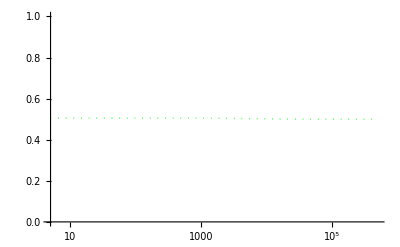

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.499542},{6,0.499672},{6,0.499672},{7,0.499757},{7,0.499757},{8,0.499813},{9,0.49985},{10,0.499874},{11,0.49989},{12,0.499901},{14,0.499912},{15,0.499916},{17,0.499919},{18,0.49992},{20,0.499921},{22,0.499921},{25,0.499922},{27,0.499922},{30,0.499922},{33,0.499922},{37,0.499922},{41,0.499922},{45,0.499922},{50,0.499922},{55,0.499922},{61,0.499922},{67,0.499922},{74,0.499922},{82,0.499922},{91,0.499922},{100,0.499922},{111,0.499922},{123,0.499922},{136,0.499922},{150,0.499922},{166,0.499923},{183,0.499923},{202,0.499923},{224,0.499923},{247,0.499923},{273,0.499923},{302,0.499923},{333,0.499923},{368,0.499924},{407,0.499924},{450,0.499924},{497,0.499924},{550,0.499924},{608,0.499925},{671,0.499925},{742,0.499925},{820,0.499926},{906,0.499926},{1002,0.499927},{1107,0.499927},{1223,0.499928},{1352,0.499929},{1494,0.499929},{1651,0.49993},{1825,0.499931},{2017,0.499932},{2229,0.499933},{2464,0.499934},{2723,0.499936},{3009,0.499937},{3326,0.499939},{3675,0.499941},{4062,0.499943},{4489,0.499945},{4961,0.499947},{5483,0.49995},{6060,0.499953},{6697,0.499956},{7401,0.499959},{8180,0.499962},{9040,0.499966},{9991,0.49997},{11042,0.499973},{12203,0.499977},{13486,0.499981},{14905,0.499984},{16472,0.499987},{18205,0.49999},{20119,0.499993},{22235,0.499995},{24574,0.499996},{27158,0.499998},{30015,0.499998},{33171,0.499999},{36660,0.499999},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

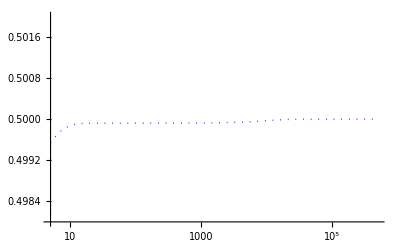

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dotted,Blue}]
```

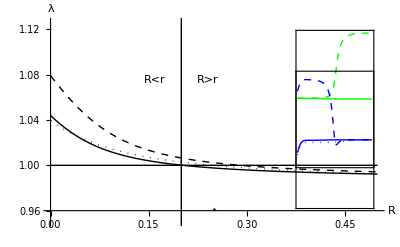

```mathematica
plotB=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.2,0},{0.2,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.25,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.16,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.24,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

#### Increasing recombination R (r=0.05) [No haploid selection] EXAMPLE STARTING NEAR EQUIL A [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.388403,0.332958,0.0906601,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.615385,0.571429,0,0.5}

{1.02158,0.899281}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.0691,0.932823}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.932823,1.0691},{0.930439,1.06091},{0.927742,1.05302},{0.924692,1.04549},{0.921249,1.03836},{0.917374,1.03165},{0.913035,1.02541},{0.908208,1.01966},{0.902881,1.01441},{0.897055,1.00966},{0.890743,1.00539},{0.883972,1.00158},{0.876775,0.998201},{0.86919,0.995207},{0.861258,0.992559},{0.85302,0.990219},{0.844512,0.988147},{0.83577,0.98631},{0.826825,0.984677},{0.817702,0.983221},{0.808426,0.981917},{0.799018,0.980747},{0.789493,0.979693},{0.779867,0.97874},{0.770153,0.977875},{0.760361,0.977088},{0.750501,0.976369},{0.740581,0.97571},{0.730607,0.975105},{0.720586,0.974547},{0.710522,0.974032},{0.700421,0.973555},{0.690285,0.973111},{0.680118,0.972699},{0.669924,0.972314},{0.659705,0.971955},{0.649463,0.971618},{0.6392,0.971302},{0.628918,0.971005},{0.618618,0.970725},{0.608303,0.970461},{0.597973,0.970212},{0.58763,0.969976},{0.577275,0.969753},{0.566907,0.969541},{0.55653,0.96934},{0.546142,0.969149},{0.535745,0.968967},{0.52534,0.968793},{0.514926,0.968627},{0.504506,0.968469}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

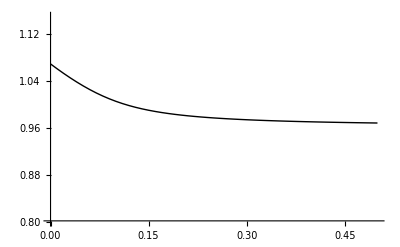

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

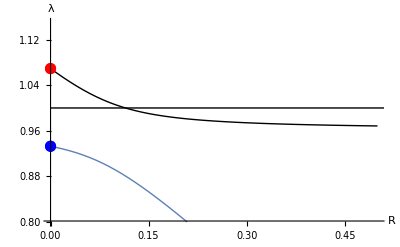

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504383},{6,0.504355},{6,0.504355},{7,0.504335},{7,0.504335},{8,0.504323},{9,0.504319},{10,0.504321},{11,0.50433},{12,0.504345},{14,0.504392},{15,0.504422},{17,0.504498},{18,0.504542},{20,0.504641},{22,0.504754},{25,0.504947},{27,0.505089},{30,0.505322},{33,0.505576},{37,0.505945},{41,0.506348},{45,0.506785},{50,0.507381},{55,0.508033},{61,0.508897},{67,0.509856},{74,0.511111},{82,0.512745},{91,0.514877},{100,0.51737},{111,0.520998},{123,0.525829},{136,0.532314},{150,0.541071},{166,0.553799},{183,0.571007},{202,0.594954},{224,0.627885},{247,0.665168},{273,0.706065},{302,0.746252},{333,0.781759},{368,0.813654},{407,0.841187},{450,0.864385},{497,0.883679},{550,0.900185},{608,0.913888},{671,0.925253},{742,0.935066},{820,0.943345},{906,0.950395},{1002,0.956495},{1107,0.961687},{1223,0.966176},{1352,0.970095},{1494,0.973492},{1651,0.976461},{1825,0.979068},{2017,0.981354},{2229,0.983366},{2464,0.985147},{2723,0.986717},{3009,0.988108},{3326,0.989347},{3675,0.990444},{4062,0.991425},{4489,0.992298},{4961,0.993078},{5483,0.993776},{6060,0.9944},{6697,0.994959},{7401,0.99546},{8180,0.99591},{9040,0.996313},{9991,0.996676},{11042,0.997003},{12203,0.997296},{13486,0.99756},{14905,0.997798},{16472,0.998012},{18205,0.998205},{20119,0.998379},{22235,0.998535},{24574,0.998677},{27158,0.998805},{30015,0.99892},{33171,0.999024},{36660,0.999118},{40515,0.999202},{44776,0.999279},{49486,0.999348},{54690,0.999411},{60442,0.999467},{66799,0.999518},{73824,0.999564},{81588,0.999606},{90169,0.999644},{99652,0.999678},{110132,0.999708},{121715,0.999736},{134516,0.999761},{148663,0.999784},{164298,0.999805},{181578,0.999823},{200674,0.99984},{221779,0.999856},{245104,0.999869},{270882,0.999882},{299371,0.999893},{330856,0.999903},{365652,0.999912},{404108,0.999921},{446609,0.999928},{493579,0.999935}}

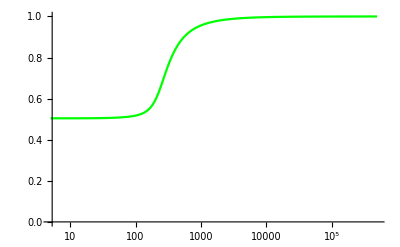

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.499742},{6,0.499764},{6,0.499764},{7,0.499783},{7,0.499783},{8,0.499798},{9,0.49981},{10,0.49982},{11,0.499829},{12,0.499836},{14,0.499847},{15,0.499852},{17,0.499859},{18,0.499862},{20,0.499866},{22,0.49987},{25,0.499874},{27,0.499876},{30,0.499878},{33,0.499879},{37,0.499879},{41,0.499878},{45,0.499875},{50,0.499869},{55,0.499861},{61,0.49985},{67,0.499836},{74,0.499816},{82,0.499789},{91,0.499751},{100,0.499707},{111,0.49964},{123,0.499548},{136,0.499422},{150,0.49925},{166,0.499002},{183,0.498688},{202,0.49832},{224,0.497992},{247,0.49789},{273,0.498052},{302,0.498385},{333,0.498735},{368,0.499048},{407,0.499296},{450,0.499482},{497,0.499617},{550,0.499717},{608,0.499789},{671,0.499841},{742,0.49988},{820,0.499909},{906,0.49993},{1002,0.499946},{1107,0.499958},{1223,0.499968},{1352,0.499975},{1494,0.49998},{1651,0.499984},{1825,0.499988},{2017,0.49999},{2229,0.499992},{2464,0.499994},{2723,0.499995},{3009,0.499996},{3326,0.499997},{3675,0.499997},{4062,0.499998},{4489,0.499998},{4961,0.499999},{5483,0.499999},{6060,0.499999},{6697,0.499999},{7401,0.499999},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

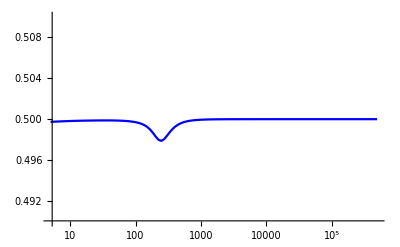

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.228038,0.181621,0.0392766,0.503703}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.08056,0.9388}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.11649,0.962136}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.962136,1.11649},{0.960833,1.10669},{0.959344,1.09707},{0.957634,1.08768},{0.955663,1.07855},{0.953381,1.06972},{0.950733,1.06127},{0.94766,1.05324},{0.944099,1.04569},{0.93999,1.0387},{0.935286,1.0323},{0.929953,1.02653},{0.923985,1.02139},{0.917396,1.01688},{0.910225,1.01295},{0.902525,1.00954},{0.894355,1.00661},{0.885779,1.00408},{0.876855,1.0019},{0.867637,1.00001},{0.85817,0.998378},{0.848494,0.99695},{0.838642,0.995698},{0.828641,0.994595},{0.818514,0.993618},{0.80828,0.992748},{0.797954,0.991971},{0.787549,0.991272},{0.777076,0.990641},{0.766544,0.990069},{0.75596,0.989549},{0.745331,0.989074},{0.734662,0.988639},{0.723959,0.988239},{0.713224,0.98787},{0.702461,0.987529},{0.691673,0.987213},{0.680863,0.986919},{0.670033,0.986645},{0.659185,0.986389},{0.648321,0.98615},{0.637441,0.985925},{0.626548,0.985715},{0.615643,0.985516},{0.604726,0.985329},{0.593798,0.985153},{0.582862,0.984986},{0.571916,0.984827},{0.560962,0.984678},{0.550001,0.984535},{0.539032,0.9844}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

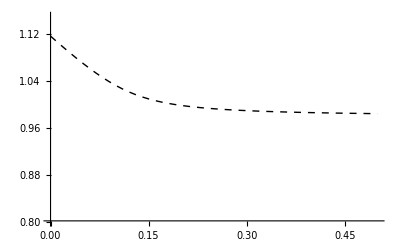

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

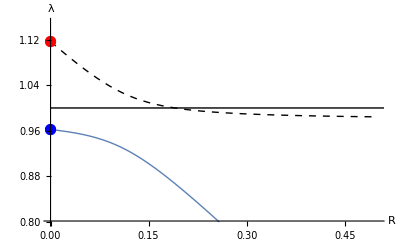

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.508361},{6,0.508392},{6,0.508392},{7,0.508433},{7,0.508433},{8,0.508485},{9,0.508547},{10,0.508622},{11,0.508707},{12,0.508805},{14,0.509037},{15,0.509171},{17,0.50948},{18,0.509654},{20,0.510044},{22,0.510492},{25,0.511281},{27,0.511889},{30,0.512936},{33,0.514157},{37,0.516088},{41,0.518407},{45,0.521165},{50,0.525312},{55,0.530339},{61,0.537672},{67,0.546546},{74,0.558914},{82,0.57555},{91,0.59679},{100,0.619552},{111,0.647605},{123,0.676636},{136,0.705051},{150,0.731859},{166,0.758116},{183,0.781695},{202,0.803779},{224,0.824904},{247,0.843033},{273,0.859808},{302,0.875},{333,0.888171},{368,0.900212},{407,0.911021},{450,0.920606},{497,0.929038},{550,0.936683},{608,0.943403},{671,0.949285},{742,0.954627},{820,0.959353},{906,0.963556},{1002,0.967339},{1107,0.970679},{1223,0.973662},{1352,0.976346},{1494,0.978736},{1651,0.980877},{1825,0.982799},{2017,0.984519},{2229,0.98606},{2464,0.987447},{2723,0.988689},{3009,0.989804},{3326,0.990809},{3675,0.991709},{4062,0.992522},{4489,0.993253},{4961,0.993911},{5483,0.994504},{6060,0.995038},{6697,0.995519},{7401,0.995953},{8180,0.996345},{9040,0.996698},{9991,0.997017},{11042,0.997304},{12203,0.997564},{13486,0.997798},{14905,0.99801},{16472,0.998201},{18205,0.998374},{20119,0.998529},{22235,0.99867},{24574,0.998798},{27158,0.998913},{30015,0.999017},{33171,0.999111},{36660,0.999196},{40515,0.999273},{44776,0.999342},{49486,0.999405},{54690,0.999462},{60442,0.999513},{66799,0.99956},{73824,0.999602},{81588,0.99964},{90169,0.999674},{99652,0.999705},{110132,0.999733},{121715,0.999759},{134516,0.999782},{148663,0.999802},{164298,0.999821},{181578,0.999838},{200674,0.999854},{221779,0.999868},{245104,0.99988},{270882,0.999892},{299371,0.999902},{330856,0.999911},{365652,0.99992},{404108,0.999927},{446609,0.999934},{493579,0.999941}}

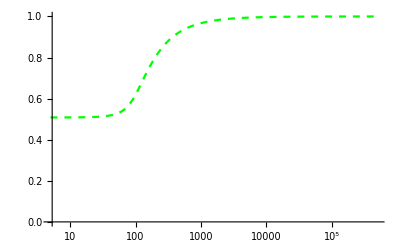

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.503235},{6,0.503251},{6,0.503251},{7,0.503261},{7,0.503261},{8,0.503266},{9,0.503268},{10,0.503267},{11,0.503263},{12,0.503256},{14,0.503237},{15,0.503225},{17,0.503196},{18,0.503179},{20,0.503143},{22,0.503102},{25,0.503032},{27,0.50298},{30,0.502893},{33,0.502795},{37,0.502644},{41,0.502468},{45,0.502264},{50,0.501966},{55,0.501616},{61,0.501129},{67,0.500579},{74,0.499888},{82,0.499101},{91,0.498334},{100,0.497793},{111,0.49747},{123,0.497446},{136,0.497628},{150,0.497906},{166,0.498225},{183,0.498519},{202,0.498785},{224,0.499024},{247,0.499213},{273,0.499371},{302,0.4995},{333,0.4996},{368,0.499682},{407,0.499748},{450,0.4998},{497,0.499841},{550,0.499873},{608,0.499899},{671,0.499919},{742,0.499935},{820,0.499948},{906,0.499958},{1002,0.499967},{1107,0.499973},{1223,0.499978},{1352,0.499983},{1494,0.499986},{1651,0.499989},{1825,0.499991},{2017,0.499993},{2229,0.499994},{2464,0.499995},{2723,0.499996},{3009,0.499997},{3326,0.499997},{3675,0.499998},{4062,0.499998},{4489,0.499999},{4961,0.499999},{5483,0.499999},{6060,0.499999},{6697,0.499999},{7401,0.499999},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

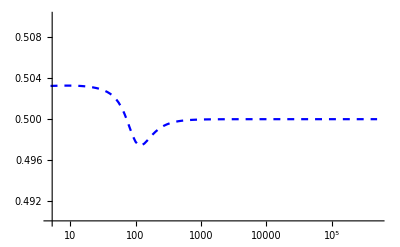

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.475;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.0413371,0.0333071,0.00839257,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{},{}}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.10571,0.991999}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.991999,1.10571},{0.991719,1.09494},{0.991372,1.08423},{0.990937,1.07361},{0.990373,1.06311},{0.989622,1.05281},{0.988584,1.04279},{0.98709,1.03322},{0.98486,1.0244},{0.981475,1.01672},{0.976495,1.01065},{0.969775,1.00631},{0.961611,1.00342},{0.952464,1.00151},{0.942703,1.00021},{0.932561,0.999296},{0.922175,0.998624},{0.911627,0.998115},{0.900969,0.997716},{0.890231,0.997397},{0.879434,0.997136},{0.868594,0.996919},{0.85772,0.996736},{0.846819,0.99658},{0.835898,0.996444},{0.824958,0.996326},{0.814005,0.996223},{0.80304,0.996131},{0.792065,0.996048},{0.781082,0.995975},{0.770091,0.995908},{0.759094,0.995848},{0.748092,0.995793},{0.737086,0.995742},{0.726075,0.995696},{0.71506,0.995653},{0.704042,0.995614},{0.693022,0.995577},{0.681999,0.995543},{0.670973,0.995512},{0.659946,0.995482},{0.648916,0.995455},{0.637885,0.995429},{0.626852,0.995404},{0.615818,0.995381},{0.604783,0.995359},{0.593746,0.995339},{0.582708,0.995319},{0.57167,0.995301},{0.56063,0.995284},{0.549589,0.995267}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

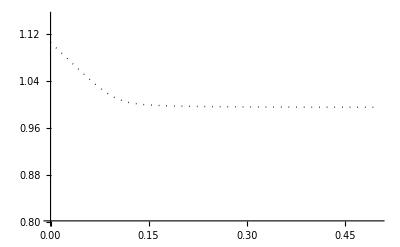

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

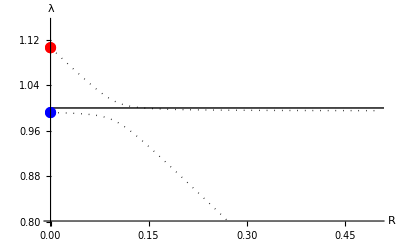

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504649},{6,0.504656},{6,0.504656},{7,0.504663},{7,0.504663},{8,0.50467},{9,0.504677},{10,0.504685},{11,0.504693},{12,0.504702},{14,0.504722},{15,0.504734},{17,0.504762},{18,0.504779},{20,0.504816},{22,0.504861},{25,0.504943},{27,0.505008},{30,0.505123},{33,0.50526},{37,0.505479},{41,0.505744},{45,0.506059},{50,0.506529},{55,0.507094},{61,0.50791},{67,0.508895},{74,0.510288},{82,0.512245},{91,0.51498},{100,0.518359},{111,0.523468},{123,0.53038},{136,0.53949},{150,0.551089},{166,0.566241},{183,0.583892},{202,0.604593},{224,0.628751},{247,0.653285},{273,0.679387},{302,0.70599},{333,0.731364},{368,0.756398},{407,0.78028},{450,0.802473},{497,0.822693},{550,0.8415},{608,0.858333},{671,0.873243},{742,0.886886},{820,0.899},{906,0.909784},{1002,0.919482},{1107,0.928023},{1223,0.935625},{1352,0.942434},{1494,0.948468},{1651,0.953846},{1825,0.95865},{2017,0.962925},{2229,0.966736},{2464,0.970148},{2723,0.973187},{3009,0.975903},{3326,0.97834},{3675,0.980514},{4062,0.982468},{4489,0.984217},{4961,0.985787},{5483,0.987197},{6060,0.988463},{6697,0.9896},{7401,0.990622},{8180,0.991542},{9040,0.99237},{9991,0.993115},{11042,0.993786},{12203,0.99439},{13486,0.994935},{14905,0.995426},{16472,0.995869},{18205,0.996269},{20119,0.996629},{22235,0.996954},{24574,0.997247},{27158,0.997512},{30015,0.997752},{33171,0.997968},{36660,0.998163},{40515,0.998339},{44776,0.998498},{49486,0.998642},{54690,0.998772},{60442,0.99889},{66799,0.998996},{73824,0.999092},{81588,0.999179},{90169,0.999257},{99652,0.999328},{110132,0.999392},{121715,0.99945},{134516,0.999503},{148663,0.99955},{164298,0.999593},{181578,0.999632},{200674,0.999667},{221779,0.999699},{245104,0.999728},{270882,0.999753},{299371,0.999777},{330856,0.999798},{365652,0.999817},{404108,0.999835},{446609,0.999851},{493579,0.999865}}

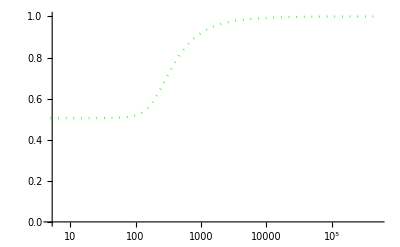

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.499678},{6,0.499721},{6,0.499721},{7,0.499758},{7,0.499758},{8,0.499791},{9,0.499819},{10,0.499845},{11,0.499867},{12,0.499887},{14,0.499919},{15,0.499933},{17,0.499955},{18,0.499965},{20,0.499981},{22,0.499994},{25,0.500009},{27,0.500017},{30,0.500027},{33,0.500036},{37,0.500046},{41,0.500057},{45,0.500067},{50,0.50008},{55,0.500095},{61,0.500115},{67,0.500139},{74,0.50017},{82,0.500213},{91,0.500272},{100,0.500343},{111,0.500449},{123,0.500593},{136,0.500784},{150,0.501035},{166,0.501374},{183,0.501783},{202,0.502268},{224,0.502826},{247,0.503366},{273,0.5039},{302,0.504396},{333,0.504821},{368,0.505193},{407,0.505507},{450,0.505763},{497,0.505967},{550,0.506133},{608,0.506262},{671,0.506363},{742,0.506443},{820,0.506506},{906,0.506555},{1002,0.506594},{1107,0.506624},{1223,0.506648},{1352,0.506666},{1494,0.506681},{1651,0.506693},{1825,0.506702},{2017,0.506709},{2229,0.506715},{2464,0.50672},{2723,0.506724},{3009,0.506727},{3326,0.506729},{3675,0.506731},{4062,0.506732},{4489,0.506734},{4961,0.506735},{5483,0.506735},{6060,0.506736},{6697,0.506737},{7401,0.506737},{8180,0.506737},{9040,0.506738},{9991,0.506738},{11042,0.506738},{12203,0.506738},{13486,0.506738},{14905,0.506738},{16472,0.506739},{18205,0.506739},{20119,0.506739},{22235,0.506739},{24574,0.506739},{27158,0.506739},{30015,0.506739},{33171,0.506739},{36660,0.506739},{40515,0.506739},{44776,0.506739},{49486,0.506739},{54690,0.506739},{60442,0.506739},{66799,0.506739},{73824,0.506739},{81588,0.506739},{90169,0.506739},{99652,0.506739},{110132,0.506739},{121715,0.506739},{134516,0.506739},{148663,0.506739},{164298,0.506739},{181578,0.506739},{200674,0.506739},{221779,0.506739},{245104,0.506739},{270882,0.506739},{299371,0.506739},{330856,0.506739},{365652,0.506739},{404108,0.506739},{446609,0.506739},{493579,0.506739}}

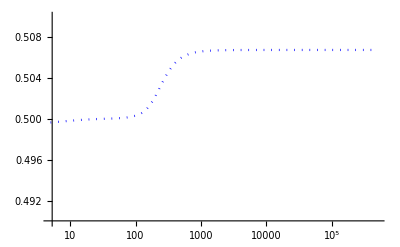

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dotted,Blue}]
```

```mathematica
Show[plot6]
```

-Graphics-

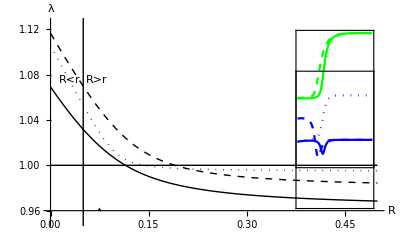

```mathematica
plotC=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.05,0},{0.05,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.03,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.07,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

#### Increasing recombination R (r=0.2) [No haploid selection] EXAMPLE STARTING NEAR EQUIL A [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.275;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.144089,0.109799,0.0878885,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.615385,0.571429,0,0.5}

{1.02158,0.899281}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.1336,0.97555}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.97555,1.1336},{0.974359,1.12352},{0.972997,1.1136},{0.971431,1.10388},{0.96962,1.09441},{0.967517,1.08524},{0.965066,1.07641},{0.962205,1.06799},{0.958865,1.06005},{0.95498,1.05265},{0.950487,1.04586},{0.945345,1.03973},{0.939531,1.03426},{0.933053,1.02946},{0.925945,1.02529},{0.91826,1.02169},{0.910063,1.01861},{0.901424,1.01597},{0.892407,1.0137},{0.883072,1.01176},{0.873471,1.01008},{0.863647,1.00862},{0.853637,1.00735},{0.84347,1.00624},{0.833172,1.00526},{0.822762,1.00439},{0.812257,1.00361},{0.801672,1.00292},{0.791017,1.00229},{0.780301,1.00173},{0.769534,1.00121},{0.75872,1.00075},{0.747867,1.00032},{0.736978,0.999927},{0.726059,0.999566},{0.715111,0.999234},{0.704139,0.998925},{0.693145,0.998639},{0.682131,0.998373},{0.671098,0.998125},{0.66005,0.997893},{0.648987,0.997676},{0.637911,0.997472},{0.626822,0.99728},{0.615722,0.9971},{0.604612,0.996929},{0.593493,0.996768},{0.582365,0.996616},{0.571229,0.996472},{0.560086,0.996335},{0.548936,0.996205}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

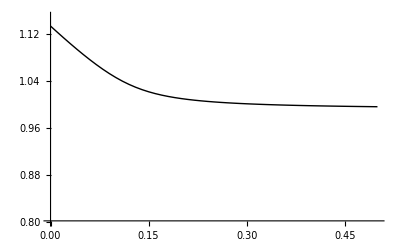

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

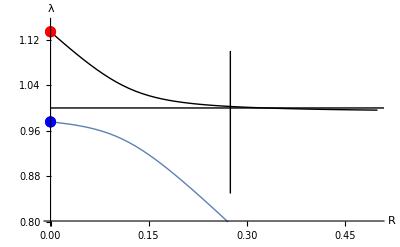

```mathematica
Show[
plot4,
Graphics[Line[{{tryr,0.85},{tryr,1.1}}]],
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.3;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504621},{6,0.504657},{6,0.504657},{7,0.504675},{7,0.504675},{8,0.504682},{9,0.504683},{10,0.50468},{11,0.504675},{12,0.504668},{14,0.504651},{15,0.504643},{17,0.504625},{18,0.504616},{20,0.504598},{22,0.50458},{25,0.504554},{27,0.504536},{30,0.50451},{33,0.504484},{37,0.504449},{41,0.504415},{45,0.50438},{50,0.504338},{55,0.504296},{61,0.504247},{67,0.504197},{74,0.504141},{82,0.504077},{91,0.504006},{100,0.503936},{111,0.503853},{123,0.503764},{136,0.503669},{150,0.50357},{166,0.50346},{183,0.503346},{202,0.503223},{224,0.503086},{247,0.502949},{273,0.5028},{302,0.502643},{333,0.502485},{368,0.502316},{407,0.502141},{450,0.501963},{497,0.501785},{550,0.501603},{608,0.501424},{671,0.501251},{742,0.501081},{820,0.50092},{906,0.50077},{1002,0.500631},{1107,0.500507},{1223,0.500398},{1352,0.500304},{1494,0.500226},{1651,0.500162},{1825,0.500113},{2017,0.500075},{2229,0.500048},{2464,0.500029},{2723,0.500017},{3009,0.500009},{3326,0.500005},{3675,0.500002},{4062,0.500001},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

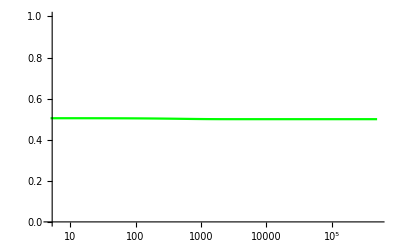

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

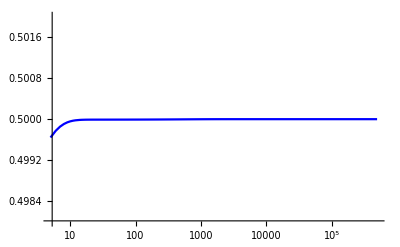

```mathematica
SRinset4=ListLogLinearPlot[Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}],Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.275;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0,0,0,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.08056,0.9388}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.17647,1.}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{1.,1.17647},{1.,1.16471},{1.,1.15294},{1.,1.14118},{1.,1.12941},{1.,1.11765},{1.,1.10588},{1.,1.09412},{1.,1.08235},{1.,1.07059},{1.,1.05882},{1.,1.04706},{1.,1.03529},{1.,1.02353},{1.,1.01176},{1.,1.},{0.988235,1.},{0.976471,1.},{0.964706,1.},{0.952941,1.},{0.941176,1.},{0.929412,1.},{0.917647,1.},{0.905882,1.},{0.894118,1.},{0.882353,1.},{0.870588,1.},{0.858824,1.},{0.847059,1.},{0.835294,1.},{0.823529,1.},{0.811765,1.},{0.8,1.},{0.788235,1.},{0.776471,1.},{0.764706,1.},{0.752941,1.},{0.741176,1.},{0.729412,1.},{0.717647,1.},{0.705882,1.},{0.694118,1.},{0.682353,1.},{0.670588,1.},{0.658824,1.},{0.647059,1.},{0.635294,1.},{0.623529,1.},{0.611765,1.},{0.6,1.},{0.588235,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

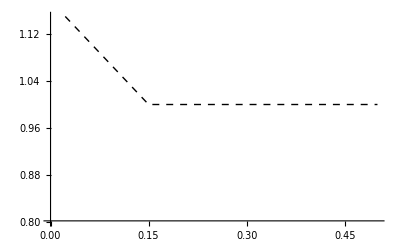

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

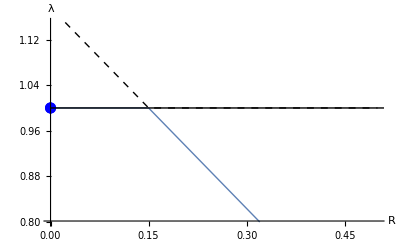

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.3;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504762},{6,0.504812},{6,0.504812},{7,0.504844},{7,0.504844},{8,0.504863},{9,0.504876},{10,0.504883},{11,0.504888},{12,0.504891},{14,0.504895},{15,0.504896},{17,0.504897},{18,0.504898},{20,0.504899},{22,0.504899},{25,0.5049},{27,0.504901},{30,0.504902},{33,0.504903},{37,0.504905},{41,0.504906},{45,0.504908},{50,0.50491},{55,0.504912},{61,0.504914},{67,0.504916},{74,0.504919},{82,0.504922},{91,0.504925},{100,0.504929},{111,0.504933},{123,0.504937},{136,0.504942},{150,0.504947},{166,0.504953},{183,0.504959},{202,0.504966},{224,0.504974},{247,0.504983},{273,0.504992},{302,0.505003},{333,0.505014},{368,0.505027},{407,0.50504},{450,0.505056},{497,0.505073},{550,0.505091},{608,0.505112},{671,0.505134},{742,0.505158},{820,0.505185},{906,0.505215},{1002,0.505247},{1107,0.505283},{1223,0.505321},{1352,0.505364},{1494,0.505411},{1651,0.505462},{1825,0.505518},{2017,0.505579},{2229,0.505647},{2464,0.505721},{2723,0.505801},{3009,0.50589},{3326,0.505987},{3675,0.506094},{4062,0.506211},{4489,0.50634},{4961,0.506482},{5483,0.506638},{6060,0.506809},{6697,0.506998},{7401,0.507206},{8180,0.507435},{9040,0.507687},{9991,0.507963},{11042,0.508265},{12203,0.508595},{13486,0.508954},{14905,0.509342},{16472,0.509757},{18205,0.510198},{20119,0.510661},{22235,0.51114},{24574,0.511627},{27158,0.512113},{30015,0.512587},{33171,0.513037},{36660,0.513451},{40515,0.513821},{44776,0.514139},{49486,0.514402},{54690,0.514611},{60442,0.51477},{66799,0.514884},{73824,0.514963},{81588,0.515015},{90169,0.515046},{99652,0.515064},{110132,0.515074},{121715,0.515079},{134516,0.515081},{148663,0.515082},{164298,0.515082},{181578,0.515082},{200674,0.515082},{221779,0.515082},{245104,0.515082},{270882,0.515082},{299371,0.515082},{330856,0.515082},{365652,0.515082},{404108,0.515082},{446609,0.515082},{493579,0.515082}}

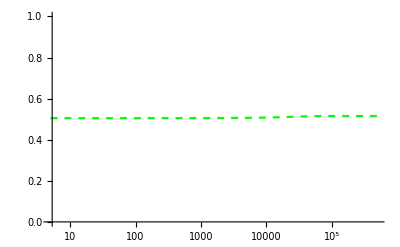

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.499683},{6,0.499818},{6,0.499818},{7,0.499902},{7,0.499902},{8,0.499954},{9,0.499987},{10,0.500007},{11,0.50002},{12,0.500028},{14,0.500036},{15,0.500038},{17,0.50004},{18,0.50004},{20,0.50004},{22,0.500041},{25,0.500041},{27,0.500041},{30,0.500041},{33,0.500041},{37,0.500041},{41,0.500041},{45,0.50004},{50,0.50004},{55,0.50004},{61,0.50004},{67,0.50004},{74,0.50004},{82,0.50004},{91,0.50004},{100,0.50004},{111,0.50004},{123,0.50004},{136,0.50004},{150,0.500039},{166,0.500039},{183,0.500039},{202,0.500039},{224,0.500039},{247,0.500038},{273,0.500038},{302,0.500038},{333,0.500038},{368,0.500037},{407,0.500037},{450,0.500037},{497,0.500036},{550,0.500036},{608,0.500036},{671,0.500035},{742,0.500035},{820,0.500034},{906,0.500034},{1002,0.500033},{1107,0.500033},{1223,0.500032},{1352,0.500031},{1494,0.500031},{1651,0.50003},{1825,0.50003},{2017,0.500029},{2229,0.500028},{2464,0.500028},{2723,0.500027},{3009,0.500026},{3326,0.500025},{3675,0.500025},{4062,0.500024},{4489,0.500023},{4961,0.500023},{5483,0.500022},{6060,0.500021},{6697,0.50002},{7401,0.50002},{8180,0.500019},{9040,0.500018},{9991,0.500017},{11042,0.500016},{12203,0.500015},{13486,0.500014},{14905,0.500013},{16472,0.500012},{18205,0.500011},{20119,0.50001},{22235,0.500009},{24574,0.500007},{27158,0.500006},{30015,0.500005},{33171,0.500004},{36660,0.500003},{40515,0.500003},{44776,0.500002},{49486,0.500001},{54690,0.500001},{60442,0.500001},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

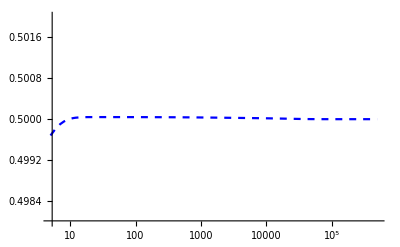

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.475;
tryαm=0.5;
tryr=0.275;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 4 of {}⟦1⟧ does not exist.

{{},{}}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 4 of {}⟦1⟧ does not exist.

{λ}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 4 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ},{λ}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

Part::partw: Part 2 of {{λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,«1»}} does not exist.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«1»},{{λ,λ,λ,λ,λ,λ,λ,«37»,λ,λ,λ,λ,λ,λ,«1»}}⟦2⟧} cannot be transposed.

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

ListPlot::lpn: Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«1»},{{λ,λ,λ,λ,λ,«42»,λ,λ,λ,«1»}}⟦2⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5},{{λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ}}⟦2⟧}],Joined→True,PlotStyle→{Dashing[{0,Small}],Thickness[Large],GrayLevel[0]},PlotRange→{Automatic,{0.8,1.15}}]]

ListPlot::lpn: Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«1»},{{λ,λ,λ,λ,λ,«42»,λ,λ,λ,«1»}}⟦2⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gtype: ListPlot is not a type of graphics.

Part::partw: Part 2 of {λ} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

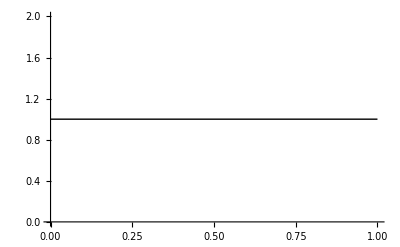
Show[Show[ListPlot[Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5},{{λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ,λ}}⟦2⟧}],Joined→True,PlotStyle→{Dashing[{0,Small}],Thickness[Large],GrayLevel[0]},PlotRange→{Automatic,{0.8,1.15}}]],-Graphics-,-Graphics-,-Graphics-,-Graphics-,AxesLabel→{R,λ}]

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.3;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

Part::partw: Part 1 of {} does not exist.

{{5,0.504687},{6,0.504738},{6,0.504738},{7,0.504771},{7,0.504771},{8,0.504793},{9,0.504808},{10,0.504817},{11,0.504824},{12,0.504828},{14,0.504833},{15,0.504835},{17,0.504837},{18,0.504838},{20,0.504839},{22,0.50484},{25,0.504841},{27,0.504842},{30,0.504843},{33,0.504845},{37,0.504847},{41,0.504848},{45,0.50485},{50,0.504852},{55,0.504855},{61,0.504857},{67,0.50486},{74,0.504863},{82,0.504867},{91,0.504871},{100,0.504875},{111,0.50488},{123,0.504885},{136,0.504891},{150,0.504897},{166,0.504904},{183,0.504912},{202,0.50492},{224,0.50493},{247,0.50494},{273,0.504951},{302,0.504964},{333,0.504978},{368,0.504994},{407,0.505011},{450,0.50503},{497,0.505051},{550,0.505075},{608,0.505101},{671,0.50513},{742,0.505162},{820,0.505198},{906,0.505237},{1002,0.505282},{1107,0.505331},{1223,0.505386},{1352,0.505449},{1494,0.505518},{1651,0.505596},{1825,0.505683},{2017,0.505782},{2229,0.505893},{2464,0.506019},{2723,0.506162},{3009,0.506324},{3326,0.50651},{3675,0.506721},{4062,0.506966},{4489,0.507248},{4961,0.507575},{5483,0.507957},{6060,0.508407},{6697,0.508939},{7401,0.509575},{8180,0.510342},{9040,0.511275},{9991,0.512428},{11042,0.513869},{12203,0.515699},{13486,0.518063},{14905,0.521173},{16472,0.525328},{18205,0.53096},{20119,0.5386},{22235,0.548788},{24574,0.561726},{27158,0.576854},{30015,0.592855},{33171,0.608214},{36660,0.62192},{40515,0.63356},{44776,0.643149},{49486,0.650888},{54690,0.657032},{60442,0.661836},{66799,0.665524},{73824,0.668298},{81588,0.670331},{90169,0.671775},{99652,0.672766},{110132,0.673416},{121715,0.673823},{134516,0.674063},{148663,0.674197},{164298,0.674266},{181578,0.674299},{200674,0.674314},{221779,0.67432},{245104,0.674322},{270882,0.674322},{299371,0.674323},{330856,0.674323},{365652,0.674323},{404108,0.674323},{446609,0.674323},{493579,0.674323}}

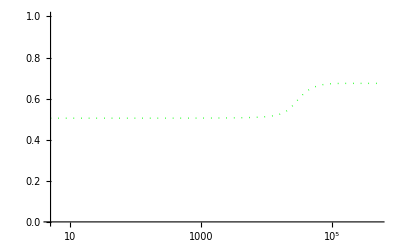

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.49959},{6,0.499723},{6,0.499723},{7,0.49981},{7,0.49981},{8,0.499867},{9,0.499905},{10,0.499929},{11,0.499945},{12,0.499955},{14,0.499967},{15,0.49997},{17,0.499973},{18,0.499974},{20,0.499974},{22,0.499975},{25,0.499975},{27,0.499975},{30,0.499975},{33,0.499975},{37,0.499975},{41,0.499975},{45,0.499975},{50,0.499975},{55,0.499975},{61,0.499975},{67,0.499975},{74,0.499975},{82,0.499975},{91,0.499975},{100,0.499975},{111,0.499975},{123,0.499975},{136,0.499975},{150,0.499975},{166,0.499976},{183,0.499976},{202,0.499976},{224,0.499976},{247,0.499976},{273,0.499976},{302,0.499976},{333,0.499976},{368,0.499976},{407,0.499976},{450,0.499976},{497,0.499975},{550,0.499975},{608,0.499975},{671,0.499975},{742,0.499975},{820,0.499975},{906,0.499975},{1002,0.499975},{1107,0.499975},{1223,0.499974},{1352,0.499974},{1494,0.499974},{1651,0.499973},{1825,0.499973},{2017,0.499973},{2229,0.499972},{2464,0.499972},{2723,0.499971},{3009,0.49997},{3326,0.49997},{3675,0.499969},{4062,0.499968},{4489,0.499967},{4961,0.499965},{5483,0.499964},{6060,0.499962},{6697,0.49996},{7401,0.499958},{8180,0.499955},{9040,0.499952},{9991,0.499949},{11042,0.499944},{12203,0.499939},{13486,0.499934},{14905,0.499927},{16472,0.49992},{18205,0.499913},{20119,0.499907},{22235,0.499905},{24574,0.499909},{27158,0.499919},{30015,0.499933},{33171,0.499948},{36660,0.499961},{40515,0.499971},{44776,0.499979},{49486,0.499985},{54690,0.499989},{60442,0.499992},{66799,0.499995},{73824,0.499996},{81588,0.499998},{90169,0.499999},{99652,0.499999},{110132,0.499999},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

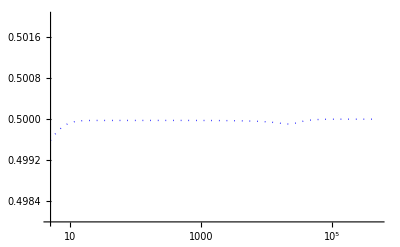

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dotted,Blue}]
```

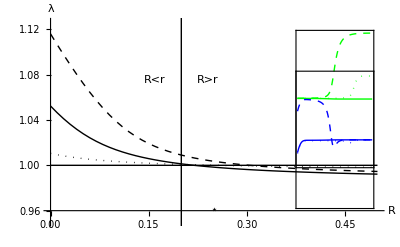

```mathematica
plotD=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.2,0},{0.2,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.25,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.16,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.24,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

## Mike: r=0 with various R, invasion dynamics

#### Plotting parameters [ENTER]

```mathematica
Pad={{40,20},{50,30}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
```

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{60,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

#### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.50008/.SUBS

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

#### Simulation code [Enter]

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males maintain the Y or become all  its frequency among female gametes (when fixed)Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

#### Parameters

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};

tryFAA2=0.85;
tryFAa2=1;
tryFaa2=1.05;
tryMAA2=0.75;
tryMAa2=1;
tryMaa2=0.75;
trywAf2=1;
trywaf2=1;
trywAm2=1;
trywam2=1;
tryαf2=0.5;
tryαm2=0.5;
tryr2=0.005;
tryR2=0;
subpar2={FAA->tryFAA2,FAa->tryFAa2,Faa->tryFaa2,MAA->tryMAA2,MAa->tryMAa2,Maa->tryMaa2,wAf->trywAf2,waf->trywaf2,wAm->trywAm2,wam->trywam2,αf->tryαf2,αm->tryαm2};

tryFAA3=0.6;
tryFAa3=1;
tryFaa3=0.6;
tryMAA3=0.7;
tryMAa3=1;
tryMaa3=0.5;
trywAf3=1;
trywaf3=1;
trywAm3=1;
trywam3=1;
tryαf3=0.5;
tryαm3=0.5;
tryr3=0.005;
tryR3=0;
subpar3={FAA->tryFAA3,FAa->tryFAa3,Faa->tryFaa3,MAA->tryMAA3,MAa->tryMAa3,Maa->tryMaa3,wAf->trywAf3,waf->trywaf3,wAm->trywAm3,wam->trywam3,αf->tryαf3,αm->tryαm3};
```

#### extra parameters

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},{500,500,{0,0.01}},{1000,1000,{0,0.01}},{5000,5000,{0,0.01}}},Table[{y,y,ticksize},{y,0,0.5,0.25}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
```

#### a favoured in females r=0

```mathematica
tryr2=0;
```

```mathematica
tryR=0.001;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Blackr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Blackr0=ListLogLinearPlot[MODtab2Blackr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Redr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Redr0=ListLogLinearPlot[MODtab2Redr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Bluer0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Bluer0=ListLogLinearPlot[MODtab2Bluer0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Greenr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Greenr0=ListLogLinearPlot[MODtab2Greenr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green},loglinearplotINVoptions];
```

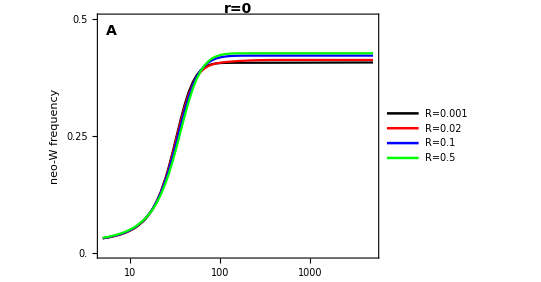

```mathematica
partA=Legended[Show[MOD2Blackr0,MOD2Redr0,MOD2Bluer0,MOD2Greenr0,
FrameLabel->{{Style["neo-W frequency",FontSize->14],""},{Style["",FontSize->14],""}},
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Text[Style["r=0",14,Bold],Scaled@{0.5,1.02}]
}],
Placed[
LineLegend[
{Directive[Thickness[0.005],Black],
Directive[Thickness[0.005],Red],
Directive[Thickness[0.005],Blue],
Directive[Thickness[0.005],Green]
},
{Style["R=0.001",14],
Style["R=0.02",14],
Style["R=0.1",14],
Style["R=0.5",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.825,0.4}
]
]
```

#### a favoured in females

```mathematica
tryr2=0.005;
```

```mathematica
tryR=0.001;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Black=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Red=ListLogLinearPlot[MODtab2Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Blue=ListLogLinearPlot[MODtab2Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Green=ListLogLinearPlot[MODtab2Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green},loglinearplotINVoptions];
```

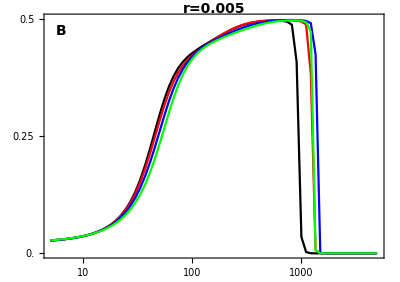

```mathematica
partB=Show[MOD2Black,MOD2Red,MOD2Blue,MOD2Green,
(*FrameLabel->{{Style["neo-W frequency",FontSize->14],""},{Style["Generation",FontSize->14],""}},*)
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Text[Style["r=0.005",14,Bold],Scaled@{0.5,1.02}]
}]
```

#### overdominance in females r=0

```mathematica
tryr3=0;
```

```mathematica
tryR=0.001;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Blackr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Blackr0=ListLogLinearPlot[MODtab3Blackr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Redr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Redr0=ListLogLinearPlot[MODtab3Redr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Bluer0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Bluer0=ListLogLinearPlot[MODtab3Bluer0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Greenr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Greenr0=ListLogLinearPlot[MODtab3Greenr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green},loglinearplotINVoptions];
```

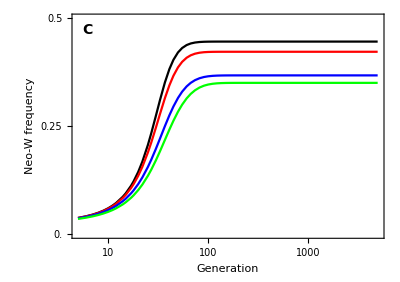

```mathematica
partC=Show[MOD3Blackr0,MOD3Redr0,MOD3Bluer0,MOD3Greenr0,
FrameLabel->{{Style["Neo-W frequency",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos](*,
Text[Style["r=0",14,Bold],Scaled@{0.5,1.02}]*)
}]
```

#### overdominance in females

```mathematica
tryr3=0.005;
```

```mathematica
tryR=0.001;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Black=ListLogLinearPlot[MODtab3Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Red=ListLogLinearPlot[MODtab3Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Blue=ListLogLinearPlot[MODtab3Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Green=ListLogLinearPlot[MODtab3Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green},loglinearplotINVoptions];
```

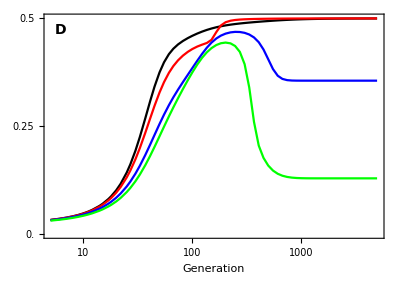

```mathematica
partD=Show[MOD3Black,MOD3Red,MOD3Blue,MOD3Green,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{
Text[Style["D",14,Bold],Scaled@letpos](*,
Text[Style["r=0.005",14,Bold],Scaled@{0.5,1.02}]*)
}]
```

#### Combine

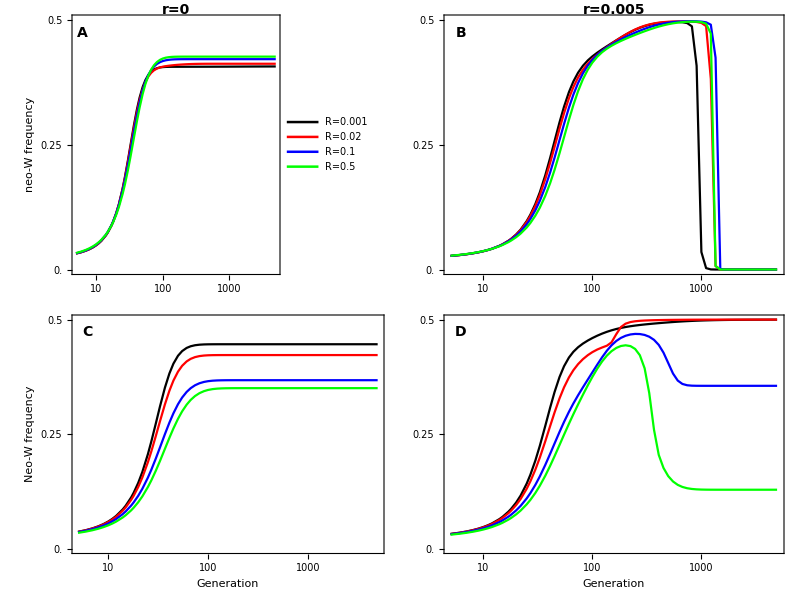

Plots/Temporal_Overdominance_Mike.pdf

```mathematica
GraphicsGrid[{{partA,partB},{partC,partD}},Spacings->-30]

Export[plotdir<>"Temporal_Overdominance_Mike.pdf",%]
```

## Mike: sex ratio plot with Ploidally Antagonistic Selection

#### Plotting parameters [ENTER]

```mathematica
Pad={{40,20},{50,30}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
```

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{60,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

#### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

XamXamfemale+XamXaMfemale+XaMXaMfemale+XAmXamfemale+XAmXaMfemale+XAmXAmfemale+XAmXAMfemale+XAMXamfemale+XAMXaMfemale+XAMXAMfemale+XamYamfemale+XamYaMfemale+XamYAmfemale+XamYAMfemale+XaMYamfemale+XaMYaMfemale+XaMYAmfemale+XaMYAMfemale+XAmYamfemale+XAmYaMfemale+XAmYAmfemale+XAmYAMfemale+XAMYamfemale+XAMYaMfemale+XAMYAmfemale+XAMYAMfemale+YamYamfemale+YamYaMfemale+YamYAMfemale+YaMYaMfemale+YAmYamfemale+YAmYaMfemale+YAmYAmfemale+YAmYAMfemale+YAMYaMfemale+YAMYAMfemale/.SUBS

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

ReplaceAll::reps: {SUBS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

#### Simulation code [Enter]

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males maintain the Y or become all  its frequency among female gametes (when fixed)Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

#### Parameters

```mathematica
tryFAA=1.2;
tryFAa=1.14;
tryFaa=1;
tryMAA=1.2;
tryMAa=1.14;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.4;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### extra parameters

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{100,100,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0,0.5,0.25}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
loglinearplotINVSRoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},{500,500,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0.4,0.6,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
startplot=5;
endtime=1000;
tryR=0;
trypm=0.01;
tryk=1;
```

#### Ploidally Antagonistic Selection (r=0.02) neo-Y

Here we are going to adjust the fitness parameters only to change definition of sex.
Also have to adjust sex ratio to 1-sexratio becuase it gives the frequency of the ancestrally heterozygous sex.

```mathematica
tryFAA=1.2;
tryFAa=1.14;
tryFaa=1;
tryMAA=1.2;
tryMAa=1.14;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.4;
tryαm=0.5;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Black},loglinearplotINVoptions];
SRtabBlack=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlack=ListLogLinearPlot[SRtabBlack,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Black},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Red},loglinearplotINVoptions];
SRtabRed=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRRed=ListLogLinearPlot[SRtabRed,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Red},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Blue},loglinearplotINVoptions];
SRtabBlue=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlue=ListLogLinearPlot[SRtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Blue},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Green},loglinearplotINVoptions];
SRtabGreen=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRGreen=ListLogLinearPlot[SRtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Green},loglinearplotINVSRoptions];
```

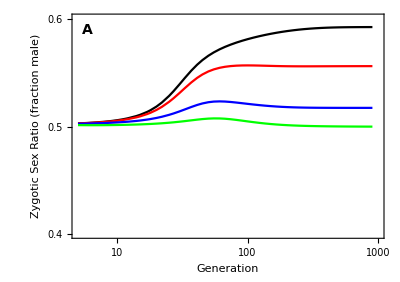

```mathematica
plotA=Show[SRBlack,SRRed,SRBlue,SRGreen,
FrameLabel->{{Style["Zygotic Sex Ratio (fraction male)",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{Inset[Show[MODBlack,MODRed,MODBlue,MODGreen,(*ImageSize->150,*)BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->8},
FrameLabel->{{Style["neo-Y frequency",FontSize->8],""},{Style["",FontSize->14],""}}],
Scaled@{1,-0.14},{Right,Bottom},{3,3*Sqrt[2]}],
Text[Style["A",14,Bold],Scaled@letpos]}
]
```

#### Ploidally Antagonistic Selection (r=0.02) neo-W

```mathematica
tryFAA=1.2;
tryFAa=1.14;
tryFaa=1;
tryMAA=1.2;
tryMAa=1.14;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.4;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Black},loglinearplotINVoptions];
SRtabBlack=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlack=ListLogLinearPlot[SRtabBlack,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Black},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Red},loglinearplotINVoptions];
SRtabRed=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRRed=ListLogLinearPlot[SRtabRed,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Red},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Blue},loglinearplotINVoptions];
SRtabBlue=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlue=ListLogLinearPlot[SRtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Blue},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Green},loglinearplotINVoptions];
SRtabGreen=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRGreen=ListLogLinearPlot[SRtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Green},loglinearplotINVSRoptions];
```

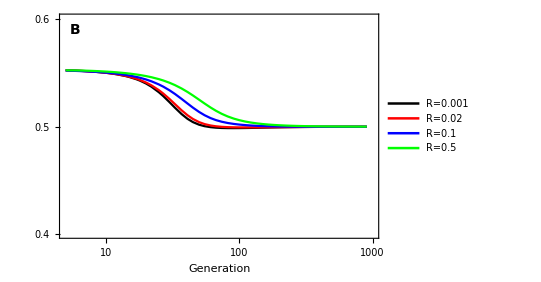

```mathematica
plotB=Legended[Show[SRBlack,SRRed,SRBlue,SRGreen,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{Inset[Show[MODBlack,MODRed,MODBlue,MODGreen,(*ImageSize->150,*)BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->8},
FrameLabel->{{Style["neo-W frequency",FontSize->8],""},{Style["",FontSize->14],""}}],Scaled@{1,-0.14},{Right,Bottom},{3,3*Sqrt[2]}],
Text[Style["B",14,Bold],Scaled@letpos]}],
Placed[
LineLegend[
{Directive[Thickness[0.005],Black],
Directive[Thickness[0.005],Red],
Directive[Thickness[0.005],Blue],
Directive[Thickness[0.005],Green]
},
{Style["R=0.001",14],
Style["R=0.02",14],
Style["R=0.1",14],
Style["R=0.5",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.825,0.79}
]
]
```

#### Combine

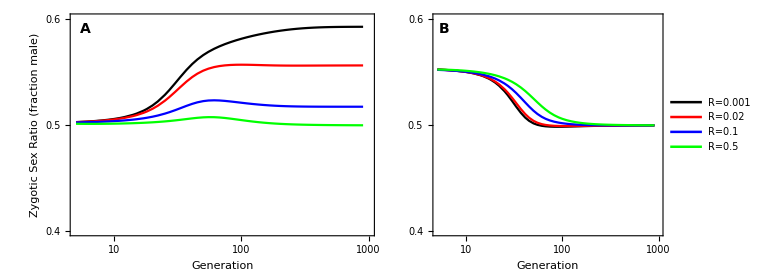

Plots/Temporal_SR_Mike.pdf

```mathematica
GraphicsRow[{plotA,plotB}]

Export[plotdir<>"Temporal_SR_Mike.pdf",%]
```

## Mike: r=0 with various R, invasion dynamics (OLD)

#### Plotting parameters [ENTER]

```mathematica
Pad={{40,20},{50,30}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
```

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{60,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

#### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

#### Simulation code [Enter]

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males maintain the Y or become all  its frequency among female gametes (when fixed)Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

#### A favoured in females

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
```

```mathematica
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.574635,0.527072,0.0165667,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar1/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.615385,0.571429,0,0.5}

{1.02158,0.899281}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar1/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}];
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

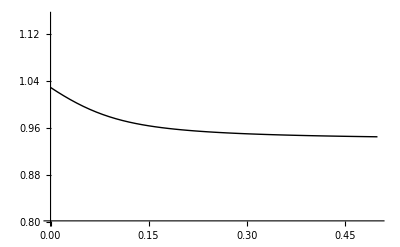

```mathematica
plot1=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W dynamics:

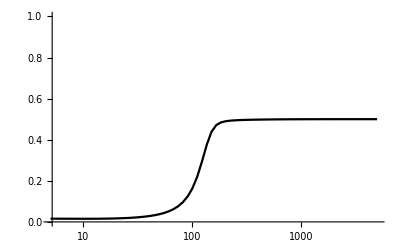

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Black}]
```

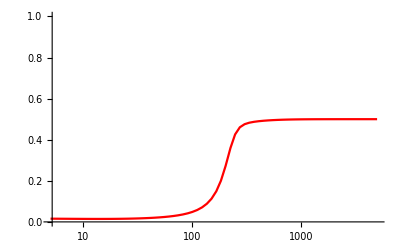

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red}]
```

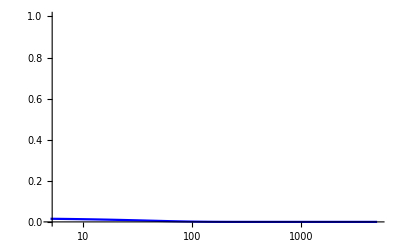

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue}]
```

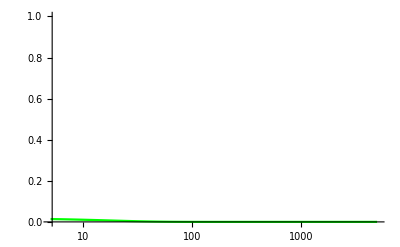

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab7=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset7=ListLogLinearPlot[MODtab7,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

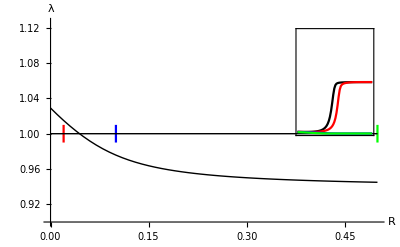

```mathematica
plotC=Show[
plot1,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,MODinset7,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
ListPlot[{{0.02,0.99},{0.02,1.01}},Joined->True,PlotStyle->{Red}],
ListPlot[{{0.1,0.99},{0.1,1.01}},Joined->True,PlotStyle->{Blue}],
ListPlot[{{0.5,0.99},{0.5,1.01}},Joined->True,PlotStyle->{Green}],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.9,1.08}},AxesOrigin->{0,0.9}
]
```

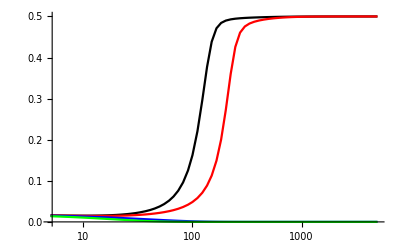

```mathematica
Show[
MODinset4,MODinset5,MODinset6,MODinset7,
PlotRange->{0,0.5}
]
```

#### a favoured in females

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.85;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.75;
tryMAa=1;
tryMaa=0.75;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.0143134,0.0157688,0.979711,0.5},{0.626862,0.682165,0.047932,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[2]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.777778,0.823529,0,0.5}

{1.03571,1.13636}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}];
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

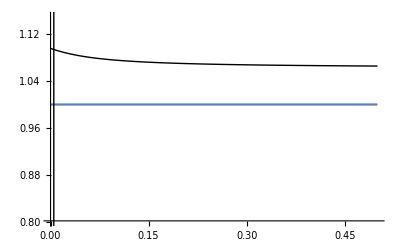

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
Plot[1,{x,0,0.5}],
Graphics[Line[{{tryr,0},{tryr,1.2}}]]
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W dynamics:

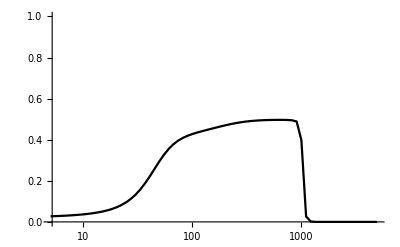

```mathematica
startplot=5;
endtime=5000;
tryr=0.005;
tryR=0;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Black}]
```

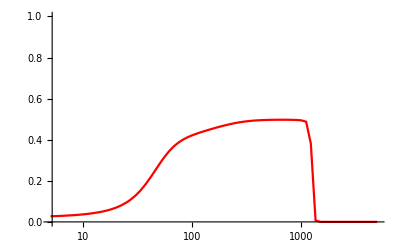

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red}]
```

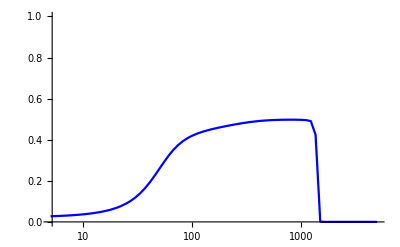

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue}]
```

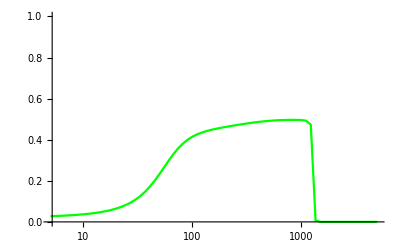

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab7=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset7=ListLogLinearPlot[MODtab7,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

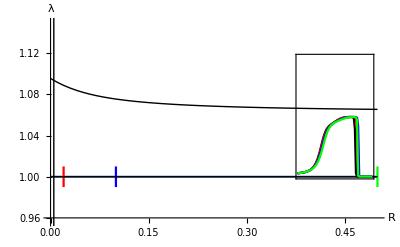

```mathematica
plotC=Show[
plot4,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,MODinset7,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
ListPlot[{{0.02,0.99},{0.02,1.01}},Joined->True,PlotStyle->{Red}],
ListPlot[{{0.1,0.99},{0.1,1.01}},Joined->True,PlotStyle->{Blue}],
ListPlot[{{0.5,0.99},{0.5,1.01}},Joined->True,PlotStyle->{Green}],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.15}},AxesOrigin->{0,0.96}
]
```

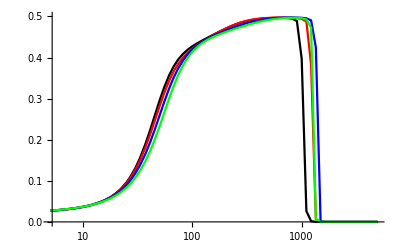

```mathematica
Show[MODinset4,MODinset5,MODinset6,MODinset7,PlotRange->{0,0.5}]
```

#### Overdominance in females, invasion but not fixation

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.7;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.378835,0.305667,0.984382,0.5},{0.720702,0.82555,0.0461837,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[2]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.75,0.857143,0,0.5}

{1.13725,1.05882}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.11196,1.04286}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{1.04286,1.11196},{1.03634,1.10502},{1.02851,1.09938},{1.01949,1.09493},{1.00948,1.09147},{0.9987,1.08878},{0.98733,1.08669},{0.975523,1.08503},{0.963389,1.08369},{0.951009,1.08261},{0.938441,1.08171},{0.925726,1.08095},{0.912898,1.08031},{0.899978,1.07977},{0.886984,1.07929},{0.87393,1.07888},{0.860827,1.07851},{0.847682,1.07819},{0.834503,1.0779},{0.821293,1.07764},{0.808059,1.07741},{0.794802,1.0772},{0.781527,1.07701},{0.768235,1.07683},{0.754928,1.07667},{0.741609,1.07652},{0.728278,1.07639},{0.714938,1.07626},{0.701588,1.07614},{0.68823,1.07603},{0.674865,1.07593},{0.661493,1.07583},{0.648115,1.07574},{0.634732,1.07566},{0.621344,1.07558},{0.607951,1.0755},{0.594554,1.07543},{0.581153,1.07537},{0.567749,1.0753},{0.554341,1.07524},{0.540931,1.07519},{0.527517,1.07513},{0.514101,1.07508},{0.500683,1.07503},{0.487262,1.07498},{0.47384,1.07494},{0.460415,1.0749},{0.446988,1.07486},{0.43356,1.07482},{0.42013,1.07478},{0.406699,1.07474}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

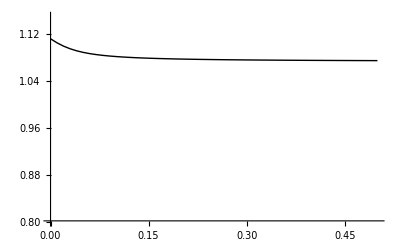

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

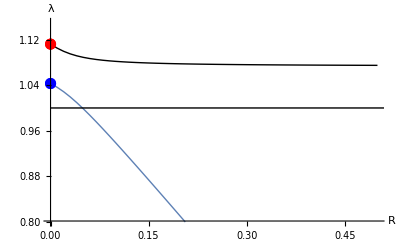

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W dynamics:

{{5,0.0326392},{6,0.0352033},{6,0.0352033},{7,0.0379848},{7,0.0379848},{8,0.0409995},{9,0.0442637},{10,0.0477944},{11,0.0516089},{12,0.0557247},{14,0.0649307},{15,0.0700549},{17,0.0814244},{18,0.0876969},{20,0.10147},{22,0.116912},{25,0.14315},{27,0.162518},{30,0.193793},{33,0.226649},{37,0.270292},{41,0.310453},{45,0.344573},{50,0.377488},{55,0.400758},{61,0.419417},{67,0.431653},{74,0.441316},{82,0.449088},{91,0.455637},{100,0.460848},{111,0.466015},{123,0.470533},{136,0.474409},{150,0.477673},{166,0.480542},{183,0.482863},{202,0.484837},{224,0.486568},{247,0.487952},{273,0.489174},{302,0.490256},{333,0.491197},{368,0.492083},{407,0.492916},{450,0.4937},{497,0.494434},{550,0.495138},{608,0.495788},{671,0.496374},{742,0.496914},{820,0.497391},{906,0.497807},{1002,0.498168},{1107,0.498472},{1223,0.498729},{1352,0.498945},{1494,0.499124},{1651,0.499272},{1825,0.499396},{2017,0.499497},{2229,0.499582},{2464,0.499652},{2723,0.49971},{3009,0.499758},{3326,0.499798},{3675,0.499831},{4062,0.499859},{4489,0.499882},{4961,0.499902}}

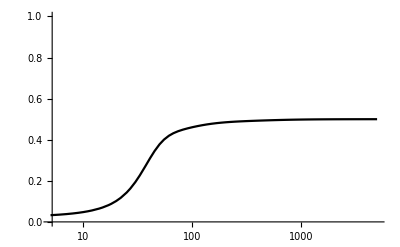

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Black}]
```

{{5,0.0325008},{6,0.0349956},{6,0.0349956},{7,0.037687},{7,0.037687},{8,0.0405868},{9,0.0437069},{10,0.0470594},{11,0.0506562},{12,0.054509},{14,0.0630263},{15,0.0677108},{17,0.0779724},{18,0.0835613},{20,0.0956692},{22,0.109007},{25,0.131186},{27,0.147244},{30,0.172772},{33,0.199286},{37,0.234536},{41,0.267722},{45,0.297282},{50,0.328084},{55,0.352211},{61,0.373846},{67,0.389562},{74,0.402833},{82,0.413701},{91,0.422502},{100,0.428967},{111,0.434724},{123,0.43916},{136,0.443056},{150,0.450314},{166,0.468289},{183,0.48371},{202,0.491118},{224,0.494632},{247,0.496324},{273,0.497322},{302,0.497951},{333,0.498364},{368,0.498672},{407,0.498909},{450,0.499099},{497,0.499254},{550,0.499388},{608,0.499499},{671,0.499592},{742,0.499672},{820,0.499738},{906,0.499793},{1002,0.499837},{1107,0.499873},{1223,0.499901},{1352,0.499923},{1494,0.49994},{1651,0.499954},{1825,0.499964},{2017,0.499972},{2229,0.499979},{2464,0.499983},{2723,0.499987},{3009,0.49999},{3326,0.499992},{3675,0.499994},{4062,0.499995},{4489,0.499996},{4961,0.499997}}

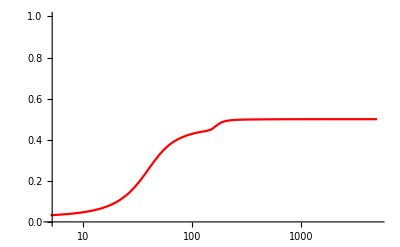

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red}]
```

{{5,0.0320341},{6,0.034323},{6,0.034323},{7,0.0367595},{7,0.0367595},{8,0.0393493},{9,0.0420983},{10,0.0450118},{11,0.0480949},{12,0.0513521},{14,0.0584044},{15,0.0622053},{17,0.0703647},{18,0.0747235},{20,0.0839911},{22,0.0939662},{25,0.110139},{27,0.121615},{30,0.139613},{33,0.158183},{37,0.183066},{41,0.207174},{45,0.22972},{50,0.255003},{55,0.276831},{61,0.298826},{67,0.317082},{74,0.334926},{82,0.352273},{91,0.369362},{100,0.384764},{111,0.401734},{123,0.417829},{136,0.432129},{150,0.443903},{166,0.453424},{183,0.460103},{202,0.464715},{224,0.467606},{247,0.468773},{273,0.468478},{302,0.466525},{333,0.462658},{368,0.455893},{407,0.444827},{450,0.427875},{497,0.405426},{550,0.382413},{608,0.367001},{671,0.359676},{742,0.356818},{820,0.355914},{906,0.355667},{1002,0.35561},{1107,0.355598},{1223,0.355596},{1352,0.355596},{1494,0.355596},{1651,0.355596},{1825,0.355596},{2017,0.355596},{2229,0.355596},{2464,0.355596},{2723,0.355596},{3009,0.355596},{3326,0.355596},{3675,0.355596},{4062,0.355596},{4489,0.355596},{4961,0.355596}}

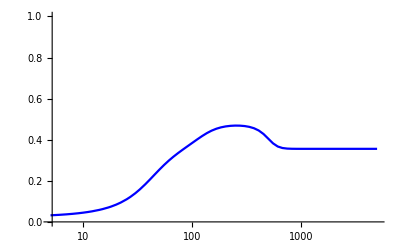

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue}]
```

{{5,0.0309719},{6,0.0329853},{6,0.0329853},{7,0.0351208},{7,0.0351208},{8,0.0373817},{9,0.0397715},{10,0.0422937},{11,0.0449514},{12,0.0477477},{14,0.0537666},{15,0.0569932},{17,0.063887},{18,0.0675549},{20,0.0753288},{22,0.0836731},{25,0.0971922},{27,0.106807},{30,0.121975},{33,0.137809},{37,0.159452},{41,0.181058},{45,0.202007},{50,0.226589},{55,0.248964},{61,0.272806},{67,0.293687},{74,0.314985},{82,0.336187},{91,0.356901},{100,0.374771},{111,0.393029},{123,0.408755},{136,0.421473},{150,0.431114},{166,0.438236},{183,0.442426},{202,0.443954},{224,0.442156},{247,0.436035},{273,0.422333},{302,0.393841},{333,0.339724},{368,0.26014},{407,0.204998},{450,0.17652},{497,0.158771},{550,0.14704},{608,0.139649},{671,0.135104},{742,0.132304},{820,0.130705},{906,0.129837},{1002,0.129392},{1107,0.129185},{1223,0.129095},{1352,0.12906},{1494,0.129048},{1651,0.129044},{1825,0.129043},{2017,0.129042},{2229,0.129042},{2464,0.129042},{2723,0.129042},{3009,0.129042},{3326,0.129042},{3675,0.129042},{4062,0.129042},{4489,0.129042},{4961,0.129042}}

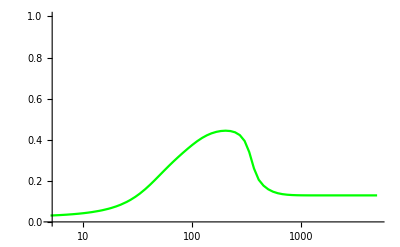

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab7=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset7=ListLogLinearPlot[MODtab7,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

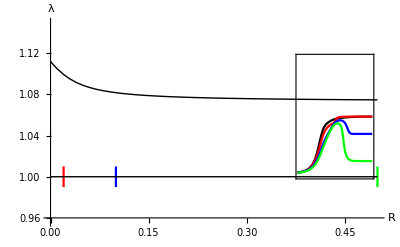

```mathematica
plotC=Show[
plot4,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,MODinset7,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
ListPlot[{{0.02,0.99},{0.02,1.01}},Joined->True,PlotStyle->{Red}],
ListPlot[{{0.1,0.99},{0.1,1.01}},Joined->True,PlotStyle->{Blue}],
ListPlot[{{0.5,0.99},{0.5,1.01}},Joined->True,PlotStyle->{Green}],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.15}},AxesOrigin->{0,0.96}
]
```

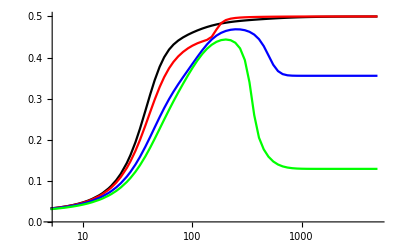

```mathematica
Show[MODinset4,MODinset5,MODinset6,MODinset7,PlotRange->{0,0.5}]
```

#### Overdominance in females, invasion but not fixation (YA equilibrium)

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.7;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.378835,0.305667,0.984382,0.5},{0.720702,0.82555,0.0461837,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.367647,0.289256,1.,0.5}

{0.954304,1.10308}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.09837,0.949853}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.949853,1.09837},{0.945051,1.09038},{0.939709,1.08292},{0.933805,1.07602},{0.927327,1.0697},{0.920276,1.06395},{0.912668,1.05875},{0.904529,1.05409},{0.895897,1.04992},{0.886811,1.0462},{0.877317,1.0429},{0.867457,1.03996},{0.857275,1.03734},{0.84681,1.035},{0.836095,1.03291},{0.825163,1.03104},{0.814041,1.02936},{0.802753,1.02785},{0.79132,1.02648},{0.779759,1.02524},{0.768086,1.02411},{0.756314,1.02308},{0.744455,1.02214},{0.732518,1.02128},{0.720513,1.02048},{0.708446,1.01975},{0.696324,1.01907},{0.684153,1.01844},{0.671938,1.01785},{0.659682,1.0173},{0.647391,1.01679},{0.635066,1.01632},{0.622712,1.01587},{0.61033,1.01545},{0.597923,1.01506},{0.585494,1.01468},{0.573043,1.01433},{0.560574,1.014},{0.548086,1.01369},{0.535582,1.01339},{0.523063,1.01311},{0.51053,1.01284},{0.497984,1.01258},{0.485426,1.01234},{0.472856,1.01211},{0.460276,1.01189},{0.447685,1.01168},{0.435086,1.01147},{0.422478,1.01128},{0.409862,1.0111},{0.397238,1.01092}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

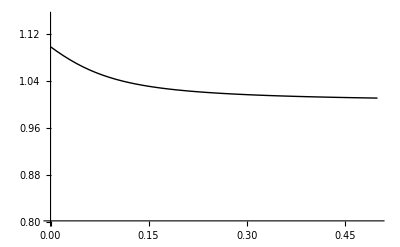

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

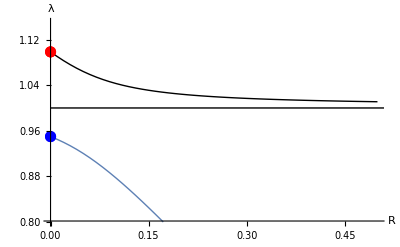

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W dynamics:

{{5,0.0243554},{6,0.0255787},{6,0.0255787},{7,0.0269722},{7,0.0269722},{8,0.0285478},{9,0.0303182},{10,0.0322972},{11,0.0344997},{12,0.0369417},{14,0.0426128},{15,0.0458788},{17,0.0533698},{18,0.0576361},{20,0.0673159},{22,0.0786648},{25,0.099152},{27,0.115289},{30,0.143322},{33,0.175698},{37,0.224056},{41,0.27476},{45,0.322872},{50,0.373153},{55,0.409736},{61,0.43808},{67,0.455015},{74,0.466554},{82,0.474038},{91,0.478839},{100,0.48172},{111,0.483928},{123,0.48549},{136,0.486671},{150,0.487626},{166,0.488494},{183,0.489263},{202,0.490004},{224,0.490755},{247,0.49145},{273,0.49215},{302,0.492844},{333,0.493503},{368,0.494165},{407,0.494815},{450,0.495444},{497,0.496046},{550,0.496634},{608,0.497188},{671,0.497698},{742,0.498178},{820,0.498605},{906,0.498972},{1002,0.499276},{1107,0.499508},{1223,0.499677},{1352,0.499793},{1494,0.499868},{1651,0.499915},{1825,0.499945},{2017,0.499963},{2229,0.499975},{2464,0.499983},{2723,0.499988},{3009,0.499991},{3326,0.499994},{3675,0.499995},{4062,0.499996},{4489,0.499997},{4961,0.499998}}

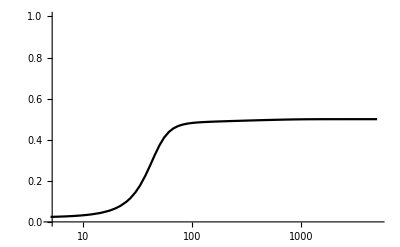

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Black}]
```

{{5,0.0241136},{6,0.0252156},{6,0.0252156},{7,0.0264531},{7,0.0264531},{8,0.0278324},{9,0.0293603},{10,0.0310441},{11,0.0328919},{12,0.034912},{14,0.0395052},{15,0.0420973},{17,0.0479226},{18,0.0511766},{20,0.0584201},{22,0.066714},{25,0.0812954},{27,0.0925388},{30,0.11179},{33,0.133904},{37,0.167476},{41,0.204623},{45,0.243434},{50,0.290715},{55,0.332775},{61,0.373153},{67,0.402419},{74,0.425438},{82,0.441973},{91,0.453293},{100,0.460362},{111,0.465919},{123,0.469921},{136,0.472975},{150,0.475452},{166,0.477704},{183,0.479697},{202,0.481614},{224,0.483553},{247,0.485334},{273,0.487104},{302,0.488821},{333,0.4904},{368,0.491909},{407,0.493304},{450,0.494552},{497,0.495635},{550,0.496582},{608,0.497365},{671,0.497994},{742,0.498507},{820,0.498904},{906,0.499205},{1002,0.499432},{1107,0.499596},{1223,0.499715},{1352,0.499799},{1494,0.499858},{1651,0.4999},{1825,0.499928},{2017,0.499949},{2229,0.499963},{2464,0.499973},{2723,0.49998},{3009,0.499985},{3326,0.499989},{3675,0.499991},{4062,0.499993},{4489,0.499995},{4961,0.499996}}

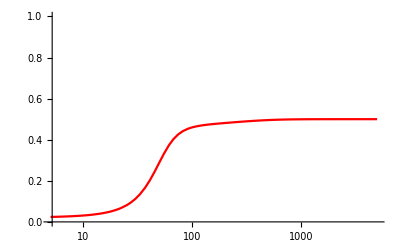

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red}]
```

{{5,0.0232864},{6,0.0240176},{6,0.0240176},{7,0.0247992},{7,0.0247992},{8,0.0256295},{9,0.0265074},{10,0.0274319},{11,0.0284025},{12,0.0294186},{14,0.0315867},{15,0.0327384},{17,0.0351779},{18,0.0364662},{20,0.0391812},{22,0.0420838},{25,0.0467967},{27,0.0501833},{30,0.0556378},{33,0.0615486},{37,0.0701443},{41,0.0795473},{45,0.089725},{50,0.103444},{55,0.118106},{61,0.13661},{67,0.155641},{74,0.177811},{82,0.202155},{91,0.22722},{100,0.249142},{111,0.27144},{123,0.290594},{136,0.306338},{150,0.318857},{166,0.329113},{183,0.336734},{202,0.342574},{224,0.347039},{247,0.350035},{273,0.352155},{302,0.353568},{333,0.354438},{368,0.354977},{407,0.355287},{450,0.355452},{497,0.355533},{550,0.355571},{608,0.355587},{671,0.355593},{742,0.355595},{820,0.355596},{906,0.355596},{1002,0.355596},{1107,0.355596},{1223,0.355596},{1352,0.355596},{1494,0.355596},{1651,0.355596},{1825,0.355596},{2017,0.355596},{2229,0.355596},{2464,0.355596},{2723,0.355596},{3009,0.355596},{3326,0.355596},{3675,0.355596},{4062,0.355596},{4489,0.355596},{4961,0.355596}}

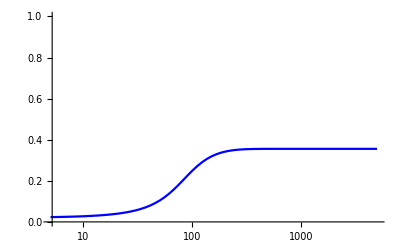

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue}]
```

{{5,0.0212648},{6,0.0214314},{6,0.0214314},{7,0.021603},{7,0.021603},{8,0.0217788},{9,0.0219583},{10,0.022141},{11,0.0223266},{12,0.0225148},{14,0.022898},{15,0.0230928},{17,0.0234878},{18,0.0236879},{20,0.024093},{22,0.0245042},{25,0.0251319},{27,0.0255574},{30,0.0262058},{33,0.0268661},{37,0.0277647},{41,0.0286839},{45,0.0296234},{50,0.0308258},{55,0.032059},{61,0.0335785},{67,0.0351401},{74,0.037013},{82,0.0392176},{91,0.0417736},{100,0.0444023},{111,0.0477011},{123,0.0513878},{136,0.0554566},{150,0.0598877},{166,0.06496},{183,0.0702906},{202,0.0760918},{224,0.082495},{247,0.0887239},{273,0.095099},{302,0.101319},{333,0.106937},{368,0.112094},{407,0.116557},{450,0.120205},{497,0.123029},{550,0.125171},{608,0.126663},{671,0.127645},{742,0.128277},{820,0.128648},{906,0.128853},{1002,0.128959},{1107,0.129008},{1223,0.12903},{1352,0.129038},{1494,0.129041},{1651,0.129042},{1825,0.129042},{2017,0.129042},{2229,0.129042},{2464,0.129042},{2723,0.129042},{3009,0.129042},{3326,0.129042},{3675,0.129042},{4062,0.129042},{4489,0.129042},{4961,0.129042}}

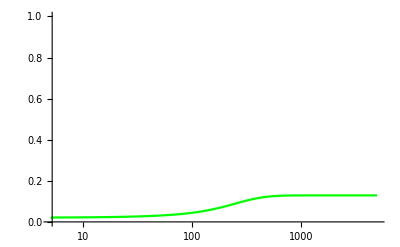

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab7=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset7=ListLogLinearPlot[MODtab7,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

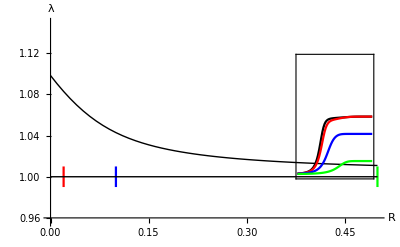

```mathematica
plotC=Show[
plot4,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,MODinset7,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
ListPlot[{{0.02,0.99},{0.02,1.01}},Joined->True,PlotStyle->{Red}],
ListPlot[{{0.1,0.99},{0.1,1.01}},Joined->True,PlotStyle->{Blue}],
ListPlot[{{0.5,0.99},{0.5,1.01}},Joined->True,PlotStyle->{Green}],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.15}},AxesOrigin->{0,0.96}
]
```

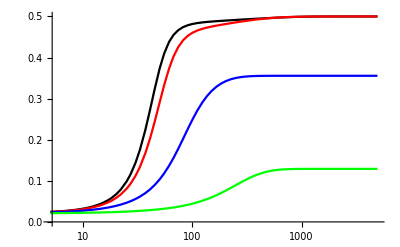

```mathematica
Show[MODinset4,MODinset5,MODinset6,MODinset7,PlotRange->{0,0.5}]
```

#### Parameters

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};

tryFAA2=0.85;
tryFAa2=1;
tryFaa2=1.05;
tryMAA2=0.75;
tryMAa2=1;
tryMaa2=0.75;
trywAf2=1;
trywaf2=1;
trywAm2=1;
trywam2=1;
tryαf2=0.5;
tryαm2=0.5;
tryr2=0.005;
tryR2=0;
subpar2={FAA->tryFAA2,FAa->tryFAa2,Faa->tryFaa2,MAA->tryMAA2,MAa->tryMAa2,Maa->tryMaa2,wAf->trywAf2,waf->trywaf2,wAm->trywAm2,wam->trywam2,αf->tryαf2,αm->tryαm2};

tryFAA3=0.6;
tryFAa3=1;
tryFaa3=0.6;
tryMAA3=0.7;
tryMAa3=1;
tryMaa3=0.5;
trywAf3=1;
trywaf3=1;
trywAm3=1;
trywam3=1;
tryαf3=0.5;
tryαm3=0.5;
tryr3=0.005;
tryR3=0;
subpar3={FAA->tryFAA3,FAa->tryFAa3,Faa->tryFaa3,MAA->tryMAA3,MAa->tryMAa3,Maa->tryMaa3,wAf->trywAf3,waf->trywaf3,wAm->trywAm3,wam->trywam3,αf->tryαf3,αm->tryαm3};
```

#### Combine λ versus R plots

```mathematica
loglinearplotRλoptions={Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{0.001,0.001,{0,0.01}},{0.005,0.005,{0,0.01}},{0.01,0.01,{0,0.01}},{0.05,0.05,{0,0.01}},{0.5,0.5,{0,0.01}}},Table[{y,y,ticksize},{y,0.9,1.2,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{{Style["invasion fitness, λ",FontSize->14],""},{Style["R",FontSize->14],""}}};
```

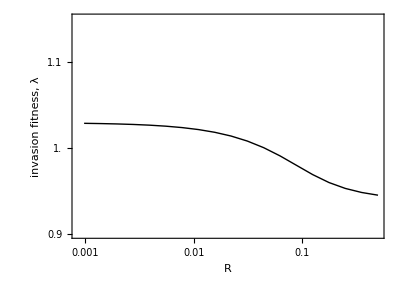

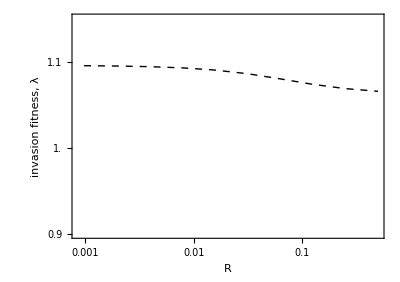

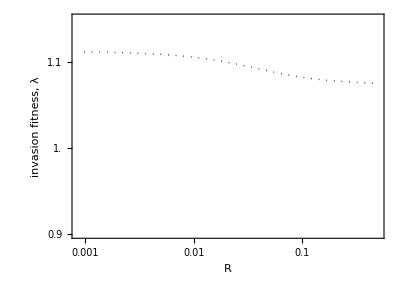

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar1/.R->0.5^b/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{b,10,1,-1/2}];
eigen1=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[2]]}]];
plot1=Show[
ListLogLinearPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.9,1.15}},
loglinearplotRλoptions]
]
tab=Table[
equil=sieve[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar2/.R->0.5^b/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{b,10,1,-1}];
eigen1=Transpose[Join[{Table[0.5^b,{b,10,1,-1}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[0.5^b,{b,10,1,-1}]},{Transpose[tab][[2]]}]];
plot2=Show[
ListLogLinearPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.9,1.15}},
loglinearplotRλoptions]
]
tab=Table[
equil=sieve[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar3/.R->0.5^b/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{b,10,1,-1/2}];
eigen1=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[2]]}]];
plot3=Show[
ListLogLinearPlot[eigen2,Joined->True,PlotStyle->{Thick,Dotted,Black},PlotRange->{Automatic,{0.9,1.15}},
loglinearplotRλoptions]
]
```

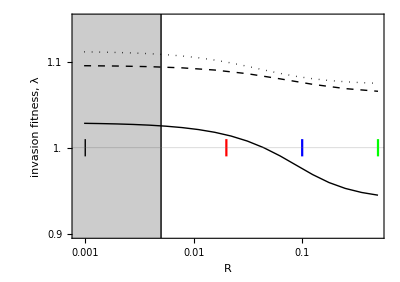

```mathematica
temp=Show[
plot1,plot2,plot3,
ListLogLinearPlot[{{tryr,0},{tryr,2}},Joined->True,PlotStyle->{Black,Thin}],
ListLogLinearPlot[{{0.001,0.99},{0.001,1.01}},Joined->True,PlotStyle->{Black,Thick}],
ListLogLinearPlot[{{0.02,0.99},{0.02,1.01}},Joined->True,PlotStyle->{Red}],
ListLogLinearPlot[{{0.1,0.99},{0.1,1.01}},Joined->True,PlotStyle->{Blue}],
ListLogLinearPlot[{{0.5,0.99},{0.5,1.01}},Joined->True,PlotStyle->{Green}],
ListLogLinearPlot[{{0.0001,2},{tryr,2}},Joined->True,PlotStyle->{Black,Thin},Filling->Bottom],
GridLines->{{0.005},{1}}(*,
GridLinesStyle->Black*)]
```

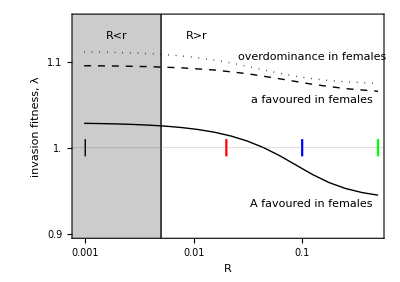

```mathematica
Show[temp,
Graphics[Text["R>r",{-4.55,1.13},BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->14}]],
Graphics[Text["R<r",{-6.25,1.13},BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->14}]],
Graphics[Text["A favoured in females",{-2.1,0.935}]],
Graphics[Text["a favoured in females",{-2.1,1.055}]],
Graphics[Text["overdominance in females",{-2.1,1.105}]]]
```

### Combine invasion plots